```mathematica
With[{Subscript[t, 1]=1,Subscript[t, 2]=2},h={{-δ,Subscript[t, 1],0,0,0,0,0,Subscript[t, 2]},{Subscript[t, 1],δ,Subscript[t, 2],0,Subscript[t, 1]*Exp[i*Subscript[k, y]],0,0,0},{0,Subscript[t, 2],δ,Subscript[t, 1],0,0,0,Subscript[t, 1]*Exp[i*Subscript[k, x]]},{0,0,Subscript[t, 1],δ,Subscript[t, 2],0,t1*Exp[i*Subscript[k, x]],0},{0,Subscript[t, 1]*Exp[-i*Subscript[k, y]],0,Subscript[t, 2],δ,Subscript[t, 1],0,0},{Subscript[t, 1]*Exp[-i*Subscript[k, y]],0,0,Subscript[t, 1],-δ,Subscript[t, 2],0},{0,0,0,Subscript[t, 1]*Exp[-i*Subscript[k, x]],0,Subscript[t, 2],-δ,Subscript[t, 1]},{Subscript[t, 2],0,Subscript[t, 1]*Exp[-i*Subscript[k, x]],0,0,0,Subscript[t, 1],-δ}}]
```

With::lvset: Local variable specification {t_1 = 1, t_2 = 2} contains t_1 = 1, which is an assignment to t_1; only assignments to symbols are allowed.

With[{t_1=1,t_2=2},h={{-δ,t_1,0,0,0,0,0,t_2},{t_1,δ,t_2,0,t_1 Exp[i k_y],0,0,0},{0,t_2,δ,t_1,0,0,0,t_1 Exp[i k_x]},{0,0,t_1,δ,t_2,0,t1 Exp[i k_x],0},{0,t_1 Exp[-i k_y],0,t_2,δ,t_1,0,0},{t_1 Exp[-i k_y],0,0,t_1,-δ,t_2,0},{0,0,0,t_1 Exp[-i k_x],0,t_2,-δ,t_1},{t_2,0,t_1 Exp[-i k_x],0,0,0,t_1,-δ}}]

```mathematica
h
```

h

```mathematica
={{-δ,Subscript[t, 1],0,0,0,0,0,Subscript[t, 2]},{Subscript[t, 1],δ,Subscript[t, 2],0,Subscript[t, 1]*Exp[i*Subscript[k, y]],0,0,0},{0,Subscript[t, 2],δ,Subscript[t, 1],0,0,0,Subscript[t, 1]*Exp[i*Subscript[k, x]]},{0,0,Subscript[t, 1],δ,Subscript[t, 2],0,t1*Exp[i*Subscript[k, x]],0},{0,Subscript[t, 1]*Exp[-i*Subscript[k, y]],0,Subscript[t, 2],δ,Subscript[t, 1],0,0},{Subscript[t, 1]*Exp[-i*Subscript[k, y]],0,0,Subscript[t, 1],-δ,Subscript[t, 2],0},{0,0,0,Subscript[t, 1]*Exp[-i*Subscript[k, x]],0,Subscript[t, 2],-δ,Subscript[t, 1]},{Subscript[t, 2],0,Subscript[t, 1]*Exp[-i*Subscript[k, x]],0,0,0,Subscript[t, 1],-δ}}
```

```mathematica
h={{-δ,Subscript[t, 1],0,0,0,0,0,Subscript[t, 2]},{Subscript[t, 1],δ,Subscript[t, 2],0,Subscript[t, 1]*Exp[i*Subscript[k, y]],0,0,0},{0,Subscript[t, 2],δ,Subscript[t, 1],0,0,0,Subscript[t, 1]*Exp[i*Subscript[k, x]]},{0,0,Subscript[t, 1],δ,Subscript[t, 2],0,t1*Exp[i*Subscript[k, x]],0},{0,Subscript[t, 1]*Exp[-i*Subscript[k, y]],0,Subscript[t, 2],δ,Subscript[t, 1],0,0},{Subscript[t, 1]*Exp[-i*Subscript[k, y]],0,0,Subscript[t, 1],-δ,Subscript[t, 2],0},{0,0,0,Subscript[t, 1]*Exp[-i*Subscript[k, x]],0,Subscript[t, 2],-δ,Subscript[t, 1]},{Subscript[t, 2],0,Subscript[t, 1]*Exp[-i*Subscript[k, x]],0,0,0,Subscript[t, 1],-δ}}
```

{{-δ,t_1,0,0,0,0,0,t_2},{t_1,δ,t_2,0,ⅇ^(i k_y) t_1,0,0,0},{0,t_2,δ,t_1,0,0,0,ⅇ^(i k_x) t_1},{0,0,t_1,δ,t_2,0,ⅇ^(i k_x) t1,0},{0,ⅇ^(-i k_y) t_1,0,t_2,δ,t_1,0,0},{ⅇ^(-i k_y) t_1,0,0,t_1,-δ,t_2,0},{0,0,0,ⅇ^(-i k_x) t_1,0,t_2,-δ,t_1},{t_2,0,ⅇ^(-i k_x) t_1,0,0,0,t_1,-δ}}

```mathematica
With[{Subscript[t, 1]=1,Subscript[t, 2]=2},h]
```

With::lvset: Local variable specification {t_1 = 1, t_2 = 2} contains t_1 = 1, which is an assignment to t_1; only assignments to symbols are allowed.

With[{t_1=1,t_2=2},h]

```mathematica
h
```

{{-δ,t_1,0,0,0,0,0,t_2},{t_1,δ,t_2,0,ⅇ^(i k_y) t_1,0,0,0},{0,t_2,δ,t_1,0,0,0,ⅇ^(i k_x) t_1},{0,0,t_1,δ,t_2,0,ⅇ^(i k_x) t1,0},{0,ⅇ^(-i k_y) t_1,0,t_2,δ,t_1,0,0},{ⅇ^(-i k_y) t_1,0,0,t_1,-δ,t_2,0},{0,0,0,ⅇ^(-i k_x) t_1,0,t_2,-δ,t_1},{t_2,0,ⅇ^(-i k_x) t_1,0,0,0,t_1,-δ}}

```mathematica
With[{t[1]=1,t[2]=2},h]
```

With::lvset: Local variable specification {t[1] = 1, t[2] = 2} contains t[1] = 1, which is an assignment to t[1]; only assignments to symbols are allowed.

With[{t[1]=1,t[2]=2},h]

```mathematica
h={{-δ,Subscript[t, 1],0,0,0,0,0,Subscript[t, 2]},{Subscript[t, 1],δ,Subscript[t, 2],0,Subscript[t, 1]*Exp[i*Subscript[k, y]],0,0,0},{0,Subscript[t, 2],δ,Subscript[t, 1],0,0,0,Subscript[t, 1]*Exp[i*Subscript[k, x]]},{0,0,Subscript[t, 1],δ,Subscript[t, 2],0,t1*Exp[i*Subscript[k, x]],0},{0,Subscript[t, 1]*Exp[-i*Subscript[k, y]],0,Subscript[t, 2],δ,Subscript[t, 1],0,0},{Subscript[t, 1]*Exp[-i*Subscript[k, y]],0,0,Subscript[t, 1],-δ,Subscript[t, 2],0},{0,0,0,Subscript[t, 1]*Exp[-i*Subscript[k, x]],0,Subscript[t, 2],-δ,Subscript[t, 1]},{Subscript[t, 2],0,Subscript[t, 1]*Exp[-i*Subscript[k, x]],0,0,0,Subscript[t, 1],-δ}}
```

{{-δ,t_1,0,0,0,0,0,t_2},{t_1,δ,t_2,0,ⅇ^(i k_y) t_1,0,0,0},{0,t_2,δ,t_1,0,0,0,ⅇ^(i k_x) t_1},{0,0,t_1,δ,t_2,0,ⅇ^(i k_x) t1,0},{0,ⅇ^(-i k_y) t_1,0,t_2,δ,t_1,0,0},{ⅇ^(-i k_y) t_1,0,0,t_1,-δ,t_2,0},{0,0,0,ⅇ^(-i k_x) t_1,0,t_2,-δ,t_1},{t_2,0,ⅇ^(-i k_x) t_1,0,0,0,t_1,-δ}}

```mathematica
h
```

{{-δ,t_1,0,0,0,0,0,t_2},{t_1,δ,t_2,0,ⅇ^(i k_y) t_1,0,0,0},{0,t_2,δ,t_1,0,0,0,ⅇ^(i k_x) t_1},{0,0,t_1,δ,t_2,0,ⅇ^(i k_x) t1,0},{0,ⅇ^(-i k_y) t_1,0,t_2,δ,t_1,0,0},{ⅇ^(-i k_y) t_1,0,0,t_1,-δ,t_2,0},{0,0,0,ⅇ^(-i k_x) t_1,0,t_2,-δ,t_1},{t_2,0,ⅇ^(-i k_x) t_1,0,0,0,t_1,-δ}}

```mathematica
Eigenvalues[h]
```

Eigenvalues::matsq: Argument {{-δ, t_1, 0, 0, 0, 0, 0, t_2}, {t_1, δ, t_2, 0, ⅇ^i\ k_y\ t_1, 0, 0, 0}, {0, t_2, δ, t_1, 0, 0, 0, ⅇ^i\ k_x\ t_1}, {0, 0, t_1, δ, t_2, 0, ⅇ^i\ k_x\ t1, 0}, {0, ⅇ^-i\ k_y\ t_1, 0, t_2, δ, t_1, 0, 0}, {ⅇ^-i\ k_y\ t_1, 0, 0, t_1, -δ, t_2, 0}, {0, 0, 0, ⅇ^-i\ k_x\ t_1, 0, t_2, -δ, t_1}, {t_2, 0, ⅇ^-i\ k_x\ t_1, 0, 0, 0, t_1, -δ}} at position 1 is not a non-empty square matrix.

Eigenvalues[{{-δ,t_1,0,0,0,0,0,t_2},{t_1,δ,t_2,0,ⅇ^(i k_y) t_1,0,0,0},{0,t_2,δ,t_1,0,0,0,ⅇ^(i k_x) t_1},{0,0,t_1,δ,t_2,0,ⅇ^(i k_x) t1,0},{0,ⅇ^(-i k_y) t_1,0,t_2,δ,t_1,0,0},{ⅇ^(-i k_y) t_1,0,0,t_1,-δ,t_2,0},{0,0,0,ⅇ^(-i k_x) t_1,0,t_2,-δ,t_1},{t_2,0,ⅇ^(-i k_x) t_1,0,0,0,t_1,-δ}}]

```mathematica
h={{-δ,Subscript[t, 1],0,0,0,0,0,Subscript[t, 2]},{Subscript[t, 1],δ,Subscript[t, 2],0,ⅇ^(i Subscript[k, y]) Subscript[t, 1],0,0,0},{0,Subscript[t, 2],δ,Subscript[t, 1],0,0,0,ⅇ^(i Subscript[k, x]) Subscript[t, 1]},{0,0,Subscript[t, 1],δ,Subscript[t, 2],0,ⅇ^(i Subscript[k, x]) t1,0},{0,ⅇ^(-i Subscript[k, y]) Subscript[t, 1],0,Subscript[t, 2],δ,Subscript[t, 1],0,0},{ⅇ^(-i Subscript[k, y]) Subscript[t, 1],0,0,0,Subscript[t, 1],-δ,Subscript[t, 2],0},{0,0,0,ⅇ^(-i Subscript[k, x]) Subscript[t, 1],0,Subscript[t, 2],-δ,Subscript[t, 1]},{Subscript[t, 2],0,ⅇ^(-i Subscript[k, x]) Subscript[t, 1],0,0,0,Subscript[t, 1],-δ}}
```

{{-δ,t_1,0,0,0,0,0,t_2},{t_1,δ,t_2,0,ⅇ^(i k_y) t_1,0,0,0},{0,t_2,δ,t_1,0,0,0,ⅇ^(i k_x) t_1},{0,0,t_1,δ,t_2,0,ⅇ^(i k_x) t1,0},{0,ⅇ^(-i k_y) t_1,0,t_2,δ,t_1,0,0},{ⅇ^(-i k_y) t_1,0,0,0,t_1,-δ,t_2,0},{0,0,0,ⅇ^(-i k_x) t_1,0,t_2,-δ,t_1},{t_2,0,ⅇ^(-i k_x) t_1,0,0,0,t_1,-δ}}

```mathematica
Eigenvalues[h]
```

{ⅇ^(-i k_x-i k_y) Root[ⅇ^(8 i (k_x+k_y)) δ^8+#1^8+ⅇ^(8 i (k_x+k_y)) t1 δ^6 t_1-2 ⅇ^(3 i (k_x+k_y)) δ #1^5 t_1^2+ⅇ^(8 i (k_x+k_y)) t1 δ^4 t_1^3-ⅇ^(8 i (k_x+k_y)) δ^4 t_1^4-4 ⅇ^(8 i (k_x+k_y)) δ^6 t_2^2-2 ⅇ^(8 i (k_x+k_y)) t1 δ^4 t_1 t_2^2-ⅇ^(9 i k_x+8 i k_y) t1 δ^4 t_1 t_2^2-2 ⅇ^(8 i k_x+7 i k_y) δ^4 t_1^2 t_2^2-2 ⅇ^(7 i k_x+8 i k_y) δ^4 t_1^2 t_2^2-ⅇ^(9 i k_x+8 i k_y) δ^4 t_1^2 t_2^2-ⅇ^(8 i k_x+9 i k_y) δ^4 t_1^2 t_2^2-ⅇ^(8 i (k_x+k_y)) t1 δ^2 t_1^3 t_2^2+ⅇ^(9 i (k_x+k_y)) t1 δ^2 t_1^3 t_2^2-ⅇ^(8 i k_x+7 i k_y) t1 δ^2 t_1^3 t_2^2-ⅇ^(7 i k_x+8 i k_y) t1 δ^2 t_1^3 t_2^2-ⅇ^(9 i k_x+8 i k_y) t1 δ^2 t_1^3 t_2^2-ⅇ^(8 i k_x+9 i k_y) t1 δ^2 t_1^3 t_2^2+ⅇ^(8 i (k_x+k_y)) δ^2 t_1^4 t_2^2-ⅇ^(9 i (k_x+k_y)) δ^2 t_1^4 t_2^2+6 ⅇ^(8 i (k_x+k_y)) δ^4 t_2^4+ⅇ^(8 i (k_x+k_y)) t1 δ^2 t_1 t_2^4+2 ⅇ^(9 i k_x+8 i k_y) t1 δ^2 t_1 t_2^4+4 ⅇ^(8 i k_x+7 i k_y) δ^2 t_1^2 t_2^4+4 ⅇ^(7 i k_x+8 i k_y) δ^2 t_1^2 t_2^4+2 ⅇ^(9 i k_x+8 i k_y) δ^2 t_1^2 t_2^4+2 ⅇ^(8 i k_x+9 i k_y) δ^2 t_1^2 t_2^4+ⅇ^(8 i (k_x+k_y)) t1 t_1^3 t_2^4+ⅇ^(2 i (5 k_x+4 k_y)) t1 t_1^3 t_2^4+ⅇ^(9 i k_x+7 i k_y) t1 t_1^3 t_2^4+2 ⅇ^(7 i (k_x+k_y)) t_1^4 t_2^4+2 ⅇ^(8 i (k_x+k_y)) t_1^4 t_2^4+ⅇ^(9 i (k_x+k_y)) t_1^4 t_2^4+ⅇ^(2 i (4 k_x+3 k_y)) t_1^4 t_2^4+ⅇ^(2 i (3 k_x+4 k_y)) t_1^4 t_2^4+ⅇ^(9 i k_x+7 i k_y) t_1^4 t_2^4+ⅇ^(7 i k_x+9 i k_y) t_1^4 t_2^4-4 ⅇ^(8 i (k_x+k_y)) δ^2 t_2^6-ⅇ^(9 i k_x+8 i k_y) t1 t_1 t_2^6-2 ⅇ^(8 i k_x+7 i k_y) t_1^2 t_2^6-2 ⅇ^(7 i k_x+8 i k_y) t_1^2 t_2^6-ⅇ^(9 i k_x+8 i k_y) t_1^2 t_2^6-ⅇ^(8 i k_x+9 i k_y) t_1^2 t_2^6+ⅇ^(8 i (k_x+k_y)) t_2^8+#1^6 (-4 ⅇ^(2 i (k_x+k_y)) δ^2-ⅇ^(2 i (k_x+k_y)) t1 t_1-6 ⅇ^(2 i (k_x+k_y)) t_1^2-4 ⅇ^(2 i (k_x+k_y)) t_2^2)+#1^3 (4 ⅇ^(5 i (k_x+k_y)) δ^3 t_1^2+2 ⅇ^(5 i (k_x+k_y)) t1 δ t_1^3+6 ⅇ^(5 i (k_x+k_y)) δ t_1^4-4 ⅇ^(5 i k_x+6 i k_y) δ t_1^2 t_2^2)+#1^4 (6 ⅇ^(4 i (k_x+k_y)) δ^4+3 ⅇ^(4 i (k_x+k_y)) t1 δ^2 t_1+12 ⅇ^(4 i (k_x+k_y)) δ^2 t_1^2+3 ⅇ^(4 i (k_x+k_y)) t1 t_1^3+9 ⅇ^(4 i (k_x+k_y)) t_1^4+4 ⅇ^(4 i (k_x+k_y)) δ^2 t_2^2+2 ⅇ^(4 i (k_x+k_y)) t1 t_1 t_2^2-ⅇ^(5 i k_x+4 i k_y) t1 t_1 t_2^2+12 ⅇ^(4 i (k_x+k_y)) t_1^2 t_2^2-2 ⅇ^(4 i k_x+3 i k_y) t_1^2 t_2^2-2 ⅇ^(3 i k_x+4 i k_y) t_1^2 t_2^2-ⅇ^(5 i k_x+4 i k_y) t_1^2 t_2^2-ⅇ^(4 i k_x+5 i k_y) t_1^2 t_2^2+6 ⅇ^(4 i (k_x+k_y)) t_2^4)+#1 (-2 ⅇ^(7 i (k_x+k_y)) δ^5 t_1^2-2 ⅇ^(7 i (k_x+k_y)) t1 δ^3 t_1^3+2 ⅇ^(7 i (k_x+k_y)) δ^3 t_1^4-4 ⅇ^(7 i k_x+8 i k_y) δ^3 t_1^2 t_2^2-2 ⅇ^(2 i (4 k_x+3 k_y)) t1 δ t_1^3 t_2^2+2 ⅇ^(7 i k_x+6 i k_y) t1 δ t_1^3 t_2^2-2 ⅇ^(7 i k_x+8 i k_y) t1 δ t_1^3 t_2^2-4 ⅇ^(7 i (k_x+k_y)) δ t_1^4 t_2^2-2 ⅇ^(8 i (k_x+k_y)) δ t_1^4 t_2^2+2 ⅇ^(2 i (4 k_x+3 k_y)) δ t_1^4 t_2^2-2 ⅇ^(2 i (3 k_x+4 k_y)) δ t_1^4 t_2^2-4 ⅇ^(7 i k_x+6 i k_y) δ t_1^4 t_2^2+4 ⅇ^(7 i k_x+8 i k_y) δ t_1^4 t_2^2+2 ⅇ^(7 i (k_x+k_y)) δ t_1^2 t_2^4+4 ⅇ^(7 i k_x+8 i k_y) δ t_1^2 t_2^4)+#1^2 (-4 ⅇ^(6 i (k_x+k_y)) δ^6-3 ⅇ^(6 i (k_x+k_y)) t1 δ^4 t_1-6 ⅇ^(6 i (k_x+k_y)) δ^4 t_1^2-4 ⅇ^(6 i (k_x+k_y)) t1 δ^2 t_1^3+4 ⅇ^(6 i (k_x+k_y)) δ^4 t_2^2+2 ⅇ^(7 i k_x+6 i k_y) t1 δ^2 t_1 t_2^2-12 ⅇ^(6 i (k_x+k_y)) δ^2 t_1^2 t_2^2-12 ⅇ^(6 i k_x+5 i k_y) δ^2 t_1^2 t_2^2+4 ⅇ^(5 i k_x+6 i k_y) δ^2 t_1^2 t_2^2+2 ⅇ^(7 i k_x+6 i k_y) δ^2 t_1^2 t_2^2-6 ⅇ^(6 i k_x+7 i k_y) δ^2 t_1^2 t_2^2-3 ⅇ^(6 i (k_x+k_y)) t1 t_1^3 t_2^2-ⅇ^(7 i (k_x+k_y)) t1 t_1^3 t_2^2-ⅇ^(6 i k_x+5 i k_y) t1 t_1^3 t_2^2-2 ⅇ^(7 i k_x+5 i k_y) t1 t_1^3 t_2^2+ⅇ^(5 i k_x+6 i k_y) t1 t_1^3 t_2^2+ⅇ^(7 i k_x+6 i k_y) t1 t_1^3 t_2^2-ⅇ^(6 i k_x+7 i k_y) t1 t_1^3 t_2^2-4 ⅇ^(5 i (k_x+k_y)) t_1^4 t_2^2-9 ⅇ^(6 i (k_x+k_y)) t_1^4 t_2^2-ⅇ^(7 i (k_x+k_y)) t_1^4 t_2^2-2 ⅇ^(7 i k_x+5 i k_y) t_1^4 t_2^2-2 ⅇ^(5 i k_x+7 i k_y) t_1^4 t_2^2+4 ⅇ^(6 i (k_x+k_y)) δ^2 t_2^4-ⅇ^(6 i (k_x+k_y)) t1 t_1 t_2^4+2 ⅇ^(7 i k_x+6 i k_y) t1 t_1 t_2^4-6 ⅇ^(6 i (k_x+k_y)) t_1^2 t_2^4+4 ⅇ^(6 i k_x+5 i k_y) t_1^2 t_2^4+4 ⅇ^(5 i k_x+6 i k_y) t_1^2 t_2^4+2 ⅇ^(7 i k_x+6 i k_y) t_1^2 t_2^4+2 ⅇ^(6 i k_x+7 i k_y) t_1^2 t_2^4-4 ⅇ^(6 i (k_x+k_y)) t_2^6)&,1],ⅇ^(-i k_x-i k_y) Root[ⅇ^(8 i (k_x+k_y)) δ^8+#1^8+ⅇ^(8 i (k_x+k_y)) t1 δ^6 t_1-2 ⅇ^(3 i (k_x+k_y)) δ #1^5 t_1^2+ⅇ^(8 i (k_x+k_y)) t1 δ^4 t_1^3-ⅇ^(8 i (k_x+k_y)) δ^4 t_1^4-4 ⅇ^(8 i (k_x+k_y)) δ^6 t_2^2-2 ⅇ^(8 i (k_x+k_y)) t1 δ^4 t_1 t_2^2-ⅇ^(9 i k_x+8 i k_y) t1 δ^4 t_1 t_2^2-2 ⅇ^(8 i k_x+7 i k_y) δ^4 t_1^2 t_2^2-2 ⅇ^(7 i k_x+8 i k_y) δ^4 t_1^2 t_2^2-ⅇ^(9 i k_x+8 i k_y) δ^4 t_1^2 t_2^2-ⅇ^(8 i k_x+9 i k_y) δ^4 t_1^2 t_2^2-ⅇ^(8 i (k_x+k_y)) t1 δ^2 t_1^3 t_2^2+ⅇ^(9 i (k_x+k_y)) t1 δ^2 t_1^3 t_2^2-ⅇ^(8 i k_x+7 i k_y) t1 δ^2 t_1^3 t_2^2-ⅇ^(7 i k_x+8 i k_y) t1 δ^2 t_1^3 t_2^2-ⅇ^(9 i k_x+8 i k_y) t1 δ^2 t_1^3 t_2^2-ⅇ^(8 i k_x+9 i k_y) t1 δ^2 t_1^3 t_2^2+ⅇ^(8 i (k_x+k_y)) δ^2 t_1^4 t_2^2-ⅇ^(9 i (k_x+k_y)) δ^2 t_1^4 t_2^2+6 ⅇ^(8 i (k_x+k_y)) δ^4 t_2^4+ⅇ^(8 i (k_x+k_y)) t1 δ^2 t_1 t_2^4+2 ⅇ^(9 i k_x+8 i k_y) t1 δ^2 t_1 t_2^4+4 ⅇ^(8 i k_x+7 i k_y) δ^2 t_1^2 t_2^4+4 ⅇ^(7 i k_x+8 i k_y) δ^2 t_1^2 t_2^4+2 ⅇ^(9 i k_x+8 i k_y) δ^2 t_1^2 t_2^4+2 ⅇ^(8 i k_x+9 i k_y) δ^2 t_1^2 t_2^4+ⅇ^(8 i (k_x+k_y)) t1 t_1^3 t_2^4+ⅇ^(2 i (5 k_x+4 k_y)) t1 t_1^3 t_2^4+ⅇ^(9 i k_x+7 i k_y) t1 t_1^3 t_2^4+2 ⅇ^(7 i (k_x+k_y)) t_1^4 t_2^4+2 ⅇ^(8 i (k_x+k_y)) t_1^4 t_2^4+ⅇ^(9 i (k_x+k_y)) t_1^4 t_2^4+ⅇ^(2 i (4 k_x+3 k_y)) t_1^4 t_2^4+ⅇ^(2 i (3 k_x+4 k_y)) t_1^4 t_2^4+ⅇ^(9 i k_x+7 i k_y) t_1^4 t_2^4+ⅇ^(7 i k_x+9 i k_y) t_1^4 t_2^4-4 ⅇ^(8 i (k_x+k_y)) δ^2 t_2^6-ⅇ^(9 i k_x+8 i k_y) t1 t_1 t_2^6-2 ⅇ^(8 i k_x+7 i k_y) t_1^2 t_2^6-2 ⅇ^(7 i k_x+8 i k_y) t_1^2 t_2^6-ⅇ^(9 i k_x+8 i k_y) t_1^2 t_2^6-ⅇ^(8 i k_x+9 i k_y) t_1^2 t_2^6+ⅇ^(8 i (k_x+k_y)) t_2^8+#1^6 (-4 ⅇ^(2 i (k_x+k_y)) δ^2-ⅇ^(2 i (k_x+k_y)) t1 t_1-6 ⅇ^(2 i (k_x+k_y)) t_1^2-4 ⅇ^(2 i (k_x+k_y)) t_2^2)+#1^3 (4 ⅇ^(5 i (k_x+k_y)) δ^3 t_1^2+2 ⅇ^(5 i (k_x+k_y)) t1 δ t_1^3+6 ⅇ^(5 i (k_x+k_y)) δ t_1^4-4 ⅇ^(5 i k_x+6 i k_y) δ t_1^2 t_2^2)+#1^4 (6 ⅇ^(4 i (k_x+k_y)) δ^4+3 ⅇ^(4 i (k_x+k_y)) t1 δ^2 t_1+12 ⅇ^(4 i (k_x+k_y)) δ^2 t_1^2+3 ⅇ^(4 i (k_x+k_y)) t1 t_1^3+9 ⅇ^(4 i (k_x+k_y)) t_1^4+4 ⅇ^(4 i (k_x+k_y)) δ^2 t_2^2+2 ⅇ^(4 i (k_x+k_y)) t1 t_1 t_2^2-ⅇ^(5 i k_x+4 i k_y) t1 t_1 t_2^2+12 ⅇ^(4 i (k_x+k_y)) t_1^2 t_2^2-2 ⅇ^(4 i k_x+3 i k_y) t_1^2 t_2^2-2 ⅇ^(3 i k_x+4 i k_y) t_1^2 t_2^2-ⅇ^(5 i k_x+4 i k_y) t_1^2 t_2^2-ⅇ^(4 i k_x+5 i k_y) t_1^2 t_2^2+6 ⅇ^(4 i (k_x+k_y)) t_2^4)+#1 (-2 ⅇ^(7 i (k_x+k_y)) δ^5 t_1^2-2 ⅇ^(7 i (k_x+k_y)) t1 δ^3 t_1^3+2 ⅇ^(7 i (k_x+k_y)) δ^3 t_1^4-4 ⅇ^(7 i k_x+8 i k_y) δ^3 t_1^2 t_2^2-2 ⅇ^(2 i (4 k_x+3 k_y)) t1 δ t_1^3 t_2^2+2 ⅇ^(7 i k_x+6 i k_y) t1 δ t_1^3 t_2^2-2 ⅇ^(7 i k_x+8 i k_y) t1 δ t_1^3 t_2^2-4 ⅇ^(7 i (k_x+k_y)) δ t_1^4 t_2^2-2 ⅇ^(8 i (k_x+k_y)) δ t_1^4 t_2^2+2 ⅇ^(2 i (4 k_x+3 k_y)) δ t_1^4 t_2^2-2 ⅇ^(2 i (3 k_x+4 k_y)) δ t_1^4 t_2^2-4 ⅇ^(7 i k_x+6 i k_y) δ t_1^4 t_2^2+4 ⅇ^(7 i k_x+8 i k_y) δ t_1^4 t_2^2+2 ⅇ^(7 i (k_x+k_y)) δ t_1^2 t_2^4+4 ⅇ^(7 i k_x+8 i k_y) δ t_1^2 t_2^4)+#1^2 (-4 ⅇ^(6 i (k_x+k_y)) δ^6-3 ⅇ^(6 i (k_x+k_y)) t1 δ^4 t_1-6 ⅇ^(6 i (k_x+k_y)) δ^4 t_1^2-4 ⅇ^(6 i (k_x+k_y)) t1 δ^2 t_1^3+4 ⅇ^(6 i (k_x+k_y)) δ^4 t_2^2+2 ⅇ^(7 i k_x+6 i k_y) t1 δ^2 t_1 t_2^2-12 ⅇ^(6 i (k_x+k_y)) δ^2 t_1^2 t_2^2-12 ⅇ^(6 i k_x+5 i k_y) δ^2 t_1^2 t_2^2+4 ⅇ^(5 i k_x+6 i k_y) δ^2 t_1^2 t_2^2+2 ⅇ^(7 i k_x+6 i k_y) δ^2 t_1^2 t_2^2-6 ⅇ^(6 i k_x+7 i k_y) δ^2 t_1^2 t_2^2-3 ⅇ^(6 i (k_x+k_y)) t1 t_1^3 t_2^2-ⅇ^(7 i (k_x+k_y)) t1 t_1^3 t_2^2-ⅇ^(6 i k_x+5 i k_y) t1 t_1^3 t_2^2-2 ⅇ^(7 i k_x+5 i k_y) t1 t_1^3 t_2^2+ⅇ^(5 i k_x+6 i k_y) t1 t_1^3 t_2^2+ⅇ^(7 i k_x+6 i k_y) t1 t_1^3 t_2^2-ⅇ^(6 i k_x+7 i k_y) t1 t_1^3 t_2^2-4 ⅇ^(5 i (k_x+k_y)) t_1^4 t_2^2-9 ⅇ^(6 i (k_x+k_y)) t_1^4 t_2^2-ⅇ^(7 i (k_x+k_y)) t_1^4 t_2^2-2 ⅇ^(7 i k_x+5 i k_y) t_1^4 t_2^2-2 ⅇ^(5 i k_x+7 i k_y) t_1^4 t_2^2+4 ⅇ^(6 i (k_x+k_y)) δ^2 t_2^4-ⅇ^(6 i (k_x+k_y)) t1 t_1 t_2^4+2 ⅇ^(7 i k_x+6 i k_y) t1 t_1 t_2^4-6 ⅇ^(6 i (k_x+k_y)) t_1^2 t_2^4+4 ⅇ^(6 i k_x+5 i k_y) t_1^2 t_2^4+4 ⅇ^(5 i k_x+6 i k_y) t_1^2 t_2^4+2 ⅇ^(7 i k_x+6 i k_y) t_1^2 t_2^4+2 ⅇ^(6 i k_x+7 i k_y) t_1^2 t_2^4-4 ⅇ^(6 i (k_x+k_y)) t_2^6)&,2],ⅇ^(-i k_x-i k_y) Root[ⅇ^(8 i (k_x+k_y)) δ^8+#1^8+ⅇ^(8 i (k_x+k_y)) t1 δ^6 t_1-2 ⅇ^(3 i (k_x+k_y)) δ #1^5 t_1^2+ⅇ^(8 i (k_x+k_y)) t1 δ^4 t_1^3-ⅇ^(8 i (k_x+k_y)) δ^4 t_1^4-4 ⅇ^(8 i (k_x+k_y)) δ^6 t_2^2-2 ⅇ^(8 i (k_x+k_y)) t1 δ^4 t_1 t_2^2-ⅇ^(9 i k_x+8 i k_y) t1 δ^4 t_1 t_2^2-2 ⅇ^(8 i k_x+7 i k_y) δ^4 t_1^2 t_2^2-2 ⅇ^(7 i k_x+8 i k_y) δ^4 t_1^2 t_2^2-ⅇ^(9 i k_x+8 i k_y) δ^4 t_1^2 t_2^2-ⅇ^(8 i k_x+9 i k_y) δ^4 t_1^2 t_2^2-ⅇ^(8 i (k_x+k_y)) t1 δ^2 t_1^3 t_2^2+ⅇ^(9 i (k_x+k_y)) t1 δ^2 t_1^3 t_2^2-ⅇ^(8 i k_x+7 i k_y) t1 δ^2 t_1^3 t_2^2-ⅇ^(7 i k_x+8 i k_y) t1 δ^2 t_1^3 t_2^2-ⅇ^(9 i k_x+8 i k_y) t1 δ^2 t_1^3 t_2^2-ⅇ^(8 i k_x+9 i k_y) t1 δ^2 t_1^3 t_2^2+ⅇ^(8 i (k_x+k_y)) δ^2 t_1^4 t_2^2-ⅇ^(9 i (k_x+k_y)) δ^2 t_1^4 t_2^2+6 ⅇ^(8 i (k_x+k_y)) δ^4 t_2^4+ⅇ^(8 i (k_x+k_y)) t1 δ^2 t_1 t_2^4+2 ⅇ^(9 i k_x+8 i k_y) t1 δ^2 t_1 t_2^4+4 ⅇ^(8 i k_x+7 i k_y) δ^2 t_1^2 t_2^4+4 ⅇ^(7 i k_x+8 i k_y) δ^2 t_1^2 t_2^4+2 ⅇ^(9 i k_x+8 i k_y) δ^2 t_1^2 t_2^4+2 ⅇ^(8 i k_x+9 i k_y) δ^2 t_1^2 t_2^4+ⅇ^(8 i (k_x+k_y)) t1 t_1^3 t_2^4+ⅇ^(2 i (5 k_x+4 k_y)) t1 t_1^3 t_2^4+ⅇ^(9 i k_x+7 i k_y) t1 t_1^3 t_2^4+2 ⅇ^(7 i (k_x+k_y)) t_1^4 t_2^4+2 ⅇ^(8 i (k_x+k_y)) t_1^4 t_2^4+ⅇ^(9 i (k_x+k_y)) t_1^4 t_2^4+ⅇ^(2 i (4 k_x+3 k_y)) t_1^4 t_2^4+ⅇ^(2 i (3 k_x+4 k_y)) t_1^4 t_2^4+ⅇ^(9 i k_x+7 i k_y) t_1^4 t_2^4+ⅇ^(7 i k_x+9 i k_y) t_1^4 t_2^4-4 ⅇ^(8 i (k_x+k_y)) δ^2 t_2^6-ⅇ^(9 i k_x+8 i k_y) t1 t_1 t_2^6-2 ⅇ^(8 i k_x+7 i k_y) t_1^2 t_2^6-2 ⅇ^(7 i k_x+8 i k_y) t_1^2 t_2^6-ⅇ^(9 i k_x+8 i k_y) t_1^2 t_2^6-ⅇ^(8 i k_x+9 i k_y) t_1^2 t_2^6+ⅇ^(8 i (k_x+k_y)) t_2^8+#1^6 (-4 ⅇ^(2 i (k_x+k_y)) δ^2-ⅇ^(2 i (k_x+k_y)) t1 t_1-6 ⅇ^(2 i (k_x+k_y)) t_1^2-4 ⅇ^(2 i (k_x+k_y)) t_2^2)+#1^3 (4 ⅇ^(5 i (k_x+k_y)) δ^3 t_1^2+2 ⅇ^(5 i (k_x+k_y)) t1 δ t_1^3+6 ⅇ^(5 i (k_x+k_y)) δ t_1^4-4 ⅇ^(5 i k_x+6 i k_y) δ t_1^2 t_2^2)+#1^4 (6 ⅇ^(4 i (k_x+k_y)) δ^4+3 ⅇ^(4 i (k_x+k_y)) t1 δ^2 t_1+12 ⅇ^(4 i (k_x+k_y)) δ^2 t_1^2+3 ⅇ^(4 i (k_x+k_y)) t1 t_1^3+9 ⅇ^(4 i (k_x+k_y)) t_1^4+4 ⅇ^(4 i (k_x+k_y)) δ^2 t_2^2+2 ⅇ^(4 i (k_x+k_y)) t1 t_1 t_2^2-ⅇ^(5 i k_x+4 i k_y) t1 t_1 t_2^2+12 ⅇ^(4 i (k_x+k_y)) t_1^2 t_2^2-2 ⅇ^(4 i k_x+3 i k_y) t_1^2 t_2^2-2 ⅇ^(3 i k_x+4 i k_y) t_1^2 t_2^2-ⅇ^(5 i k_x+4 i k_y) t_1^2 t_2^2-ⅇ^(4 i k_x+5 i k_y) t_1^2 t_2^2+6 ⅇ^(4 i (k_x+k_y)) t_2^4)+#1 (-2 ⅇ^(7 i (k_x+k_y)) δ^5 t_1^2-2 ⅇ^(7 i (k_x+k_y)) t1 δ^3 t_1^3+2 ⅇ^(7 i (k_x+k_y)) δ^3 t_1^4-4 ⅇ^(7 i k_x+8 i k_y) δ^3 t_1^2 t_2^2-2 ⅇ^(2 i (4 k_x+3 k_y)) t1 δ t_1^3 t_2^2+2 ⅇ^(7 i k_x+6 i k_y) t1 δ t_1^3 t_2^2-2 ⅇ^(7 i k_x+8 i k_y) t1 δ t_1^3 t_2^2-4 ⅇ^(7 i (k_x+k_y)) δ t_1^4 t_2^2-2 ⅇ^(8 i (k_x+k_y)) δ t_1^4 t_2^2+2 ⅇ^(2 i (4 k_x+3 k_y)) δ t_1^4 t_2^2-2 ⅇ^(2 i (3 k_x+4 k_y)) δ t_1^4 t_2^2-4 ⅇ^(7 i k_x+6 i k_y) δ t_1^4 t_2^2+4 ⅇ^(7 i k_x+8 i k_y) δ t_1^4 t_2^2+2 ⅇ^(7 i (k_x+k_y)) δ t_1^2 t_2^4+4 ⅇ^(7 i k_x+8 i k_y) δ t_1^2 t_2^4)+#1^2 (-4 ⅇ^(6 i (k_x+k_y)) δ^6-3 ⅇ^(6 i (k_x+k_y)) t1 δ^4 t_1-6 ⅇ^(6 i (k_x+k_y)) δ^4 t_1^2-4 ⅇ^(6 i (k_x+k_y)) t1 δ^2 t_1^3+4 ⅇ^(6 i (k_x+k_y)) δ^4 t_2^2+2 ⅇ^(7 i k_x+6 i k_y) t1 δ^2 t_1 t_2^2-12 ⅇ^(6 i (k_x+k_y)) δ^2 t_1^2 t_2^2-12 ⅇ^(6 i k_x+5 i k_y) δ^2 t_1^2 t_2^2+4 ⅇ^(5 i k_x+6 i k_y) δ^2 t_1^2 t_2^2+2 ⅇ^(7 i k_x+6 i k_y) δ^2 t_1^2 t_2^2-6 ⅇ^(6 i k_x+7 i k_y) δ^2 t_1^2 t_2^2-3 ⅇ^(6 i (k_x+k_y)) t1 t_1^3 t_2^2-ⅇ^(7 i (k_x+k_y)) t1 t_1^3 t_2^2-ⅇ^(6 i k_x+5 i k_y) t1 t_1^3 t_2^2-2 ⅇ^(7 i k_x+5 i k_y) t1 t_1^3 t_2^2+ⅇ^(5 i k_x+6 i k_y) t1 t_1^3 t_2^2+ⅇ^(7 i k_x+6 i k_y) t1 t_1^3 t_2^2-ⅇ^(6 i k_x+7 i k_y) t1 t_1^3 t_2^2-4 ⅇ^(5 i (k_x+k_y)) t_1^4 t_2^2-9 ⅇ^(6 i (k_x+k_y)) t_1^4 t_2^2-ⅇ^(7 i (k_x+k_y)) t_1^4 t_2^2-2 ⅇ^(7 i k_x+5 i k_y) t_1^4 t_2^2-2 ⅇ^(5 i k_x+7 i k_y) t_1^4 t_2^2+4 ⅇ^(6 i (k_x+k_y)) δ^2 t_2^4-ⅇ^(6 i (k_x+k_y)) t1 t_1 t_2^4+2 ⅇ^(7 i k_x+6 i k_y) t1 t_1 t_2^4-6 ⅇ^(6 i (k_x+k_y)) t_1^2 t_2^4+4 ⅇ^(6 i k_x+5 i k_y) t_1^2 t_2^4+4 ⅇ^(5 i k_x+6 i k_y) t_1^2 t_2^4+2 ⅇ^(7 i k_x+6 i k_y) t_1^2 t_2^4+2 ⅇ^(6 i k_x+7 i k_y) t_1^2 t_2^4-4 ⅇ^(6 i (k_x+k_y)) t_2^6)&,3],ⅇ^(-i k_x-i k_y) Root[ⅇ^(8 i (k_x+k_y)) δ^8+#1^8+ⅇ^(8 i (k_x+k_y)) t1 δ^6 t_1-2 ⅇ^(3 i (k_x+k_y)) δ #1^5 t_1^2+ⅇ^(8 i (k_x+k_y)) t1 δ^4 t_1^3-ⅇ^(8 i (k_x+k_y)) δ^4 t_1^4-4 ⅇ^(8 i (k_x+k_y)) δ^6 t_2^2-2 ⅇ^(8 i (k_x+k_y)) t1 δ^4 t_1 t_2^2-ⅇ^(9 i k_x+8 i k_y) t1 δ^4 t_1 t_2^2-2 ⅇ^(8 i k_x+7 i k_y) δ^4 t_1^2 t_2^2-2 ⅇ^(7 i k_x+8 i k_y) δ^4 t_1^2 t_2^2-ⅇ^(9 i k_x+8 i k_y) δ^4 t_1^2 t_2^2-ⅇ^(8 i k_x+9 i k_y) δ^4 t_1^2 t_2^2-ⅇ^(8 i (k_x+k_y)) t1 δ^2 t_1^3 t_2^2+ⅇ^(9 i (k_x+k_y)) t1 δ^2 t_1^3 t_2^2-ⅇ^(8 i k_x+7 i k_y) t1 δ^2 t_1^3 t_2^2-ⅇ^(7 i k_x+8 i k_y) t1 δ^2 t_1^3 t_2^2-ⅇ^(9 i k_x+8 i k_y) t1 δ^2 t_1^3 t_2^2-ⅇ^(8 i k_x+9 i k_y) t1 δ^2 t_1^3 t_2^2+ⅇ^(8 i (k_x+k_y)) δ^2 t_1^4 t_2^2-ⅇ^(9 i (k_x+k_y)) δ^2 t_1^4 t_2^2+6 ⅇ^(8 i (k_x+k_y)) δ^4 t_2^4+ⅇ^(8 i (k_x+k_y)) t1 δ^2 t_1 t_2^4+2 ⅇ^(9 i k_x+8 i k_y) t1 δ^2 t_1 t_2^4+4 ⅇ^(8 i k_x+7 i k_y) δ^2 t_1^2 t_2^4+4 ⅇ^(7 i k_x+8 i k_y) δ^2 t_1^2 t_2^4+2 ⅇ^(9 i k_x+8 i k_y) δ^2 t_1^2 t_2^4+2 ⅇ^(8 i k_x+9 i k_y) δ^2 t_1^2 t_2^4+ⅇ^(8 i (k_x+k_y)) t1 t_1^3 t_2^4+ⅇ^(2 i (5 k_x+4 k_y)) t1 t_1^3 t_2^4+ⅇ^(9 i k_x+7 i k_y) t1 t_1^3 t_2^4+2 ⅇ^(7 i (k_x+k_y)) t_1^4 t_2^4+2 ⅇ^(8 i (k_x+k_y)) t_1^4 t_2^4+ⅇ^(9 i (k_x+k_y)) t_1^4 t_2^4+ⅇ^(2 i (4 k_x+3 k_y)) t_1^4 t_2^4+ⅇ^(2 i (3 k_x+4 k_y)) t_1^4 t_2^4+ⅇ^(9 i k_x+7 i k_y) t_1^4 t_2^4+ⅇ^(7 i k_x+9 i k_y) t_1^4 t_2^4-4 ⅇ^(8 i (k_x+k_y)) δ^2 t_2^6-ⅇ^(9 i k_x+8 i k_y) t1 t_1 t_2^6-2 ⅇ^(8 i k_x+7 i k_y) t_1^2 t_2^6-2 ⅇ^(7 i k_x+8 i k_y) t_1^2 t_2^6-ⅇ^(9 i k_x+8 i k_y) t_1^2 t_2^6-ⅇ^(8 i k_x+9 i k_y) t_1^2 t_2^6+ⅇ^(8 i (k_x+k_y)) t_2^8+#1^6 (-4 ⅇ^(2 i (k_x+k_y)) δ^2-ⅇ^(2 i (k_x+k_y)) t1 t_1-6 ⅇ^(2 i (k_x+k_y)) t_1^2-4 ⅇ^(2 i (k_x+k_y)) t_2^2)+#1^3 (4 ⅇ^(5 i (k_x+k_y)) δ^3 t_1^2+2 ⅇ^(5 i (k_x+k_y)) t1 δ t_1^3+6 ⅇ^(5 i (k_x+k_y)) δ t_1^4-4 ⅇ^(5 i k_x+6 i k_y) δ t_1^2 t_2^2)+#1^4 (6 ⅇ^(4 i (k_x+k_y)) δ^4+3 ⅇ^(4 i (k_x+k_y)) t1 δ^2 t_1+12 ⅇ^(4 i (k_x+k_y)) δ^2 t_1^2+3 ⅇ^(4 i (k_x+k_y)) t1 t_1^3+9 ⅇ^(4 i (k_x+k_y)) t_1^4+4 ⅇ^(4 i (k_x+k_y)) δ^2 t_2^2+2 ⅇ^(4 i (k_x+k_y)) t1 t_1 t_2^2-ⅇ^(5 i k_x+4 i k_y) t1 t_1 t_2^2+12 ⅇ^(4 i (k_x+k_y)) t_1^2 t_2^2-2 ⅇ^(4 i k_x+3 i k_y) t_1^2 t_2^2-2 ⅇ^(3 i k_x+4 i k_y) t_1^2 t_2^2-ⅇ^(5 i k_x+4 i k_y) t_1^2 t_2^2-ⅇ^(4 i k_x+5 i k_y) t_1^2 t_2^2+6 ⅇ^(4 i (k_x+k_y)) t_2^4)+#1 (-2 ⅇ^(7 i (k_x+k_y)) δ^5 t_1^2-2 ⅇ^(7 i (k_x+k_y)) t1 δ^3 t_1^3+2 ⅇ^(7 i (k_x+k_y)) δ^3 t_1^4-4 ⅇ^(7 i k_x+8 i k_y) δ^3 t_1^2 t_2^2-2 ⅇ^(2 i (4 k_x+3 k_y)) t1 δ t_1^3 t_2^2+2 ⅇ^(7 i k_x+6 i k_y) t1 δ t_1^3 t_2^2-2 ⅇ^(7 i k_x+8 i k_y) t1 δ t_1^3 t_2^2-4 ⅇ^(7 i (k_x+k_y)) δ t_1^4 t_2^2-2 ⅇ^(8 i (k_x+k_y)) δ t_1^4 t_2^2+2 ⅇ^(2 i (4 k_x+3 k_y)) δ t_1^4 t_2^2-2 ⅇ^(2 i (3 k_x+4 k_y)) δ t_1^4 t_2^2-4 ⅇ^(7 i k_x+6 i k_y) δ t_1^4 t_2^2+4 ⅇ^(7 i k_x+8 i k_y) δ t_1^4 t_2^2+2 ⅇ^(7 i (k_x+k_y)) δ t_1^2 t_2^4+4 ⅇ^(7 i k_x+8 i k_y) δ t_1^2 t_2^4)+#1^2 (-4 ⅇ^(6 i (k_x+k_y)) δ^6-3 ⅇ^(6 i (k_x+k_y)) t1 δ^4 t_1-6 ⅇ^(6 i (k_x+k_y)) δ^4 t_1^2-4 ⅇ^(6 i (k_x+k_y)) t1 δ^2 t_1^3+4 ⅇ^(6 i (k_x+k_y)) δ^4 t_2^2+2 ⅇ^(7 i k_x+6 i k_y) t1 δ^2 t_1 t_2^2-12 ⅇ^(6 i (k_x+k_y)) δ^2 t_1^2 t_2^2-12 ⅇ^(6 i k_x+5 i k_y) δ^2 t_1^2 t_2^2+4 ⅇ^(5 i k_x+6 i k_y) δ^2 t_1^2 t_2^2+2 ⅇ^(7 i k_x+6 i k_y) δ^2 t_1^2 t_2^2-6 ⅇ^(6 i k_x+7 i k_y) δ^2 t_1^2 t_2^2-3 ⅇ^(6 i (k_x+k_y)) t1 t_1^3 t_2^2-ⅇ^(7 i (k_x+k_y)) t1 t_1^3 t_2^2-ⅇ^(6 i k_x+5 i k_y) t1 t_1^3 t_2^2-2 ⅇ^(7 i k_x+5 i k_y) t1 t_1^3 t_2^2+ⅇ^(5 i k_x+6 i k_y) t1 t_1^3 t_2^2+ⅇ^(7 i k_x+6 i k_y) t1 t_1^3 t_2^2-ⅇ^(6 i k_x+7 i k_y) t1 t_1^3 t_2^2-4 ⅇ^(5 i (k_x+k_y)) t_1^4 t_2^2-9 ⅇ^(6 i (k_x+k_y)) t_1^4 t_2^2-ⅇ^(7 i (k_x+k_y)) t_1^4 t_2^2-2 ⅇ^(7 i k_x+5 i k_y) t_1^4 t_2^2-2 ⅇ^(5 i k_x+7 i k_y) t_1^4 t_2^2+4 ⅇ^(6 i (k_x+k_y)) δ^2 t_2^4-ⅇ^(6 i (k_x+k_y)) t1 t_1 t_2^4+2 ⅇ^(7 i k_x+6 i k_y) t1 t_1 t_2^4-6 ⅇ^(6 i (k_x+k_y)) t_1^2 t_2^4+4 ⅇ^(6 i k_x+5 i k_y) t_1^2 t_2^4+4 ⅇ^(5 i k_x+6 i k_y) t_1^2 t_2^4+2 ⅇ^(7 i k_x+6 i k_y) t_1^2 t_2^4+2 ⅇ^(6 i k_x+7 i k_y) t_1^2 t_2^4-4 ⅇ^(6 i (k_x+k_y)) t_2^6)&,4],ⅇ^(-i k_x-i k_y) Root[ⅇ^(8 i (k_x+k_y)) δ^8+#1^8+ⅇ^(8 i (k_x+k_y)) t1 δ^6 t_1-2 ⅇ^(3 i (k_x+k_y)) δ #1^5 t_1^2+ⅇ^(8 i (k_x+k_y)) t1 δ^4 t_1^3-ⅇ^(8 i (k_x+k_y)) δ^4 t_1^4-4 ⅇ^(8 i (k_x+k_y)) δ^6 t_2^2-2 ⅇ^(8 i (k_x+k_y)) t1 δ^4 t_1 t_2^2-ⅇ^(9 i k_x+8 i k_y) t1 δ^4 t_1 t_2^2-2 ⅇ^(8 i k_x+7 i k_y) δ^4 t_1^2 t_2^2-2 ⅇ^(7 i k_x+8 i k_y) δ^4 t_1^2 t_2^2-ⅇ^(9 i k_x+8 i k_y) δ^4 t_1^2 t_2^2-ⅇ^(8 i k_x+9 i k_y) δ^4 t_1^2 t_2^2-ⅇ^(8 i (k_x+k_y)) t1 δ^2 t_1^3 t_2^2+ⅇ^(9 i (k_x+k_y)) t1 δ^2 t_1^3 t_2^2-ⅇ^(8 i k_x+7 i k_y) t1 δ^2 t_1^3 t_2^2-ⅇ^(7 i k_x+8 i k_y) t1 δ^2 t_1^3 t_2^2-ⅇ^(9 i k_x+8 i k_y) t1 δ^2 t_1^3 t_2^2-ⅇ^(8 i k_x+9 i k_y) t1 δ^2 t_1^3 t_2^2+ⅇ^(8 i (k_x+k_y)) δ^2 t_1^4 t_2^2-ⅇ^(9 i (k_x+k_y)) δ^2 t_1^4 t_2^2+6 ⅇ^(8 i (k_x+k_y)) δ^4 t_2^4+ⅇ^(8 i (k_x+k_y)) t1 δ^2 t_1 t_2^4+2 ⅇ^(9 i k_x+8 i k_y) t1 δ^2 t_1 t_2^4+4 ⅇ^(8 i k_x+7 i k_y) δ^2 t_1^2 t_2^4+4 ⅇ^(7 i k_x+8 i k_y) δ^2 t_1^2 t_2^4+2 ⅇ^(9 i k_x+8 i k_y) δ^2 t_1^2 t_2^4+2 ⅇ^(8 i k_x+9 i k_y) δ^2 t_1^2 t_2^4+ⅇ^(8 i (k_x+k_y)) t1 t_1^3 t_2^4+ⅇ^(2 i (5 k_x+4 k_y)) t1 t_1^3 t_2^4+ⅇ^(9 i k_x+7 i k_y) t1 t_1^3 t_2^4+2 ⅇ^(7 i (k_x+k_y)) t_1^4 t_2^4+2 ⅇ^(8 i (k_x+k_y)) t_1^4 t_2^4+ⅇ^(9 i (k_x+k_y)) t_1^4 t_2^4+ⅇ^(2 i (4 k_x+3 k_y)) t_1^4 t_2^4+ⅇ^(2 i (3 k_x+4 k_y)) t_1^4 t_2^4+ⅇ^(9 i k_x+7 i k_y) t_1^4 t_2^4+ⅇ^(7 i k_x+9 i k_y) t_1^4 t_2^4-4 ⅇ^(8 i (k_x+k_y)) δ^2 t_2^6-ⅇ^(9 i k_x+8 i k_y) t1 t_1 t_2^6-2 ⅇ^(8 i k_x+7 i k_y) t_1^2 t_2^6-2 ⅇ^(7 i k_x+8 i k_y) t_1^2 t_2^6-ⅇ^(9 i k_x+8 i k_y) t_1^2 t_2^6-ⅇ^(8 i k_x+9 i k_y) t_1^2 t_2^6+ⅇ^(8 i (k_x+k_y)) t_2^8+#1^6 (-4 ⅇ^(2 i (k_x+k_y)) δ^2-ⅇ^(2 i (k_x+k_y)) t1 t_1-6 ⅇ^(2 i (k_x+k_y)) t_1^2-4 ⅇ^(2 i (k_x+k_y)) t_2^2)+#1^3 (4 ⅇ^(5 i (k_x+k_y)) δ^3 t_1^2+2 ⅇ^(5 i (k_x+k_y)) t1 δ t_1^3+6 ⅇ^(5 i (k_x+k_y)) δ t_1^4-4 ⅇ^(5 i k_x+6 i k_y) δ t_1^2 t_2^2)+#1^4 (6 ⅇ^(4 i (k_x+k_y)) δ^4+3 ⅇ^(4 i (k_x+k_y)) t1 δ^2 t_1+12 ⅇ^(4 i (k_x+k_y)) δ^2 t_1^2+3 ⅇ^(4 i (k_x+k_y)) t1 t_1^3+9 ⅇ^(4 i (k_x+k_y)) t_1^4+4 ⅇ^(4 i (k_x+k_y)) δ^2 t_2^2+2 ⅇ^(4 i (k_x+k_y)) t1 t_1 t_2^2-ⅇ^(5 i k_x+4 i k_y) t1 t_1 t_2^2+12 ⅇ^(4 i (k_x+k_y)) t_1^2 t_2^2-2 ⅇ^(4 i k_x+3 i k_y) t_1^2 t_2^2-2 ⅇ^(3 i k_x+4 i k_y) t_1^2 t_2^2-ⅇ^(5 i k_x+4 i k_y) t_1^2 t_2^2-ⅇ^(4 i k_x+5 i k_y) t_1^2 t_2^2+6 ⅇ^(4 i (k_x+k_y)) t_2^4)+#1 (-2 ⅇ^(7 i (k_x+k_y)) δ^5 t_1^2-2 ⅇ^(7 i (k_x+k_y)) t1 δ^3 t_1^3+2 ⅇ^(7 i (k_x+k_y)) δ^3 t_1^4-4 ⅇ^(7 i k_x+8 i k_y) δ^3 t_1^2 t_2^2-2 ⅇ^(2 i (4 k_x+3 k_y)) t1 δ t_1^3 t_2^2+2 ⅇ^(7 i k_x+6 i k_y) t1 δ t_1^3 t_2^2-2 ⅇ^(7 i k_x+8 i k_y) t1 δ t_1^3 t_2^2-4 ⅇ^(7 i (k_x+k_y)) δ t_1^4 t_2^2-2 ⅇ^(8 i (k_x+k_y)) δ t_1^4 t_2^2+2 ⅇ^(2 i (4 k_x+3 k_y)) δ t_1^4 t_2^2-2 ⅇ^(2 i (3 k_x+4 k_y)) δ t_1^4 t_2^2-4 ⅇ^(7 i k_x+6 i k_y) δ t_1^4 t_2^2+4 ⅇ^(7 i k_x+8 i k_y) δ t_1^4 t_2^2+2 ⅇ^(7 i (k_x+k_y)) δ t_1^2 t_2^4+4 ⅇ^(7 i k_x+8 i k_y) δ t_1^2 t_2^4)+#1^2 (-4 ⅇ^(6 i (k_x+k_y)) δ^6-3 ⅇ^(6 i (k_x+k_y)) t1 δ^4 t_1-6 ⅇ^(6 i (k_x+k_y)) δ^4 t_1^2-4 ⅇ^(6 i (k_x+k_y)) t1 δ^2 t_1^3+4 ⅇ^(6 i (k_x+k_y)) δ^4 t_2^2+2 ⅇ^(7 i k_x+6 i k_y) t1 δ^2 t_1 t_2^2-12 ⅇ^(6 i (k_x+k_y)) δ^2 t_1^2 t_2^2-12 ⅇ^(6 i k_x+5 i k_y) δ^2 t_1^2 t_2^2+4 ⅇ^(5 i k_x+6 i k_y) δ^2 t_1^2 t_2^2+2 ⅇ^(7 i k_x+6 i k_y) δ^2 t_1^2 t_2^2-6 ⅇ^(6 i k_x+7 i k_y) δ^2 t_1^2 t_2^2-3 ⅇ^(6 i (k_x+k_y)) t1 t_1^3 t_2^2-ⅇ^(7 i (k_x+k_y)) t1 t_1^3 t_2^2-ⅇ^(6 i k_x+5 i k_y) t1 t_1^3 t_2^2-2 ⅇ^(7 i k_x+5 i k_y) t1 t_1^3 t_2^2+ⅇ^(5 i k_x+6 i k_y) t1 t_1^3 t_2^2+ⅇ^(7 i k_x+6 i k_y) t1 t_1^3 t_2^2-ⅇ^(6 i k_x+7 i k_y) t1 t_1^3 t_2^2-4 ⅇ^(5 i (k_x+k_y)) t_1^4 t_2^2-9 ⅇ^(6 i (k_x+k_y)) t_1^4 t_2^2-ⅇ^(7 i (k_x+k_y)) t_1^4 t_2^2-2 ⅇ^(7 i k_x+5 i k_y) t_1^4 t_2^2-2 ⅇ^(5 i k_x+7 i k_y) t_1^4 t_2^2+4 ⅇ^(6 i (k_x+k_y)) δ^2 t_2^4-ⅇ^(6 i (k_x+k_y)) t1 t_1 t_2^4+2 ⅇ^(7 i k_x+6 i k_y) t1 t_1 t_2^4-6 ⅇ^(6 i (k_x+k_y)) t_1^2 t_2^4+4 ⅇ^(6 i k_x+5 i k_y) t_1^2 t_2^4+4 ⅇ^(5 i k_x+6 i k_y) t_1^2 t_2^4+2 ⅇ^(7 i k_x+6 i k_y) t_1^2 t_2^4+2 ⅇ^(6 i k_x+7 i k_y) t_1^2 t_2^4-4 ⅇ^(6 i (k_x+k_y)) t_2^6)&,5],ⅇ^(-i k_x-i k_y) Root[ⅇ^(8 i (k_x+k_y)) δ^8+#1^8+ⅇ^(8 i (k_x+k_y)) t1 δ^6 t_1-2 ⅇ^(3 i (k_x+k_y)) δ #1^5 t_1^2+ⅇ^(8 i (k_x+k_y)) t1 δ^4 t_1^3-ⅇ^(8 i (k_x+k_y)) δ^4 t_1^4-4 ⅇ^(8 i (k_x+k_y)) δ^6 t_2^2-2 ⅇ^(8 i (k_x+k_y)) t1 δ^4 t_1 t_2^2-ⅇ^(9 i k_x+8 i k_y) t1 δ^4 t_1 t_2^2-2 ⅇ^(8 i k_x+7 i k_y) δ^4 t_1^2 t_2^2-2 ⅇ^(7 i k_x+8 i k_y) δ^4 t_1^2 t_2^2-ⅇ^(9 i k_x+8 i k_y) δ^4 t_1^2 t_2^2-ⅇ^(8 i k_x+9 i k_y) δ^4 t_1^2 t_2^2-ⅇ^(8 i (k_x+k_y)) t1 δ^2 t_1^3 t_2^2+ⅇ^(9 i (k_x+k_y)) t1 δ^2 t_1^3 t_2^2-ⅇ^(8 i k_x+7 i k_y) t1 δ^2 t_1^3 t_2^2-ⅇ^(7 i k_x+8 i k_y) t1 δ^2 t_1^3 t_2^2-ⅇ^(9 i k_x+8 i k_y) t1 δ^2 t_1^3 t_2^2-ⅇ^(8 i k_x+9 i k_y) t1 δ^2 t_1^3 t_2^2+ⅇ^(8 i (k_x+k_y)) δ^2 t_1^4 t_2^2-ⅇ^(9 i (k_x+k_y)) δ^2 t_1^4 t_2^2+6 ⅇ^(8 i (k_x+k_y)) δ^4 t_2^4+ⅇ^(8 i (k_x+k_y)) t1 δ^2 t_1 t_2^4+2 ⅇ^(9 i k_x+8 i k_y) t1 δ^2 t_1 t_2^4+4 ⅇ^(8 i k_x+7 i k_y) δ^2 t_1^2 t_2^4+4 ⅇ^(7 i k_x+8 i k_y) δ^2 t_1^2 t_2^4+2 ⅇ^(9 i k_x+8 i k_y) δ^2 t_1^2 t_2^4+2 ⅇ^(8 i k_x+9 i k_y) δ^2 t_1^2 t_2^4+ⅇ^(8 i (k_x+k_y)) t1 t_1^3 t_2^4+ⅇ^(2 i (5 k_x+4 k_y)) t1 t_1^3 t_2^4+ⅇ^(9 i k_x+7 i k_y) t1 t_1^3 t_2^4+2 ⅇ^(7 i (k_x+k_y)) t_1^4 t_2^4+2 ⅇ^(8 i (k_x+k_y)) t_1^4 t_2^4+ⅇ^(9 i (k_x+k_y)) t_1^4 t_2^4+ⅇ^(2 i (4 k_x+3 k_y)) t_1^4 t_2^4+ⅇ^(2 i (3 k_x+4 k_y)) t_1^4 t_2^4+ⅇ^(9 i k_x+7 i k_y) t_1^4 t_2^4+ⅇ^(7 i k_x+9 i k_y) t_1^4 t_2^4-4 ⅇ^(8 i (k_x+k_y)) δ^2 t_2^6-ⅇ^(9 i k_x+8 i k_y) t1 t_1 t_2^6-2 ⅇ^(8 i k_x+7 i k_y) t_1^2 t_2^6-2 ⅇ^(7 i k_x+8 i k_y) t_1^2 t_2^6-ⅇ^(9 i k_x+8 i k_y) t_1^2 t_2^6-ⅇ^(8 i k_x+9 i k_y) t_1^2 t_2^6+ⅇ^(8 i (k_x+k_y)) t_2^8+#1^6 (-4 ⅇ^(2 i (k_x+k_y)) δ^2-ⅇ^(2 i (k_x+k_y)) t1 t_1-6 ⅇ^(2 i (k_x+k_y)) t_1^2-4 ⅇ^(2 i (k_x+k_y)) t_2^2)+#1^3 (4 ⅇ^(5 i (k_x+k_y)) δ^3 t_1^2+2 ⅇ^(5 i (k_x+k_y)) t1 δ t_1^3+6 ⅇ^(5 i (k_x+k_y)) δ t_1^4-4 ⅇ^(5 i k_x+6 i k_y) δ t_1^2 t_2^2)+#1^4 (6 ⅇ^(4 i (k_x+k_y)) δ^4+3 ⅇ^(4 i (k_x+k_y)) t1 δ^2 t_1+12 ⅇ^(4 i (k_x+k_y)) δ^2 t_1^2+3 ⅇ^(4 i (k_x+k_y)) t1 t_1^3+9 ⅇ^(4 i (k_x+k_y)) t_1^4+4 ⅇ^(4 i (k_x+k_y)) δ^2 t_2^2+2 ⅇ^(4 i (k_x+k_y)) t1 t_1 t_2^2-ⅇ^(5 i k_x+4 i k_y) t1 t_1 t_2^2+12 ⅇ^(4 i (k_x+k_y)) t_1^2 t_2^2-2 ⅇ^(4 i k_x+3 i k_y) t_1^2 t_2^2-2 ⅇ^(3 i k_x+4 i k_y) t_1^2 t_2^2-ⅇ^(5 i k_x+4 i k_y) t_1^2 t_2^2-ⅇ^(4 i k_x+5 i k_y) t_1^2 t_2^2+6 ⅇ^(4 i (k_x+k_y)) t_2^4)+#1 (-2 ⅇ^(7 i (k_x+k_y)) δ^5 t_1^2-2 ⅇ^(7 i (k_x+k_y)) t1 δ^3 t_1^3+2 ⅇ^(7 i (k_x+k_y)) δ^3 t_1^4-4 ⅇ^(7 i k_x+8 i k_y) δ^3 t_1^2 t_2^2-2 ⅇ^(2 i (4 k_x+3 k_y)) t1 δ t_1^3 t_2^2+2 ⅇ^(7 i k_x+6 i k_y) t1 δ t_1^3 t_2^2-2 ⅇ^(7 i k_x+8 i k_y) t1 δ t_1^3 t_2^2-4 ⅇ^(7 i (k_x+k_y)) δ t_1^4 t_2^2-2 ⅇ^(8 i (k_x+k_y)) δ t_1^4 t_2^2+2 ⅇ^(2 i (4 k_x+3 k_y)) δ t_1^4 t_2^2-2 ⅇ^(2 i (3 k_x+4 k_y)) δ t_1^4 t_2^2-4 ⅇ^(7 i k_x+6 i k_y) δ t_1^4 t_2^2+4 ⅇ^(7 i k_x+8 i k_y) δ t_1^4 t_2^2+2 ⅇ^(7 i (k_x+k_y)) δ t_1^2 t_2^4+4 ⅇ^(7 i k_x+8 i k_y) δ t_1^2 t_2^4)+#1^2 (-4 ⅇ^(6 i (k_x+k_y)) δ^6-3 ⅇ^(6 i (k_x+k_y)) t1 δ^4 t_1-6 ⅇ^(6 i (k_x+k_y)) δ^4 t_1^2-4 ⅇ^(6 i (k_x+k_y)) t1 δ^2 t_1^3+4 ⅇ^(6 i (k_x+k_y)) δ^4 t_2^2+2 ⅇ^(7 i k_x+6 i k_y) t1 δ^2 t_1 t_2^2-12 ⅇ^(6 i (k_x+k_y)) δ^2 t_1^2 t_2^2-12 ⅇ^(6 i k_x+5 i k_y) δ^2 t_1^2 t_2^2+4 ⅇ^(5 i k_x+6 i k_y) δ^2 t_1^2 t_2^2+2 ⅇ^(7 i k_x+6 i k_y) δ^2 t_1^2 t_2^2-6 ⅇ^(6 i k_x+7 i k_y) δ^2 t_1^2 t_2^2-3 ⅇ^(6 i (k_x+k_y)) t1 t_1^3 t_2^2-ⅇ^(7 i (k_x+k_y)) t1 t_1^3 t_2^2-ⅇ^(6 i k_x+5 i k_y) t1 t_1^3 t_2^2-2 ⅇ^(7 i k_x+5 i k_y) t1 t_1^3 t_2^2+ⅇ^(5 i k_x+6 i k_y) t1 t_1^3 t_2^2+ⅇ^(7 i k_x+6 i k_y) t1 t_1^3 t_2^2-ⅇ^(6 i k_x+7 i k_y) t1 t_1^3 t_2^2-4 ⅇ^(5 i (k_x+k_y)) t_1^4 t_2^2-9 ⅇ^(6 i (k_x+k_y)) t_1^4 t_2^2-ⅇ^(7 i (k_x+k_y)) t_1^4 t_2^2-2 ⅇ^(7 i k_x+5 i k_y) t_1^4 t_2^2-2 ⅇ^(5 i k_x+7 i k_y) t_1^4 t_2^2+4 ⅇ^(6 i (k_x+k_y)) δ^2 t_2^4-ⅇ^(6 i (k_x+k_y)) t1 t_1 t_2^4+2 ⅇ^(7 i k_x+6 i k_y) t1 t_1 t_2^4-6 ⅇ^(6 i (k_x+k_y)) t_1^2 t_2^4+4 ⅇ^(6 i k_x+5 i k_y) t_1^2 t_2^4+4 ⅇ^(5 i k_x+6 i k_y) t_1^2 t_2^4+2 ⅇ^(7 i k_x+6 i k_y) t_1^2 t_2^4+2 ⅇ^(6 i k_x+7 i k_y) t_1^2 t_2^4-4 ⅇ^(6 i (k_x+k_y)) t_2^6)&,6],ⅇ^(-i k_x-i k_y) Root[ⅇ^(8 i (k_x+k_y)) δ^8+#1^8+ⅇ^(8 i (k_x+k_y)) t1 δ^6 t_1-2 ⅇ^(3 i (k_x+k_y)) δ #1^5 t_1^2+ⅇ^(8 i (k_x+k_y)) t1 δ^4 t_1^3-ⅇ^(8 i (k_x+k_y)) δ^4 t_1^4-4 ⅇ^(8 i (k_x+k_y)) δ^6 t_2^2-2 ⅇ^(8 i (k_x+k_y)) t1 δ^4 t_1 t_2^2-ⅇ^(9 i k_x+8 i k_y) t1 δ^4 t_1 t_2^2-2 ⅇ^(8 i k_x+7 i k_y) δ^4 t_1^2 t_2^2-2 ⅇ^(7 i k_x+8 i k_y) δ^4 t_1^2 t_2^2-ⅇ^(9 i k_x+8 i k_y) δ^4 t_1^2 t_2^2-ⅇ^(8 i k_x+9 i k_y) δ^4 t_1^2 t_2^2-ⅇ^(8 i (k_x+k_y)) t1 δ^2 t_1^3 t_2^2+ⅇ^(9 i (k_x+k_y)) t1 δ^2 t_1^3 t_2^2-ⅇ^(8 i k_x+7 i k_y) t1 δ^2 t_1^3 t_2^2-ⅇ^(7 i k_x+8 i k_y) t1 δ^2 t_1^3 t_2^2-ⅇ^(9 i k_x+8 i k_y) t1 δ^2 t_1^3 t_2^2-ⅇ^(8 i k_x+9 i k_y) t1 δ^2 t_1^3 t_2^2+ⅇ^(8 i (k_x+k_y)) δ^2 t_1^4 t_2^2-ⅇ^(9 i (k_x+k_y)) δ^2 t_1^4 t_2^2+6 ⅇ^(8 i (k_x+k_y)) δ^4 t_2^4+ⅇ^(8 i (k_x+k_y)) t1 δ^2 t_1 t_2^4+2 ⅇ^(9 i k_x+8 i k_y) t1 δ^2 t_1 t_2^4+4 ⅇ^(8 i k_x+7 i k_y) δ^2 t_1^2 t_2^4+4 ⅇ^(7 i k_x+8 i k_y) δ^2 t_1^2 t_2^4+2 ⅇ^(9 i k_x+8 i k_y) δ^2 t_1^2 t_2^4+2 ⅇ^(8 i k_x+9 i k_y) δ^2 t_1^2 t_2^4+ⅇ^(8 i (k_x+k_y)) t1 t_1^3 t_2^4+ⅇ^(2 i (5 k_x+4 k_y)) t1 t_1^3 t_2^4+ⅇ^(9 i k_x+7 i k_y) t1 t_1^3 t_2^4+2 ⅇ^(7 i (k_x+k_y)) t_1^4 t_2^4+2 ⅇ^(8 i (k_x+k_y)) t_1^4 t_2^4+ⅇ^(9 i (k_x+k_y)) t_1^4 t_2^4+ⅇ^(2 i (4 k_x+3 k_y)) t_1^4 t_2^4+ⅇ^(2 i (3 k_x+4 k_y)) t_1^4 t_2^4+ⅇ^(9 i k_x+7 i k_y) t_1^4 t_2^4+ⅇ^(7 i k_x+9 i k_y) t_1^4 t_2^4-4 ⅇ^(8 i (k_x+k_y)) δ^2 t_2^6-ⅇ^(9 i k_x+8 i k_y) t1 t_1 t_2^6-2 ⅇ^(8 i k_x+7 i k_y) t_1^2 t_2^6-2 ⅇ^(7 i k_x+8 i k_y) t_1^2 t_2^6-ⅇ^(9 i k_x+8 i k_y) t_1^2 t_2^6-ⅇ^(8 i k_x+9 i k_y) t_1^2 t_2^6+ⅇ^(8 i (k_x+k_y)) t_2^8+#1^6 (-4 ⅇ^(2 i (k_x+k_y)) δ^2-ⅇ^(2 i (k_x+k_y)) t1 t_1-6 ⅇ^(2 i (k_x+k_y)) t_1^2-4 ⅇ^(2 i (k_x+k_y)) t_2^2)+#1^3 (4 ⅇ^(5 i (k_x+k_y)) δ^3 t_1^2+2 ⅇ^(5 i (k_x+k_y)) t1 δ t_1^3+6 ⅇ^(5 i (k_x+k_y)) δ t_1^4-4 ⅇ^(5 i k_x+6 i k_y) δ t_1^2 t_2^2)+#1^4 (6 ⅇ^(4 i (k_x+k_y)) δ^4+3 ⅇ^(4 i (k_x+k_y)) t1 δ^2 t_1+12 ⅇ^(4 i (k_x+k_y)) δ^2 t_1^2+3 ⅇ^(4 i (k_x+k_y)) t1 t_1^3+9 ⅇ^(4 i (k_x+k_y)) t_1^4+4 ⅇ^(4 i (k_x+k_y)) δ^2 t_2^2+2 ⅇ^(4 i (k_x+k_y)) t1 t_1 t_2^2-ⅇ^(5 i k_x+4 i k_y) t1 t_1 t_2^2+12 ⅇ^(4 i (k_x+k_y)) t_1^2 t_2^2-2 ⅇ^(4 i k_x+3 i k_y) t_1^2 t_2^2-2 ⅇ^(3 i k_x+4 i k_y) t_1^2 t_2^2-ⅇ^(5 i k_x+4 i k_y) t_1^2 t_2^2-ⅇ^(4 i k_x+5 i k_y) t_1^2 t_2^2+6 ⅇ^(4 i (k_x+k_y)) t_2^4)+#1 (-2 ⅇ^(7 i (k_x+k_y)) δ^5 t_1^2-2 ⅇ^(7 i (k_x+k_y)) t1 δ^3 t_1^3+2 ⅇ^(7 i (k_x+k_y)) δ^3 t_1^4-4 ⅇ^(7 i k_x+8 i k_y) δ^3 t_1^2 t_2^2-2 ⅇ^(2 i (4 k_x+3 k_y)) t1 δ t_1^3 t_2^2+2 ⅇ^(7 i k_x+6 i k_y) t1 δ t_1^3 t_2^2-2 ⅇ^(7 i k_x+8 i k_y) t1 δ t_1^3 t_2^2-4 ⅇ^(7 i (k_x+k_y)) δ t_1^4 t_2^2-2 ⅇ^(8 i (k_x+k_y)) δ t_1^4 t_2^2+2 ⅇ^(2 i (4 k_x+3 k_y)) δ t_1^4 t_2^2-2 ⅇ^(2 i (3 k_x+4 k_y)) δ t_1^4 t_2^2-4 ⅇ^(7 i k_x+6 i k_y) δ t_1^4 t_2^2+4 ⅇ^(7 i k_x+8 i k_y) δ t_1^4 t_2^2+2 ⅇ^(7 i (k_x+k_y)) δ t_1^2 t_2^4+4 ⅇ^(7 i k_x+8 i k_y) δ t_1^2 t_2^4)+#1^2 (-4 ⅇ^(6 i (k_x+k_y)) δ^6-3 ⅇ^(6 i (k_x+k_y)) t1 δ^4 t_1-6 ⅇ^(6 i (k_x+k_y)) δ^4 t_1^2-4 ⅇ^(6 i (k_x+k_y)) t1 δ^2 t_1^3+4 ⅇ^(6 i (k_x+k_y)) δ^4 t_2^2+2 ⅇ^(7 i k_x+6 i k_y) t1 δ^2 t_1 t_2^2-12 ⅇ^(6 i (k_x+k_y)) δ^2 t_1^2 t_2^2-12 ⅇ^(6 i k_x+5 i k_y) δ^2 t_1^2 t_2^2+4 ⅇ^(5 i k_x+6 i k_y) δ^2 t_1^2 t_2^2+2 ⅇ^(7 i k_x+6 i k_y) δ^2 t_1^2 t_2^2-6 ⅇ^(6 i k_x+7 i k_y) δ^2 t_1^2 t_2^2-3 ⅇ^(6 i (k_x+k_y)) t1 t_1^3 t_2^2-ⅇ^(7 i (k_x+k_y)) t1 t_1^3 t_2^2-ⅇ^(6 i k_x+5 i k_y) t1 t_1^3 t_2^2-2 ⅇ^(7 i k_x+5 i k_y) t1 t_1^3 t_2^2+ⅇ^(5 i k_x+6 i k_y) t1 t_1^3 t_2^2+ⅇ^(7 i k_x+6 i k_y) t1 t_1^3 t_2^2-ⅇ^(6 i k_x+7 i k_y) t1 t_1^3 t_2^2-4 ⅇ^(5 i (k_x+k_y)) t_1^4 t_2^2-9 ⅇ^(6 i (k_x+k_y)) t_1^4 t_2^2-ⅇ^(7 i (k_x+k_y)) t_1^4 t_2^2-2 ⅇ^(7 i k_x+5 i k_y) t_1^4 t_2^2-2 ⅇ^(5 i k_x+7 i k_y) t_1^4 t_2^2+4 ⅇ^(6 i (k_x+k_y)) δ^2 t_2^4-ⅇ^(6 i (k_x+k_y)) t1 t_1 t_2^4+2 ⅇ^(7 i k_x+6 i k_y) t1 t_1 t_2^4-6 ⅇ^(6 i (k_x+k_y)) t_1^2 t_2^4+4 ⅇ^(6 i k_x+5 i k_y) t_1^2 t_2^4+4 ⅇ^(5 i k_x+6 i k_y) t_1^2 t_2^4+2 ⅇ^(7 i k_x+6 i k_y) t_1^2 t_2^4+2 ⅇ^(6 i k_x+7 i k_y) t_1^2 t_2^4-4 ⅇ^(6 i (k_x+k_y)) t_2^6)&,7],ⅇ^(-i k_x-i k_y) Root[ⅇ^(8 i (k_x+k_y)) δ^8+#1^8+ⅇ^(8 i (k_x+k_y)) t1 δ^6 t_1-2 ⅇ^(3 i (k_x+k_y)) δ #1^5 t_1^2+ⅇ^(8 i (k_x+k_y)) t1 δ^4 t_1^3-ⅇ^(8 i (k_x+k_y)) δ^4 t_1^4-4 ⅇ^(8 i (k_x+k_y)) δ^6 t_2^2-2 ⅇ^(8 i (k_x+k_y)) t1 δ^4 t_1 t_2^2-ⅇ^(9 i k_x+8 i k_y) t1 δ^4 t_1 t_2^2-2 ⅇ^(8 i k_x+7 i k_y) δ^4 t_1^2 t_2^2-2 ⅇ^(7 i k_x+8 i k_y) δ^4 t_1^2 t_2^2-ⅇ^(9 i k_x+8 i k_y) δ^4 t_1^2 t_2^2-ⅇ^(8 i k_x+9 i k_y) δ^4 t_1^2 t_2^2-ⅇ^(8 i (k_x+k_y)) t1 δ^2 t_1^3 t_2^2+ⅇ^(9 i (k_x+k_y)) t1 δ^2 t_1^3 t_2^2-ⅇ^(8 i k_x+7 i k_y) t1 δ^2 t_1^3 t_2^2-ⅇ^(7 i k_x+8 i k_y) t1 δ^2 t_1^3 t_2^2-ⅇ^(9 i k_x+8 i k_y) t1 δ^2 t_1^3 t_2^2-ⅇ^(8 i k_x+9 i k_y) t1 δ^2 t_1^3 t_2^2+ⅇ^(8 i (k_x+k_y)) δ^2 t_1^4 t_2^2-ⅇ^(9 i (k_x+k_y)) δ^2 t_1^4 t_2^2+6 ⅇ^(8 i (k_x+k_y)) δ^4 t_2^4+ⅇ^(8 i (k_x+k_y)) t1 δ^2 t_1 t_2^4+2 ⅇ^(9 i k_x+8 i k_y) t1 δ^2 t_1 t_2^4+4 ⅇ^(8 i k_x+7 i k_y) δ^2 t_1^2 t_2^4+4 ⅇ^(7 i k_x+8 i k_y) δ^2 t_1^2 t_2^4+2 ⅇ^(9 i k_x+8 i k_y) δ^2 t_1^2 t_2^4+2 ⅇ^(8 i k_x+9 i k_y) δ^2 t_1^2 t_2^4+ⅇ^(8 i (k_x+k_y)) t1 t_1^3 t_2^4+ⅇ^(2 i (5 k_x+4 k_y)) t1 t_1^3 t_2^4+ⅇ^(9 i k_x+7 i k_y) t1 t_1^3 t_2^4+2 ⅇ^(7 i (k_x+k_y)) t_1^4 t_2^4+2 ⅇ^(8 i (k_x+k_y)) t_1^4 t_2^4+ⅇ^(9 i (k_x+k_y)) t_1^4 t_2^4+ⅇ^(2 i (4 k_x+3 k_y)) t_1^4 t_2^4+ⅇ^(2 i (3 k_x+4 k_y)) t_1^4 t_2^4+ⅇ^(9 i k_x+7 i k_y) t_1^4 t_2^4+ⅇ^(7 i k_x+9 i k_y) t_1^4 t_2^4-4 ⅇ^(8 i (k_x+k_y)) δ^2 t_2^6-ⅇ^(9 i k_x+8 i k_y) t1 t_1 t_2^6-2 ⅇ^(8 i k_x+7 i k_y) t_1^2 t_2^6-2 ⅇ^(7 i k_x+8 i k_y) t_1^2 t_2^6-ⅇ^(9 i k_x+8 i k_y) t_1^2 t_2^6-ⅇ^(8 i k_x+9 i k_y) t_1^2 t_2^6+ⅇ^(8 i (k_x+k_y)) t_2^8+#1^6 (-4 ⅇ^(2 i (k_x+k_y)) δ^2-ⅇ^(2 i (k_x+k_y)) t1 t_1-6 ⅇ^(2 i (k_x+k_y)) t_1^2-4 ⅇ^(2 i (k_x+k_y)) t_2^2)+#1^3 (4 ⅇ^(5 i (k_x+k_y)) δ^3 t_1^2+2 ⅇ^(5 i (k_x+k_y)) t1 δ t_1^3+6 ⅇ^(5 i (k_x+k_y)) δ t_1^4-4 ⅇ^(5 i k_x+6 i k_y) δ t_1^2 t_2^2)+#1^4 (6 ⅇ^(4 i (k_x+k_y)) δ^4+3 ⅇ^(4 i (k_x+k_y)) t1 δ^2 t_1+12 ⅇ^(4 i (k_x+k_y)) δ^2 t_1^2+3 ⅇ^(4 i (k_x+k_y)) t1 t_1^3+9 ⅇ^(4 i (k_x+k_y)) t_1^4+4 ⅇ^(4 i (k_x+k_y)) δ^2 t_2^2+2 ⅇ^(4 i (k_x+k_y)) t1 t_1 t_2^2-ⅇ^(5 i k_x+4 i k_y) t1 t_1 t_2^2+12 ⅇ^(4 i (k_x+k_y)) t_1^2 t_2^2-2 ⅇ^(4 i k_x+3 i k_y) t_1^2 t_2^2-2 ⅇ^(3 i k_x+4 i k_y) t_1^2 t_2^2-ⅇ^(5 i k_x+4 i k_y) t_1^2 t_2^2-ⅇ^(4 i k_x+5 i k_y) t_1^2 t_2^2+6 ⅇ^(4 i (k_x+k_y)) t_2^4)+#1 (-2 ⅇ^(7 i (k_x+k_y)) δ^5 t_1^2-2 ⅇ^(7 i (k_x+k_y)) t1 δ^3 t_1^3+2 ⅇ^(7 i (k_x+k_y)) δ^3 t_1^4-4 ⅇ^(7 i k_x+8 i k_y) δ^3 t_1^2 t_2^2-2 ⅇ^(2 i (4 k_x+3 k_y)) t1 δ t_1^3 t_2^2+2 ⅇ^(7 i k_x+6 i k_y) t1 δ t_1^3 t_2^2-2 ⅇ^(7 i k_x+8 i k_y) t1 δ t_1^3 t_2^2-4 ⅇ^(7 i (k_x+k_y)) δ t_1^4 t_2^2-2 ⅇ^(8 i (k_x+k_y)) δ t_1^4 t_2^2+2 ⅇ^(2 i (4 k_x+3 k_y)) δ t_1^4 t_2^2-2 ⅇ^(2 i (3 k_x+4 k_y)) δ t_1^4 t_2^2-4 ⅇ^(7 i k_x+6 i k_y) δ t_1^4 t_2^2+4 ⅇ^(7 i k_x+8 i k_y) δ t_1^4 t_2^2+2 ⅇ^(7 i (k_x+k_y)) δ t_1^2 t_2^4+4 ⅇ^(7 i k_x+8 i k_y) δ t_1^2 t_2^4)+#1^2 (-4 ⅇ^(6 i (k_x+k_y)) δ^6-3 ⅇ^(6 i (k_x+k_y)) t1 δ^4 t_1-6 ⅇ^(6 i (k_x+k_y)) δ^4 t_1^2-4 ⅇ^(6 i (k_x+k_y)) t1 δ^2 t_1^3+4 ⅇ^(6 i (k_x+k_y)) δ^4 t_2^2+2 ⅇ^(7 i k_x+6 i k_y) t1 δ^2 t_1 t_2^2-12 ⅇ^(6 i (k_x+k_y)) δ^2 t_1^2 t_2^2-12 ⅇ^(6 i k_x+5 i k_y) δ^2 t_1^2 t_2^2+4 ⅇ^(5 i k_x+6 i k_y) δ^2 t_1^2 t_2^2+2 ⅇ^(7 i k_x+6 i k_y) δ^2 t_1^2 t_2^2-6 ⅇ^(6 i k_x+7 i k_y) δ^2 t_1^2 t_2^2-3 ⅇ^(6 i (k_x+k_y)) t1 t_1^3 t_2^2-ⅇ^(7 i (k_x+k_y)) t1 t_1^3 t_2^2-ⅇ^(6 i k_x+5 i k_y) t1 t_1^3 t_2^2-2 ⅇ^(7 i k_x+5 i k_y) t1 t_1^3 t_2^2+ⅇ^(5 i k_x+6 i k_y) t1 t_1^3 t_2^2+ⅇ^(7 i k_x+6 i k_y) t1 t_1^3 t_2^2-ⅇ^(6 i k_x+7 i k_y) t1 t_1^3 t_2^2-4 ⅇ^(5 i (k_x+k_y)) t_1^4 t_2^2-9 ⅇ^(6 i (k_x+k_y)) t_1^4 t_2^2-ⅇ^(7 i (k_x+k_y)) t_1^4 t_2^2-2 ⅇ^(7 i k_x+5 i k_y) t_1^4 t_2^2-2 ⅇ^(5 i k_x+7 i k_y) t_1^4 t_2^2+4 ⅇ^(6 i (k_x+k_y)) δ^2 t_2^4-ⅇ^(6 i (k_x+k_y)) t1 t_1 t_2^4+2 ⅇ^(7 i k_x+6 i k_y) t1 t_1 t_2^4-6 ⅇ^(6 i (k_x+k_y)) t_1^2 t_2^4+4 ⅇ^(6 i k_x+5 i k_y) t_1^2 t_2^4+4 ⅇ^(5 i k_x+6 i k_y) t_1^2 t_2^4+2 ⅇ^(7 i k_x+6 i k_y) t_1^2 t_2^4+2 ⅇ^(6 i k_x+7 i k_y) t_1^2 t_2^4-4 ⅇ^(6 i (k_x+k_y)) t_2^6)&,8]}

```mathematica
With[{Subscript[t, 1]=1,Subscript[t, 2]=0.8},Plot3D[ⅇ^(-i Subscript[k, x]-i Subscript[k, y]) Root[ⅇ^(8 i (Subscript[k, x]+Subscript[k, y])) δ^8+#1^8+ⅇ^(8 i (Subscript[k, x]+Subscript[k, y])) t1 δ^6 Subscript[t, 1]-2 ⅇ^(3 i (Subscript[k, x]+Subscript[k, y])) δ #1^5 Subscript[t, 1]^2+ⅇ^(8 i (Subscript[k, x]+Subscript[k, y])) t1 δ^4 Subscript[t, 1]^3-ⅇ^(8 i (Subscript[k, x]+Subscript[k, y])) δ^4 Subscript[t, 1]^4-4 ⅇ^(8 i (Subscript[k, x]+Subscript[k, y])) δ^6 Subscript[t, 2]^2-2 ⅇ^(8 i (Subscript[k, x]+Subscript[k, y])) t1 δ^4 Subscript[t, 1] Subscript[t, 2]^2-ⅇ^(9 i Subscript[k, x]+8 i Subscript[k, y]) t1 δ^4 Subscript[t, 1] Subscript[t, 2]^2-2 ⅇ^(8 i Subscript[k, x]+7 i Subscript[k, y]) δ^4 Subscript[t, 1]^2 Subscript[t, 2]^2-2 ⅇ^(7 i Subscript[k, x]+8 i Subscript[k, y]) δ^4 Subscript[t, 1]^2 Subscript[t, 2]^2-ⅇ^(9 i Subscript[k, x]+8 i Subscript[k, y]) δ^4 Subscript[t, 1]^2 Subscript[t, 2]^2-ⅇ^(8 i Subscript[k, x]+9 i Subscript[k, y]) δ^4 Subscript[t, 1]^2 Subscript[t, 2]^2-ⅇ^(8 i (Subscript[k, x]+Subscript[k, y])) t1 δ^2 Subscript[t, 1]^3 Subscript[t, 2]^2+ⅇ^(9 i (Subscript[k, x]+Subscript[k, y])) t1 δ^2 Subscript[t, 1]^3 Subscript[t, 2]^2-ⅇ^(8 i Subscript[k, x]+7 i Subscript[k, y]) t1 δ^2 Subscript[t, 1]^3 Subscript[t, 2]^2-ⅇ^(7 i Subscript[k, x]+8 i Subscript[k, y]) t1 δ^2 Subscript[t, 1]^3 Subscript[t, 2]^2-ⅇ^(9 i Subscript[k, x]+8 i Subscript[k, y]) t1 δ^2 Subscript[t, 1]^3 Subscript[t, 2]^2-ⅇ^(8 i Subscript[k, x]+9 i Subscript[k, y]) t1 δ^2 Subscript[t, 1]^3 Subscript[t, 2]^2+ⅇ^(8 i (Subscript[k, x]+Subscript[k, y])) δ^2 Subscript[t, 1]^4 Subscript[t, 2]^2-ⅇ^(9 i (Subscript[k, x]+Subscript[k, y])) δ^2 Subscript[t, 1]^4 Subscript[t, 2]^2+6 ⅇ^(8 i (Subscript[k, x]+Subscript[k, y])) δ^4 Subscript[t, 2]^4+ⅇ^(8 i (Subscript[k, x]+Subscript[k, y])) t1 δ^2 Subscript[t, 1] Subscript[t, 2]^4+2 ⅇ^(9 i Subscript[k, x]+8 i Subscript[k, y]) t1 δ^2 Subscript[t, 1] Subscript[t, 2]^4+4 ⅇ^(8 i Subscript[k, x]+7 i Subscript[k, y]) δ^2 Subscript[t, 1]^2 Subscript[t, 2]^4+4 ⅇ^(7 i Subscript[k, x]+8 i Subscript[k, y]) δ^2 Subscript[t, 1]^2 Subscript[t, 2]^4+2 ⅇ^(9 i Subscript[k, x]+8 i Subscript[k, y]) δ^2 Subscript[t, 1]^2 Subscript[t, 2]^4+2 ⅇ^(8 i Subscript[k, x]+9 i Subscript[k, y]) δ^2 Subscript[t, 1]^2 Subscript[t, 2]^4+ⅇ^(8 i (Subscript[k, x]+Subscript[k, y])) t1 Subscript[t, 1]^3 Subscript[t, 2]^4+ⅇ^(2 i (5 Subscript[k, x]+4 Subscript[k, y])) t1 Subscript[t, 1]^3 Subscript[t, 2]^4+ⅇ^(9 i Subscript[k, x]+7 i Subscript[k, y]) t1 Subscript[t, 1]^3 Subscript[t, 2]^4+2 ⅇ^(7 i (Subscript[k, x]+Subscript[k, y])) Subscript[t, 1]^4 Subscript[t, 2]^4+2 ⅇ^(8 i (Subscript[k, x]+Subscript[k, y])) Subscript[t, 1]^4 Subscript[t, 2]^4+ⅇ^(9 i (Subscript[k, x]+Subscript[k, y])) Subscript[t, 1]^4 Subscript[t, 2]^4+ⅇ^(2 i (4 Subscript[k, x]+3 Subscript[k, y])) Subscript[t, 1]^4 Subscript[t, 2]^4+ⅇ^(2 i (3 Subscript[k, x]+4 Subscript[k, y])) Subscript[t, 1]^4 Subscript[t, 2]^4+ⅇ^(9 i Subscript[k, x]+7 i Subscript[k, y]) Subscript[t, 1]^4 Subscript[t, 2]^4+ⅇ^(7 i Subscript[k, x]+9 i Subscript[k, y]) Subscript[t, 1]^4 Subscript[t, 2]^4-4 ⅇ^(8 i (Subscript[k, x]+Subscript[k, y])) δ^2 Subscript[t, 2]^6-ⅇ^(9 i Subscript[k, x]+8 i Subscript[k, y]) t1 Subscript[t, 1] Subscript[t, 2]^6-2 ⅇ^(8 i Subscript[k, x]+7 i Subscript[k, y]) Subscript[t, 1]^2 Subscript[t, 2]^6-2 ⅇ^(7 i Subscript[k, x]+8 i Subscript[k, y]) Subscript[t, 1]^2 Subscript[t, 2]^6-ⅇ^(9 i Subscript[k, x]+8 i Subscript[k, y]) Subscript[t, 1]^2 Subscript[t, 2]^6-ⅇ^(8 i Subscript[k, x]+9 i Subscript[k, y]) Subscript[t, 1]^2 Subscript[t, 2]^6+ⅇ^(8 i (Subscript[k, x]+Subscript[k, y])) Subscript[t, 2]^8+#1^6 (-4 ⅇ^(2 i (Subscript[k, x]+Subscript[k, y])) δ^2-ⅇ^(2 i (Subscript[k, x]+Subscript[k, y])) t1 Subscript[t, 1]-6 ⅇ^(2 i (Subscript[k, x]+Subscript[k, y])) Subscript[t, 1]^2-4 ⅇ^(2 i (Subscript[k, x]+Subscript[k, y])) Subscript[t, 2]^2)+#1^3 (4 ⅇ^(5 i (Subscript[k, x]+Subscript[k, y])) δ^3 Subscript[t, 1]^2+2 ⅇ^(5 i (Subscript[k, x]+Subscript[k, y])) t1 δ Subscript[t, 1]^3+6 ⅇ^(5 i (Subscript[k, x]+Subscript[k, y])) δ Subscript[t, 1]^4-4 ⅇ^(5 i Subscript[k, x]+6 i Subscript[k, y]) δ Subscript[t, 1]^2 Subscript[t, 2]^2)+#1^4 (6 ⅇ^(4 i (Subscript[k, x]+Subscript[k, y])) δ^4+3 ⅇ^(4 i (Subscript[k, x]+Subscript[k, y])) t1 δ^2 Subscript[t, 1]+12 ⅇ^(4 i (Subscript[k, x]+Subscript[k, y])) δ^2 Subscript[t, 1]^2+3 ⅇ^(4 i (Subscript[k, x]+Subscript[k, y])) t1 Subscript[t, 1]^3+9 ⅇ^(4 i (Subscript[k, x]+Subscript[k, y])) Subscript[t, 1]^4+4 ⅇ^(4 i (Subscript[k, x]+Subscript[k, y])) δ^2 Subscript[t, 2]^2+2 ⅇ^(4 i (Subscript[k, x]+Subscript[k, y])) t1 Subscript[t, 1] Subscript[t, 2]^2-ⅇ^(5 i Subscript[k, x]+4 i Subscript[k, y]) t1 Subscript[t, 1] Subscript[t, 2]^2+12 ⅇ^(4 i (Subscript[k, x]+Subscript[k, y])) Subscript[t, 1]^2 Subscript[t, 2]^2-2 ⅇ^(4 i Subscript[k, x]+3 i Subscript[k, y]) Subscript[t, 1]^2 Subscript[t, 2]^2-2 ⅇ^(3 i Subscript[k, x]+4 i Subscript[k, y]) Subscript[t, 1]^2 Subscript[t, 2]^2-ⅇ^(5 i Subscript[k, x]+4 i Subscript[k, y]) Subscript[t, 1]^2 Subscript[t, 2]^2-ⅇ^(4 i Subscript[k, x]+5 i Subscript[k, y]) Subscript[t, 1]^2 Subscript[t, 2]^2+6 ⅇ^(4 i (Subscript[k, x]+Subscript[k, y])) Subscript[t, 2]^4)+#1 (-2 ⅇ^(7 i (Subscript[k, x]+Subscript[k, y])) δ^5 Subscript[t, 1]^2-2 ⅇ^(7 i (Subscript[k, x]+Subscript[k, y])) t1 δ^3 Subscript[t, 1]^3+2 ⅇ^(7 i (Subscript[k, x]+Subscript[k, y])) δ^3 Subscript[t, 1]^4-4 ⅇ^(7 i Subscript[k, x]+8 i Subscript[k, y]) δ^3 Subscript[t, 1]^2 Subscript[t, 2]^2-2 ⅇ^(2 i (4 Subscript[k, x]+3 Subscript[k, y])) t1 δ Subscript[t, 1]^3 Subscript[t, 2]^2+2 ⅇ^(7 i Subscript[k, x]+6 i Subscript[k, y]) t1 δ Subscript[t, 1]^3 Subscript[t, 2]^2-2 ⅇ^(7 i Subscript[k, x]+8 i Subscript[k, y]) t1 δ Subscript[t, 1]^3 Subscript[t, 2]^2-4 ⅇ^(7 i (Subscript[k, x]+Subscript[k, y])) δ Subscript[t, 1]^4 Subscript[t, 2]^2-2 ⅇ^(8 i (Subscript[k, x]+Subscript[k, y])) δ Subscript[t, 1]^4 Subscript[t, 2]^2+2 ⅇ^(2 i (4 Subscript[k, x]+3 Subscript[k, y])) δ Subscript[t, 1]^4 Subscript[t, 2]^2-2 ⅇ^(2 i (3 Subscript[k, x]+4 Subscript[k, y])) δ Subscript[t, 1]^4 Subscript[t, 2]^2-4 ⅇ^(7 i Subscript[k, x]+6 i Subscript[k, y]) δ Subscript[t, 1]^4 Subscript[t, 2]^2+4 ⅇ^(7 i Subscript[k, x]+8 i Subscript[k, y]) δ Subscript[t, 1]^4 Subscript[t, 2]^2+2 ⅇ^(7 i (Subscript[k, x]+Subscript[k, y])) δ Subscript[t, 1]^2 Subscript[t, 2]^4+4 ⅇ^(7 i Subscript[k, x]+8 i Subscript[k, y]) δ Subscript[t, 1]^2 Subscript[t, 2]^4)+#1^2 (-4 ⅇ^(6 i (Subscript[k, x]+Subscript[k, y])) δ^6-3 ⅇ^(6 i (Subscript[k, x]+Subscript[k, y])) t1 δ^4 Subscript[t, 1]-6 ⅇ^(6 i (Subscript[k, x]+Subscript[k, y])) δ^4 Subscript[t, 1]^2-4 ⅇ^(6 i (Subscript[k, x]+Subscript[k, y])) t1 δ^2 Subscript[t, 1]^3+4 ⅇ^(6 i (Subscript[k, x]+Subscript[k, y])) δ^4 Subscript[t, 2]^2+2 ⅇ^(7 i Subscript[k, x]+6 i Subscript[k, y]) t1 δ^2 Subscript[t, 1] Subscript[t, 2]^2-12 ⅇ^(6 i (Subscript[k, x]+Subscript[k, y])) δ^2 Subscript[t, 1]^2 Subscript[t, 2]^2-12 ⅇ^(6 i Subscript[k, x]+5 i Subscript[k, y]) δ^2 Subscript[t, 1]^2 Subscript[t, 2]^2+4 ⅇ^(5 i Subscript[k, x]+6 i Subscript[k, y]) δ^2 Subscript[t, 1]^2 Subscript[t, 2]^2+2 ⅇ^(7 i Subscript[k, x]+6 i Subscript[k, y]) δ^2 Subscript[t, 1]^2 Subscript[t, 2]^2-6 ⅇ^(6 i Subscript[k, x]+7 i Subscript[k, y]) δ^2 Subscript[t, 1]^2 Subscript[t, 2]^2-3 ⅇ^(6 i (Subscript[k, x]+Subscript[k, y])) t1 Subscript[t, 1]^3 Subscript[t, 2]^2-ⅇ^(7 i (Subscript[k, x]+Subscript[k, y])) t1 Subscript[t, 1]^3 Subscript[t, 2]^2-ⅇ^(6 i Subscript[k, x]+5 i Subscript[k, y]) t1 Subscript[t, 1]^3 Subscript[t, 2]^2-2 ⅇ^(7 i Subscript[k, x]+5 i Subscript[k, y]) t1 Subscript[t, 1]^3 Subscript[t, 2]^2+ⅇ^(5 i Subscript[k, x]+6 i Subscript[k, y]) t1 Subscript[t, 1]^3 Subscript[t, 2]^2+ⅇ^(7 i Subscript[k, x]+6 i Subscript[k, y]) t1 Subscript[t, 1]^3 Subscript[t, 2]^2-ⅇ^(6 i Subscript[k, x]+7 i Subscript[k, y]) t1 Subscript[t, 1]^3 Subscript[t, 2]^2-4 ⅇ^(5 i (Subscript[k, x]+Subscript[k, y])) Subscript[t, 1]^4 Subscript[t, 2]^2-9 ⅇ^(6 i (Subscript[k, x]+Subscript[k, y])) Subscript[t, 1]^4 Subscript[t, 2]^2-ⅇ^(7 i (Subscript[k, x]+Subscript[k, y])) Subscript[t, 1]^4 Subscript[t, 2]^2-2 ⅇ^(7 i Subscript[k, x]+5 i Subscript[k, y]) Subscript[t, 1]^4 Subscript[t, 2]^2-2 ⅇ^(5 i Subscript[k, x]+7 i Subscript[k, y]) Subscript[t, 1]^4 Subscript[t, 2]^2+4 ⅇ^(6 i (Subscript[k, x]+Subscript[k, y])) δ^2 Subscript[t, 2]^4-ⅇ^(6 i (Subscript[k, x]+Subscript[k, y])) t1 Subscript[t, 1] Subscript[t, 2]^4+2 ⅇ^(7 i Subscript[k, x]+6 i Subscript[k, y]) t1 Subscript[t, 1] Subscript[t, 2]^4-6 ⅇ^(6 i (Subscript[k, x]+Subscript[k, y])) Subscript[t, 1]^2 Subscript[t, 2]^4+4 ⅇ^(6 i Subscript[k, x]+5 i Subscript[k, y]) Subscript[t, 1]^2 Subscript[t, 2]^4+4 ⅇ^(5 i Subscript[k, x]+6 i Subscript[k, y]) Subscript[t, 1]^2 Subscript[t, 2]^4+2 ⅇ^(7 i Subscript[k, x]+6 i Subscript[k, y]) Subscript[t, 1]^2 Subscript[t, 2]^4+2 ⅇ^(6 i Subscript[k, x]+7 i Subscript[k, y]) Subscript[t, 1]^2 Subscript[t, 2]^4-4 ⅇ^(6 i (Subscript[k, x]+Subscript[k, y])) Subscript[t, 2]^6)&,1]]]
```

With::lvset: Local variable specification {t_1 = 1, t_2 = 0.8} contains t_1 = 1, which is an assignment to t_1; only assignments to symbols are allowed.

With[{t_1=1,t_2=0.8},Plot3D[ⅇ^(-i k_x-i k_y) Root[ⅇ^(8 i (k_x+k_y)) δ^8+#1^8+ⅇ^(8 i (k_x+k_y)) t1 δ^6 t_1-2 ⅇ^(3 i (k_x+k_y)) δ #1^5 t_1^2+ⅇ^(8 i (k_x+k_y)) t1 δ^4 t_1^3-ⅇ^(8 i (k_x+k_y)) δ^4 t_1^4-4 ⅇ^(8 i (k_x+k_y)) δ^6 t_2^2-2 ⅇ^(8 i (k_x+k_y)) t1 δ^4 t_1 t_2^2-ⅇ^(9 i k_x+8 i k_y) t1 δ^4 t_1 t_2^2-2 ⅇ^(8 i k_x+7 i k_y) δ^4 t_1^2 t_2^2-2 ⅇ^(7 i k_x+8 i k_y) δ^4 t_1^2 t_2^2-ⅇ^(9 i k_x+8 i k_y) δ^4 t_1^2 t_2^2-ⅇ^(8 i k_x+9 i k_y) δ^4 t_1^2 t_2^2-ⅇ^(8 i (k_x+k_y)) t1 δ^2 t_1^3 t_2^2+ⅇ^(9 i (k_x+k_y)) t1 δ^2 t_1^3 t_2^2-ⅇ^(8 i k_x+7 i k_y) t1 δ^2 t_1^3 t_2^2-ⅇ^(7 i k_x+8 i k_y) t1 δ^2 t_1^3 t_2^2-ⅇ^(9 i k_x+8 i k_y) t1 δ^2 t_1^3 t_2^2-ⅇ^(8 i k_x+9 i k_y) t1 δ^2 t_1^3 t_2^2+ⅇ^(8 i (k_x+k_y)) δ^2 t_1^4 t_2^2-ⅇ^(9 i (k_x+k_y)) δ^2 t_1^4 t_2^2+6 ⅇ^(8 i (k_x+k_y)) δ^4 t_2^4+ⅇ^(8 i (k_x+k_y)) t1 δ^2 t_1 t_2^4+2 ⅇ^(9 i k_x+8 i k_y) t1 δ^2 t_1 t_2^4+4 ⅇ^(8 i k_x+7 i k_y) δ^2 t_1^2 t_2^4+4 ⅇ^(7 i k_x+8 i k_y) δ^2 t_1^2 t_2^4+2 ⅇ^(9 i k_x+8 i k_y) δ^2 t_1^2 t_2^4+2 ⅇ^(8 i k_x+9 i k_y) δ^2 t_1^2 t_2^4+ⅇ^(8 i (k_x+k_y)) t1 t_1^3 t_2^4+ⅇ^(2 i (5 k_x+4 k_y)) t1 t_1^3 t_2^4+ⅇ^(9 i k_x+7 i k_y) t1 t_1^3 t_2^4+2 ⅇ^(7 i (k_x+k_y)) t_1^4 t_2^4+2 ⅇ^(8 i (k_x+k_y)) t_1^4 t_2^4+ⅇ^(9 i (k_x+k_y)) t_1^4 t_2^4+ⅇ^(2 i (4 k_x+3 k_y)) t_1^4 t_2^4+ⅇ^(2 i (3 k_x+4 k_y)) t_1^4 t_2^4+ⅇ^(9 i k_x+7 i k_y) t_1^4 t_2^4+ⅇ^(7 i k_x+9 i k_y) t_1^4 t_2^4-4 ⅇ^(8 i (k_x+k_y)) δ^2 t_2^6-ⅇ^(9 i k_x+8 i k_y) t1 t_1 t_2^6-2 ⅇ^(8 i k_x+7 i k_y) t_1^2 t_2^6-2 ⅇ^(7 i k_x+8 i k_y) t_1^2 t_2^6-ⅇ^(9 i k_x+8 i k_y) t_1^2 t_2^6-ⅇ^(8 i k_x+9 i k_y) t_1^2 t_2^6+ⅇ^(8 i (k_x+k_y)) t_2^8+#1^6 (-4 ⅇ^(2 i (k_x+k_y)) δ^2-ⅇ^(2 i (k_x+k_y)) t1 t_1-6 ⅇ^(2 i (k_x+k_y)) t_1^2-4 ⅇ^(2 i (k_x+k_y)) t_2^2)+#1^3 (4 ⅇ^(5 i (k_x+k_y)) δ^3 t_1^2+2 ⅇ^(5 i (k_x+k_y)) t1 δ t_1^3+6 ⅇ^(5 i (k_x+k_y)) δ t_1^4-4 ⅇ^(5 i k_x+6 i k_y) δ t_1^2 t_2^2)+#1^4 (6 ⅇ^(4 i (k_x+k_y)) δ^4+3 ⅇ^(4 i (k_x+k_y)) t1 δ^2 t_1+12 ⅇ^(4 i (k_x+k_y)) δ^2 t_1^2+3 ⅇ^(4 i (k_x+k_y)) t1 t_1^3+9 ⅇ^(4 i (k_x+k_y)) t_1^4+4 ⅇ^(4 i (k_x+k_y)) δ^2 t_2^2+2 ⅇ^(4 i (k_x+k_y)) t1 t_1 t_2^2-ⅇ^(5 i k_x+4 i k_y) t1 t_1 t_2^2+12 ⅇ^(4 i (k_x+k_y)) t_1^2 t_2^2-2 ⅇ^(4 i k_x+3 i k_y) t_1^2 t_2^2-2 ⅇ^(3 i k_x+4 i k_y) t_1^2 t_2^2-ⅇ^(5 i k_x+4 i k_y) t_1^2 t_2^2-ⅇ^(4 i k_x+5 i k_y) t_1^2 t_2^2+6 ⅇ^(4 i (k_x+k_y)) t_2^4)+#1 (-2 ⅇ^(7 i (k_x+k_y)) δ^5 t_1^2-2 ⅇ^(7 i (k_x+k_y)) t1 δ^3 t_1^3+2 ⅇ^(7 i (k_x+k_y)) δ^3 t_1^4-4 ⅇ^(7 i k_x+8 i k_y) δ^3 t_1^2 t_2^2-2 ⅇ^(2 i (4 k_x+3 k_y)) t1 δ t_1^3 t_2^2+2 ⅇ^(7 i k_x+6 i k_y) t1 δ t_1^3 t_2^2-2 ⅇ^(7 i k_x+8 i k_y) t1 δ t_1^3 t_2^2-4 ⅇ^(7 i (k_x+k_y)) δ t_1^4 t_2^2-2 ⅇ^(8 i (k_x+k_y)) δ t_1^4 t_2^2+2 ⅇ^(2 i (4 k_x+3 k_y)) δ t_1^4 t_2^2-2 ⅇ^(2 i (3 k_x+4 k_y)) δ t_1^4 t_2^2-4 ⅇ^(7 i k_x+6 i k_y) δ t_1^4 t_2^2+4 ⅇ^(7 i k_x+8 i k_y) δ t_1^4 t_2^2+2 ⅇ^(7 i (k_x+k_y)) δ t_1^2 t_2^4+4 ⅇ^(7 i k_x+8 i k_y) δ t_1^2 t_2^4)+#1^2 (-4 ⅇ^(6 i (k_x+k_y)) δ^6-3 ⅇ^(6 i (k_x+k_y)) t1 δ^4 t_1-6 ⅇ^(6 i (k_x+k_y)) δ^4 t_1^2-4 ⅇ^(6 i (k_x+k_y)) t1 δ^2 t_1^3+4 ⅇ^(6 i (k_x+k_y)) δ^4 t_2^2+2 ⅇ^(7 i k_x+6 i k_y) t1 δ^2 t_1 t_2^2-12 ⅇ^(6 i (k_x+k_y)) δ^2 t_1^2 t_2^2-12 ⅇ^(6 i k_x+5 i k_y) δ^2 t_1^2 t_2^2+4 ⅇ^(5 i k_x+6 i k_y) δ^2 t_1^2 t_2^2+2 ⅇ^(7 i k_x+6 i k_y) δ^2 t_1^2 t_2^2-6 ⅇ^(6 i k_x+7 i k_y) δ^2 t_1^2 t_2^2-3 ⅇ^(6 i (k_x+k_y)) t1 t_1^3 t_2^2-ⅇ^(7 i (k_x+k_y)) t1 t_1^3 t_2^2-ⅇ^(6 i k_x+5 i k_y) t1 t_1^3 t_2^2-2 ⅇ^(7 i k_x+5 i k_y) t1 t_1^3 t_2^2+ⅇ^(5 i k_x+6 i k_y) t1 t_1^3 t_2^2+ⅇ^(7 i k_x+6 i k_y) t1 t_1^3 t_2^2-ⅇ^(6 i k_x+7 i k_y) t1 t_1^3 t_2^2-4 ⅇ^(5 i (k_x+k_y)) t_1^4 t_2^2-9 ⅇ^(6 i (k_x+k_y)) t_1^4 t_2^2-ⅇ^(7 i (k_x+k_y)) t_1^4 t_2^2-2 ⅇ^(7 i k_x+5 i k_y) t_1^4 t_2^2-2 ⅇ^(5 i k_x+7 i k_y) t_1^4 t_2^2+4 ⅇ^(6 i (k_x+k_y)) δ^2 t_2^4-ⅇ^(6 i (k_x+k_y)) t1 t_1 t_2^4+2 ⅇ^(7 i k_x+6 i k_y) t1 t_1 t_2^4-6 ⅇ^(6 i (k_x+k_y)) t_1^2 t_2^4+4 ⅇ^(6 i k_x+5 i k_y) t_1^2 t_2^4+4 ⅇ^(5 i k_x+6 i k_y) t_1^2 t_2^4+2 ⅇ^(7 i k_x+6 i k_y) t_1^2 t_2^4+2 ⅇ^(6 i k_x+7 i k_y) t_1^2 t_2^4-4 ⅇ^(6 i (k_x+k_y)) t_2^6)&,1]]]

```mathematica
h
```

{{-δ,t_1,0,0,0,0,0,t_2},{t_1,δ,t_2,0,ⅇ^(i k_y) t_1,0,0,0},{0,t_2,δ,t_1,0,0,0,ⅇ^(i k_x) t_1},{0,0,t_1,δ,t_2,0,ⅇ^(i k_x) t1,0},{0,ⅇ^(-i k_y) t_1,0,t_2,δ,t_1,0,0},{ⅇ^(-i k_y) t_1,0,0,0,t_1,-δ,t_2,0},{0,0,0,ⅇ^(-i k_x) t_1,0,t_2,-δ,t_1},{t_2,0,ⅇ^(-i k_x) t_1,0,0,0,t_1,-δ}}

```mathematica
h={{-δ,t1,0,0,0,0,0,t2},{t1,δ,t2,0,ⅇ^(ⅈ ky) t1,0,0,0},{0,t2,δ,t1,0,0,0,ⅇ^(i kx) t1},{0,0,t1,δ,t2,0,ⅇ^(i kx) t1,0},{0,ⅇ^(-i ky) t1,0,t2,δ,t1,0,0},{ⅇ^(-i ky) t1,0,0,0,t1,-δ,t2,0},{0,0,0,ⅇ^(-i kx) t1,0,t2,-δ,t1},{t2,0,ⅇ^(-i kx) t1,0,0,0,t1,-δ}}
```

{{-δ,t1,0,0,0,0,0,t2},{t1,δ,t2,0,ⅇ^(i ky) t1,0,0,0},{0,t2,δ,t1,0,0,0,ⅇ^(i kx) t1},{0,0,t1,δ,t2,0,ⅇ^(i kx) t1,0},{0,ⅇ^(-i ky) t1,0,t2,δ,t1,0,0},{ⅇ^(-i ky) t1,0,0,0,t1,-δ,t2,0},{0,0,0,ⅇ^(-i kx) t1,0,t2,-δ,t1},{t2,0,ⅇ^(-i kx) t1,0,0,0,t1,-δ}}

```mathematica
h={{-δ,t1,0,0,0,0,0,t2},{t1,δ,t2,0,ⅇ^(i k2) t1,0,0,0},{0,t2,δ,t1,0,0,0,ⅇ^(i k1) t1},{0,0,t1,δ,t2,0,ⅇ^(i k1) t1,0},{0,ⅇ^(-i k2) t1,0,t2,δ,t1,0,0},{ⅇ^(-i k2) t1,0,0,0,t1,-δ,t2,0},{0,0,0,ⅇ^(-i k1) t1,0,t2,-δ,t1},{t2,0,ⅇ^(-i k1) t1,0,0,0,t1,-δ}}
```

{{-δ,t1,0,0,0,0,0,t2},{t1,δ,t2,0,ⅇ^(i k2) t1,0,0,0},{0,t2,δ,t1,0,0,0,ⅇ^(i k1) t1},{0,0,t1,δ,t2,0,ⅇ^(i k1) t1,0},{0,ⅇ^(-i k2) t1,0,t2,δ,t1,0,0},{ⅇ^(-i k2) t1,0,0,0,t1,-δ,t2,0},{0,0,0,ⅇ^(-i k1) t1,0,t2,-δ,t1},{t2,0,ⅇ^(-i k1) t1,0,0,0,t1,-δ}}

```mathematica
Eigenvalues[h]
```

{ⅇ^(-i k1-i k2) Root[2 ⅇ^(7 i (k1+k2)) t1^4 t2^4+3 ⅇ^(8 i (k1+k2)) t1^4 t2^4+ⅇ^(9 i (k1+k2)) t1^4 t2^4+ⅇ^(2 i (4 k1+3 k2)) t1^4 t2^4+ⅇ^(2 i (3 k1+4 k2)) t1^4 t2^4+ⅇ^(2 i (5 k1+4 k2)) t1^4 t2^4+2 ⅇ^(9 i k1+7 i k2) t1^4 t2^4+ⅇ^(7 i k1+9 i k2) t1^4 t2^4-2 ⅇ^(8 i k1+7 i k2) t1^2 t2^6-2 ⅇ^(7 i k1+8 i k2) t1^2 t2^6-2 ⅇ^(9 i k1+8 i k2) t1^2 t2^6-ⅇ^(8 i k1+9 i k2) t1^2 t2^6+ⅇ^(8 i (k1+k2)) t2^8-ⅇ^(8 i k1+7 i k2) t1^4 t2^2 δ^2-ⅇ^(7 i k1+8 i k2) t1^4 t2^2 δ^2-ⅇ^(9 i k1+8 i k2) t1^4 t2^2 δ^2-ⅇ^(8 i k1+9 i k2) t1^4 t2^2 δ^2+ⅇ^(8 i (k1+k2)) t1^2 t2^4 δ^2+4 ⅇ^(8 i k1+7 i k2) t1^2 t2^4 δ^2+4 ⅇ^(7 i k1+8 i k2) t1^2 t2^4 δ^2+4 ⅇ^(9 i k1+8 i k2) t1^2 t2^4 δ^2+2 ⅇ^(8 i k1+9 i k2) t1^2 t2^4 δ^2-4 ⅇ^(8 i (k1+k2)) t2^6 δ^2-2 ⅇ^(8 i (k1+k2)) t1^2 t2^2 δ^4-2 ⅇ^(8 i k1+7 i k2) t1^2 t2^2 δ^4-2 ⅇ^(7 i k1+8 i k2) t1^2 t2^2 δ^4-2 ⅇ^(9 i k1+8 i k2) t1^2 t2^2 δ^4-ⅇ^(8 i k1+9 i k2) t1^2 t2^2 δ^4+6 ⅇ^(8 i (k1+k2)) t2^4 δ^4+ⅇ^(8 i (k1+k2)) t1^2 δ^6-4 ⅇ^(8 i (k1+k2)) t2^2 δ^6+ⅇ^(8 i (k1+k2)) δ^8+(-4 ⅇ^(7 i (k1+k2)) t1^4 t2^2 δ-2 ⅇ^(8 i (k1+k2)) t1^4 t2^2 δ-2 ⅇ^(2 i (3 k1+4 k2)) t1^4 t2^2 δ-2 ⅇ^(7 i k1+6 i k2) t1^4 t2^2 δ+2 ⅇ^(7 i k1+8 i k2) t1^4 t2^2 δ+2 ⅇ^(7 i (k1+k2)) t1^2 t2^4 δ+4 ⅇ^(7 i k1+8 i k2) t1^2 t2^4 δ-4 ⅇ^(7 i k1+8 i k2) t1^2 t2^2 δ^3-2 ⅇ^(7 i (k1+k2)) t1^2 δ^5) #1+(-4 ⅇ^(5 i (k1+k2)) t1^4 t2^2-12 ⅇ^(6 i (k1+k2)) t1^4 t2^2-2 ⅇ^(7 i (k1+k2)) t1^4 t2^2-ⅇ^(6 i k1+5 i k2) t1^4 t2^2-4 ⅇ^(7 i k1+5 i k2) t1^4 t2^2+ⅇ^(5 i k1+6 i k2) t1^4 t2^2+ⅇ^(7 i k1+6 i k2) t1^4 t2^2-2 ⅇ^(5 i k1+7 i k2) t1^4 t2^2-ⅇ^(6 i k1+7 i k2) t1^4 t2^2-7 ⅇ^(6 i (k1+k2)) t1^2 t2^4+4 ⅇ^(6 i k1+5 i k2) t1^2 t2^4+4 ⅇ^(5 i k1+6 i k2) t1^2 t2^4+4 ⅇ^(7 i k1+6 i k2) t1^2 t2^4+2 ⅇ^(6 i k1+7 i k2) t1^2 t2^4-4 ⅇ^(6 i (k1+k2)) t2^6-4 ⅇ^(6 i (k1+k2)) t1^4 δ^2-12 ⅇ^(6 i (k1+k2)) t1^2 t2^2 δ^2-12 ⅇ^(6 i k1+5 i k2) t1^2 t2^2 δ^2+4 ⅇ^(5 i k1+6 i k2) t1^2 t2^2 δ^2+4 ⅇ^(7 i k1+6 i k2) t1^2 t2^2 δ^2-6 ⅇ^(6 i k1+7 i k2) t1^2 t2^2 δ^2+4 ⅇ^(6 i (k1+k2)) t2^4 δ^2-9 ⅇ^(6 i (k1+k2)) t1^2 δ^4+4 ⅇ^(6 i (k1+k2)) t2^2 δ^4-4 ⅇ^(6 i (k1+k2)) δ^6) #1^2+(8 ⅇ^(5 i (k1+k2)) t1^4 δ-4 ⅇ^(5 i k1+6 i k2) t1^2 t2^2 δ+4 ⅇ^(5 i (k1+k2)) t1^2 δ^3) #1^3+(12 ⅇ^(4 i (k1+k2)) t1^4+14 ⅇ^(4 i (k1+k2)) t1^2 t2^2-2 ⅇ^(4 i k1+3 i k2) t1^2 t2^2-2 ⅇ^(3 i k1+4 i k2) t1^2 t2^2-2 ⅇ^(5 i k1+4 i k2) t1^2 t2^2-ⅇ^(4 i k1+5 i k2) t1^2 t2^2+6 ⅇ^(4 i (k1+k2)) t2^4+15 ⅇ^(4 i (k1+k2)) t1^2 δ^2+4 ⅇ^(4 i (k1+k2)) t2^2 δ^2+6 ⅇ^(4 i (k1+k2)) δ^4) #1^4-2 ⅇ^(3 i (k1+k2)) t1^2 δ #1^5+(-7 ⅇ^(2 i (k1+k2)) t1^2-4 ⅇ^(2 i (k1+k2)) t2^2-4 ⅇ^(2 i (k1+k2)) δ^2) #1^6+#1^8&,1],ⅇ^(-i k1-i k2) Root[2 ⅇ^(7 i (k1+k2)) t1^4 t2^4+3 ⅇ^(8 i (k1+k2)) t1^4 t2^4+ⅇ^(9 i (k1+k2)) t1^4 t2^4+ⅇ^(2 i (4 k1+3 k2)) t1^4 t2^4+ⅇ^(2 i (3 k1+4 k2)) t1^4 t2^4+ⅇ^(2 i (5 k1+4 k2)) t1^4 t2^4+2 ⅇ^(9 i k1+7 i k2) t1^4 t2^4+ⅇ^(7 i k1+9 i k2) t1^4 t2^4-2 ⅇ^(8 i k1+7 i k2) t1^2 t2^6-2 ⅇ^(7 i k1+8 i k2) t1^2 t2^6-2 ⅇ^(9 i k1+8 i k2) t1^2 t2^6-ⅇ^(8 i k1+9 i k2) t1^2 t2^6+ⅇ^(8 i (k1+k2)) t2^8-ⅇ^(8 i k1+7 i k2) t1^4 t2^2 δ^2-ⅇ^(7 i k1+8 i k2) t1^4 t2^2 δ^2-ⅇ^(9 i k1+8 i k2) t1^4 t2^2 δ^2-ⅇ^(8 i k1+9 i k2) t1^4 t2^2 δ^2+ⅇ^(8 i (k1+k2)) t1^2 t2^4 δ^2+4 ⅇ^(8 i k1+7 i k2) t1^2 t2^4 δ^2+4 ⅇ^(7 i k1+8 i k2) t1^2 t2^4 δ^2+4 ⅇ^(9 i k1+8 i k2) t1^2 t2^4 δ^2+2 ⅇ^(8 i k1+9 i k2) t1^2 t2^4 δ^2-4 ⅇ^(8 i (k1+k2)) t2^6 δ^2-2 ⅇ^(8 i (k1+k2)) t1^2 t2^2 δ^4-2 ⅇ^(8 i k1+7 i k2) t1^2 t2^2 δ^4-2 ⅇ^(7 i k1+8 i k2) t1^2 t2^2 δ^4-2 ⅇ^(9 i k1+8 i k2) t1^2 t2^2 δ^4-ⅇ^(8 i k1+9 i k2) t1^2 t2^2 δ^4+6 ⅇ^(8 i (k1+k2)) t2^4 δ^4+ⅇ^(8 i (k1+k2)) t1^2 δ^6-4 ⅇ^(8 i (k1+k2)) t2^2 δ^6+ⅇ^(8 i (k1+k2)) δ^8+(-4 ⅇ^(7 i (k1+k2)) t1^4 t2^2 δ-2 ⅇ^(8 i (k1+k2)) t1^4 t2^2 δ-2 ⅇ^(2 i (3 k1+4 k2)) t1^4 t2^2 δ-2 ⅇ^(7 i k1+6 i k2) t1^4 t2^2 δ+2 ⅇ^(7 i k1+8 i k2) t1^4 t2^2 δ+2 ⅇ^(7 i (k1+k2)) t1^2 t2^4 δ+4 ⅇ^(7 i k1+8 i k2) t1^2 t2^4 δ-4 ⅇ^(7 i k1+8 i k2) t1^2 t2^2 δ^3-2 ⅇ^(7 i (k1+k2)) t1^2 δ^5) #1+(-4 ⅇ^(5 i (k1+k2)) t1^4 t2^2-12 ⅇ^(6 i (k1+k2)) t1^4 t2^2-2 ⅇ^(7 i (k1+k2)) t1^4 t2^2-ⅇ^(6 i k1+5 i k2) t1^4 t2^2-4 ⅇ^(7 i k1+5 i k2) t1^4 t2^2+ⅇ^(5 i k1+6 i k2) t1^4 t2^2+ⅇ^(7 i k1+6 i k2) t1^4 t2^2-2 ⅇ^(5 i k1+7 i k2) t1^4 t2^2-ⅇ^(6 i k1+7 i k2) t1^4 t2^2-7 ⅇ^(6 i (k1+k2)) t1^2 t2^4+4 ⅇ^(6 i k1+5 i k2) t1^2 t2^4+4 ⅇ^(5 i k1+6 i k2) t1^2 t2^4+4 ⅇ^(7 i k1+6 i k2) t1^2 t2^4+2 ⅇ^(6 i k1+7 i k2) t1^2 t2^4-4 ⅇ^(6 i (k1+k2)) t2^6-4 ⅇ^(6 i (k1+k2)) t1^4 δ^2-12 ⅇ^(6 i (k1+k2)) t1^2 t2^2 δ^2-12 ⅇ^(6 i k1+5 i k2) t1^2 t2^2 δ^2+4 ⅇ^(5 i k1+6 i k2) t1^2 t2^2 δ^2+4 ⅇ^(7 i k1+6 i k2) t1^2 t2^2 δ^2-6 ⅇ^(6 i k1+7 i k2) t1^2 t2^2 δ^2+4 ⅇ^(6 i (k1+k2)) t2^4 δ^2-9 ⅇ^(6 i (k1+k2)) t1^2 δ^4+4 ⅇ^(6 i (k1+k2)) t2^2 δ^4-4 ⅇ^(6 i (k1+k2)) δ^6) #1^2+(8 ⅇ^(5 i (k1+k2)) t1^4 δ-4 ⅇ^(5 i k1+6 i k2) t1^2 t2^2 δ+4 ⅇ^(5 i (k1+k2)) t1^2 δ^3) #1^3+(12 ⅇ^(4 i (k1+k2)) t1^4+14 ⅇ^(4 i (k1+k2)) t1^2 t2^2-2 ⅇ^(4 i k1+3 i k2) t1^2 t2^2-2 ⅇ^(3 i k1+4 i k2) t1^2 t2^2-2 ⅇ^(5 i k1+4 i k2) t1^2 t2^2-ⅇ^(4 i k1+5 i k2) t1^2 t2^2+6 ⅇ^(4 i (k1+k2)) t2^4+15 ⅇ^(4 i (k1+k2)) t1^2 δ^2+4 ⅇ^(4 i (k1+k2)) t2^2 δ^2+6 ⅇ^(4 i (k1+k2)) δ^4) #1^4-2 ⅇ^(3 i (k1+k2)) t1^2 δ #1^5+(-7 ⅇ^(2 i (k1+k2)) t1^2-4 ⅇ^(2 i (k1+k2)) t2^2-4 ⅇ^(2 i (k1+k2)) δ^2) #1^6+#1^8&,2],ⅇ^(-i k1-i k2) Root[2 ⅇ^(7 i (k1+k2)) t1^4 t2^4+3 ⅇ^(8 i (k1+k2)) t1^4 t2^4+ⅇ^(9 i (k1+k2)) t1^4 t2^4+ⅇ^(2 i (4 k1+3 k2)) t1^4 t2^4+ⅇ^(2 i (3 k1+4 k2)) t1^4 t2^4+ⅇ^(2 i (5 k1+4 k2)) t1^4 t2^4+2 ⅇ^(9 i k1+7 i k2) t1^4 t2^4+ⅇ^(7 i k1+9 i k2) t1^4 t2^4-2 ⅇ^(8 i k1+7 i k2) t1^2 t2^6-2 ⅇ^(7 i k1+8 i k2) t1^2 t2^6-2 ⅇ^(9 i k1+8 i k2) t1^2 t2^6-ⅇ^(8 i k1+9 i k2) t1^2 t2^6+ⅇ^(8 i (k1+k2)) t2^8-ⅇ^(8 i k1+7 i k2) t1^4 t2^2 δ^2-ⅇ^(7 i k1+8 i k2) t1^4 t2^2 δ^2-ⅇ^(9 i k1+8 i k2) t1^4 t2^2 δ^2-ⅇ^(8 i k1+9 i k2) t1^4 t2^2 δ^2+ⅇ^(8 i (k1+k2)) t1^2 t2^4 δ^2+4 ⅇ^(8 i k1+7 i k2) t1^2 t2^4 δ^2+4 ⅇ^(7 i k1+8 i k2) t1^2 t2^4 δ^2+4 ⅇ^(9 i k1+8 i k2) t1^2 t2^4 δ^2+2 ⅇ^(8 i k1+9 i k2) t1^2 t2^4 δ^2-4 ⅇ^(8 i (k1+k2)) t2^6 δ^2-2 ⅇ^(8 i (k1+k2)) t1^2 t2^2 δ^4-2 ⅇ^(8 i k1+7 i k2) t1^2 t2^2 δ^4-2 ⅇ^(7 i k1+8 i k2) t1^2 t2^2 δ^4-2 ⅇ^(9 i k1+8 i k2) t1^2 t2^2 δ^4-ⅇ^(8 i k1+9 i k2) t1^2 t2^2 δ^4+6 ⅇ^(8 i (k1+k2)) t2^4 δ^4+ⅇ^(8 i (k1+k2)) t1^2 δ^6-4 ⅇ^(8 i (k1+k2)) t2^2 δ^6+ⅇ^(8 i (k1+k2)) δ^8+(-4 ⅇ^(7 i (k1+k2)) t1^4 t2^2 δ-2 ⅇ^(8 i (k1+k2)) t1^4 t2^2 δ-2 ⅇ^(2 i (3 k1+4 k2)) t1^4 t2^2 δ-2 ⅇ^(7 i k1+6 i k2) t1^4 t2^2 δ+2 ⅇ^(7 i k1+8 i k2) t1^4 t2^2 δ+2 ⅇ^(7 i (k1+k2)) t1^2 t2^4 δ+4 ⅇ^(7 i k1+8 i k2) t1^2 t2^4 δ-4 ⅇ^(7 i k1+8 i k2) t1^2 t2^2 δ^3-2 ⅇ^(7 i (k1+k2)) t1^2 δ^5) #1+(-4 ⅇ^(5 i (k1+k2)) t1^4 t2^2-12 ⅇ^(6 i (k1+k2)) t1^4 t2^2-2 ⅇ^(7 i (k1+k2)) t1^4 t2^2-ⅇ^(6 i k1+5 i k2) t1^4 t2^2-4 ⅇ^(7 i k1+5 i k2) t1^4 t2^2+ⅇ^(5 i k1+6 i k2) t1^4 t2^2+ⅇ^(7 i k1+6 i k2) t1^4 t2^2-2 ⅇ^(5 i k1+7 i k2) t1^4 t2^2-ⅇ^(6 i k1+7 i k2) t1^4 t2^2-7 ⅇ^(6 i (k1+k2)) t1^2 t2^4+4 ⅇ^(6 i k1+5 i k2) t1^2 t2^4+4 ⅇ^(5 i k1+6 i k2) t1^2 t2^4+4 ⅇ^(7 i k1+6 i k2) t1^2 t2^4+2 ⅇ^(6 i k1+7 i k2) t1^2 t2^4-4 ⅇ^(6 i (k1+k2)) t2^6-4 ⅇ^(6 i (k1+k2)) t1^4 δ^2-12 ⅇ^(6 i (k1+k2)) t1^2 t2^2 δ^2-12 ⅇ^(6 i k1+5 i k2) t1^2 t2^2 δ^2+4 ⅇ^(5 i k1+6 i k2) t1^2 t2^2 δ^2+4 ⅇ^(7 i k1+6 i k2) t1^2 t2^2 δ^2-6 ⅇ^(6 i k1+7 i k2) t1^2 t2^2 δ^2+4 ⅇ^(6 i (k1+k2)) t2^4 δ^2-9 ⅇ^(6 i (k1+k2)) t1^2 δ^4+4 ⅇ^(6 i (k1+k2)) t2^2 δ^4-4 ⅇ^(6 i (k1+k2)) δ^6) #1^2+(8 ⅇ^(5 i (k1+k2)) t1^4 δ-4 ⅇ^(5 i k1+6 i k2) t1^2 t2^2 δ+4 ⅇ^(5 i (k1+k2)) t1^2 δ^3) #1^3+(12 ⅇ^(4 i (k1+k2)) t1^4+14 ⅇ^(4 i (k1+k2)) t1^2 t2^2-2 ⅇ^(4 i k1+3 i k2) t1^2 t2^2-2 ⅇ^(3 i k1+4 i k2) t1^2 t2^2-2 ⅇ^(5 i k1+4 i k2) t1^2 t2^2-ⅇ^(4 i k1+5 i k2) t1^2 t2^2+6 ⅇ^(4 i (k1+k2)) t2^4+15 ⅇ^(4 i (k1+k2)) t1^2 δ^2+4 ⅇ^(4 i (k1+k2)) t2^2 δ^2+6 ⅇ^(4 i (k1+k2)) δ^4) #1^4-2 ⅇ^(3 i (k1+k2)) t1^2 δ #1^5+(-7 ⅇ^(2 i (k1+k2)) t1^2-4 ⅇ^(2 i (k1+k2)) t2^2-4 ⅇ^(2 i (k1+k2)) δ^2) #1^6+#1^8&,3],ⅇ^(-i k1-i k2) Root[2 ⅇ^(7 i (k1+k2)) t1^4 t2^4+3 ⅇ^(8 i (k1+k2)) t1^4 t2^4+ⅇ^(9 i (k1+k2)) t1^4 t2^4+ⅇ^(2 i (4 k1+3 k2)) t1^4 t2^4+ⅇ^(2 i (3 k1+4 k2)) t1^4 t2^4+ⅇ^(2 i (5 k1+4 k2)) t1^4 t2^4+2 ⅇ^(9 i k1+7 i k2) t1^4 t2^4+ⅇ^(7 i k1+9 i k2) t1^4 t2^4-2 ⅇ^(8 i k1+7 i k2) t1^2 t2^6-2 ⅇ^(7 i k1+8 i k2) t1^2 t2^6-2 ⅇ^(9 i k1+8 i k2) t1^2 t2^6-ⅇ^(8 i k1+9 i k2) t1^2 t2^6+ⅇ^(8 i (k1+k2)) t2^8-ⅇ^(8 i k1+7 i k2) t1^4 t2^2 δ^2-ⅇ^(7 i k1+8 i k2) t1^4 t2^2 δ^2-ⅇ^(9 i k1+8 i k2) t1^4 t2^2 δ^2-ⅇ^(8 i k1+9 i k2) t1^4 t2^2 δ^2+ⅇ^(8 i (k1+k2)) t1^2 t2^4 δ^2+4 ⅇ^(8 i k1+7 i k2) t1^2 t2^4 δ^2+4 ⅇ^(7 i k1+8 i k2) t1^2 t2^4 δ^2+4 ⅇ^(9 i k1+8 i k2) t1^2 t2^4 δ^2+2 ⅇ^(8 i k1+9 i k2) t1^2 t2^4 δ^2-4 ⅇ^(8 i (k1+k2)) t2^6 δ^2-2 ⅇ^(8 i (k1+k2)) t1^2 t2^2 δ^4-2 ⅇ^(8 i k1+7 i k2) t1^2 t2^2 δ^4-2 ⅇ^(7 i k1+8 i k2) t1^2 t2^2 δ^4-2 ⅇ^(9 i k1+8 i k2) t1^2 t2^2 δ^4-ⅇ^(8 i k1+9 i k2) t1^2 t2^2 δ^4+6 ⅇ^(8 i (k1+k2)) t2^4 δ^4+ⅇ^(8 i (k1+k2)) t1^2 δ^6-4 ⅇ^(8 i (k1+k2)) t2^2 δ^6+ⅇ^(8 i (k1+k2)) δ^8+(-4 ⅇ^(7 i (k1+k2)) t1^4 t2^2 δ-2 ⅇ^(8 i (k1+k2)) t1^4 t2^2 δ-2 ⅇ^(2 i (3 k1+4 k2)) t1^4 t2^2 δ-2 ⅇ^(7 i k1+6 i k2) t1^4 t2^2 δ+2 ⅇ^(7 i k1+8 i k2) t1^4 t2^2 δ+2 ⅇ^(7 i (k1+k2)) t1^2 t2^4 δ+4 ⅇ^(7 i k1+8 i k2) t1^2 t2^4 δ-4 ⅇ^(7 i k1+8 i k2) t1^2 t2^2 δ^3-2 ⅇ^(7 i (k1+k2)) t1^2 δ^5) #1+(-4 ⅇ^(5 i (k1+k2)) t1^4 t2^2-12 ⅇ^(6 i (k1+k2)) t1^4 t2^2-2 ⅇ^(7 i (k1+k2)) t1^4 t2^2-ⅇ^(6 i k1+5 i k2) t1^4 t2^2-4 ⅇ^(7 i k1+5 i k2) t1^4 t2^2+ⅇ^(5 i k1+6 i k2) t1^4 t2^2+ⅇ^(7 i k1+6 i k2) t1^4 t2^2-2 ⅇ^(5 i k1+7 i k2) t1^4 t2^2-ⅇ^(6 i k1+7 i k2) t1^4 t2^2-7 ⅇ^(6 i (k1+k2)) t1^2 t2^4+4 ⅇ^(6 i k1+5 i k2) t1^2 t2^4+4 ⅇ^(5 i k1+6 i k2) t1^2 t2^4+4 ⅇ^(7 i k1+6 i k2) t1^2 t2^4+2 ⅇ^(6 i k1+7 i k2) t1^2 t2^4-4 ⅇ^(6 i (k1+k2)) t2^6-4 ⅇ^(6 i (k1+k2)) t1^4 δ^2-12 ⅇ^(6 i (k1+k2)) t1^2 t2^2 δ^2-12 ⅇ^(6 i k1+5 i k2) t1^2 t2^2 δ^2+4 ⅇ^(5 i k1+6 i k2) t1^2 t2^2 δ^2+4 ⅇ^(7 i k1+6 i k2) t1^2 t2^2 δ^2-6 ⅇ^(6 i k1+7 i k2) t1^2 t2^2 δ^2+4 ⅇ^(6 i (k1+k2)) t2^4 δ^2-9 ⅇ^(6 i (k1+k2)) t1^2 δ^4+4 ⅇ^(6 i (k1+k2)) t2^2 δ^4-4 ⅇ^(6 i (k1+k2)) δ^6) #1^2+(8 ⅇ^(5 i (k1+k2)) t1^4 δ-4 ⅇ^(5 i k1+6 i k2) t1^2 t2^2 δ+4 ⅇ^(5 i (k1+k2)) t1^2 δ^3) #1^3+(12 ⅇ^(4 i (k1+k2)) t1^4+14 ⅇ^(4 i (k1+k2)) t1^2 t2^2-2 ⅇ^(4 i k1+3 i k2) t1^2 t2^2-2 ⅇ^(3 i k1+4 i k2) t1^2 t2^2-2 ⅇ^(5 i k1+4 i k2) t1^2 t2^2-ⅇ^(4 i k1+5 i k2) t1^2 t2^2+6 ⅇ^(4 i (k1+k2)) t2^4+15 ⅇ^(4 i (k1+k2)) t1^2 δ^2+4 ⅇ^(4 i (k1+k2)) t2^2 δ^2+6 ⅇ^(4 i (k1+k2)) δ^4) #1^4-2 ⅇ^(3 i (k1+k2)) t1^2 δ #1^5+(-7 ⅇ^(2 i (k1+k2)) t1^2-4 ⅇ^(2 i (k1+k2)) t2^2-4 ⅇ^(2 i (k1+k2)) δ^2) #1^6+#1^8&,4],ⅇ^(-i k1-i k2) Root[2 ⅇ^(7 i (k1+k2)) t1^4 t2^4+3 ⅇ^(8 i (k1+k2)) t1^4 t2^4+ⅇ^(9 i (k1+k2)) t1^4 t2^4+ⅇ^(2 i (4 k1+3 k2)) t1^4 t2^4+ⅇ^(2 i (3 k1+4 k2)) t1^4 t2^4+ⅇ^(2 i (5 k1+4 k2)) t1^4 t2^4+2 ⅇ^(9 i k1+7 i k2) t1^4 t2^4+ⅇ^(7 i k1+9 i k2) t1^4 t2^4-2 ⅇ^(8 i k1+7 i k2) t1^2 t2^6-2 ⅇ^(7 i k1+8 i k2) t1^2 t2^6-2 ⅇ^(9 i k1+8 i k2) t1^2 t2^6-ⅇ^(8 i k1+9 i k2) t1^2 t2^6+ⅇ^(8 i (k1+k2)) t2^8-ⅇ^(8 i k1+7 i k2) t1^4 t2^2 δ^2-ⅇ^(7 i k1+8 i k2) t1^4 t2^2 δ^2-ⅇ^(9 i k1+8 i k2) t1^4 t2^2 δ^2-ⅇ^(8 i k1+9 i k2) t1^4 t2^2 δ^2+ⅇ^(8 i (k1+k2)) t1^2 t2^4 δ^2+4 ⅇ^(8 i k1+7 i k2) t1^2 t2^4 δ^2+4 ⅇ^(7 i k1+8 i k2) t1^2 t2^4 δ^2+4 ⅇ^(9 i k1+8 i k2) t1^2 t2^4 δ^2+2 ⅇ^(8 i k1+9 i k2) t1^2 t2^4 δ^2-4 ⅇ^(8 i (k1+k2)) t2^6 δ^2-2 ⅇ^(8 i (k1+k2)) t1^2 t2^2 δ^4-2 ⅇ^(8 i k1+7 i k2) t1^2 t2^2 δ^4-2 ⅇ^(7 i k1+8 i k2) t1^2 t2^2 δ^4-2 ⅇ^(9 i k1+8 i k2) t1^2 t2^2 δ^4-ⅇ^(8 i k1+9 i k2) t1^2 t2^2 δ^4+6 ⅇ^(8 i (k1+k2)) t2^4 δ^4+ⅇ^(8 i (k1+k2)) t1^2 δ^6-4 ⅇ^(8 i (k1+k2)) t2^2 δ^6+ⅇ^(8 i (k1+k2)) δ^8+(-4 ⅇ^(7 i (k1+k2)) t1^4 t2^2 δ-2 ⅇ^(8 i (k1+k2)) t1^4 t2^2 δ-2 ⅇ^(2 i (3 k1+4 k2)) t1^4 t2^2 δ-2 ⅇ^(7 i k1+6 i k2) t1^4 t2^2 δ+2 ⅇ^(7 i k1+8 i k2) t1^4 t2^2 δ+2 ⅇ^(7 i (k1+k2)) t1^2 t2^4 δ+4 ⅇ^(7 i k1+8 i k2) t1^2 t2^4 δ-4 ⅇ^(7 i k1+8 i k2) t1^2 t2^2 δ^3-2 ⅇ^(7 i (k1+k2)) t1^2 δ^5) #1+(-4 ⅇ^(5 i (k1+k2)) t1^4 t2^2-12 ⅇ^(6 i (k1+k2)) t1^4 t2^2-2 ⅇ^(7 i (k1+k2)) t1^4 t2^2-ⅇ^(6 i k1+5 i k2) t1^4 t2^2-4 ⅇ^(7 i k1+5 i k2) t1^4 t2^2+ⅇ^(5 i k1+6 i k2) t1^4 t2^2+ⅇ^(7 i k1+6 i k2) t1^4 t2^2-2 ⅇ^(5 i k1+7 i k2) t1^4 t2^2-ⅇ^(6 i k1+7 i k2) t1^4 t2^2-7 ⅇ^(6 i (k1+k2)) t1^2 t2^4+4 ⅇ^(6 i k1+5 i k2) t1^2 t2^4+4 ⅇ^(5 i k1+6 i k2) t1^2 t2^4+4 ⅇ^(7 i k1+6 i k2) t1^2 t2^4+2 ⅇ^(6 i k1+7 i k2) t1^2 t2^4-4 ⅇ^(6 i (k1+k2)) t2^6-4 ⅇ^(6 i (k1+k2)) t1^4 δ^2-12 ⅇ^(6 i (k1+k2)) t1^2 t2^2 δ^2-12 ⅇ^(6 i k1+5 i k2) t1^2 t2^2 δ^2+4 ⅇ^(5 i k1+6 i k2) t1^2 t2^2 δ^2+4 ⅇ^(7 i k1+6 i k2) t1^2 t2^2 δ^2-6 ⅇ^(6 i k1+7 i k2) t1^2 t2^2 δ^2+4 ⅇ^(6 i (k1+k2)) t2^4 δ^2-9 ⅇ^(6 i (k1+k2)) t1^2 δ^4+4 ⅇ^(6 i (k1+k2)) t2^2 δ^4-4 ⅇ^(6 i (k1+k2)) δ^6) #1^2+(8 ⅇ^(5 i (k1+k2)) t1^4 δ-4 ⅇ^(5 i k1+6 i k2) t1^2 t2^2 δ+4 ⅇ^(5 i (k1+k2)) t1^2 δ^3) #1^3+(12 ⅇ^(4 i (k1+k2)) t1^4+14 ⅇ^(4 i (k1+k2)) t1^2 t2^2-2 ⅇ^(4 i k1+3 i k2) t1^2 t2^2-2 ⅇ^(3 i k1+4 i k2) t1^2 t2^2-2 ⅇ^(5 i k1+4 i k2) t1^2 t2^2-ⅇ^(4 i k1+5 i k2) t1^2 t2^2+6 ⅇ^(4 i (k1+k2)) t2^4+15 ⅇ^(4 i (k1+k2)) t1^2 δ^2+4 ⅇ^(4 i (k1+k2)) t2^2 δ^2+6 ⅇ^(4 i (k1+k2)) δ^4) #1^4-2 ⅇ^(3 i (k1+k2)) t1^2 δ #1^5+(-7 ⅇ^(2 i (k1+k2)) t1^2-4 ⅇ^(2 i (k1+k2)) t2^2-4 ⅇ^(2 i (k1+k2)) δ^2) #1^6+#1^8&,5],ⅇ^(-i k1-i k2) Root[2 ⅇ^(7 i (k1+k2)) t1^4 t2^4+3 ⅇ^(8 i (k1+k2)) t1^4 t2^4+ⅇ^(9 i (k1+k2)) t1^4 t2^4+ⅇ^(2 i (4 k1+3 k2)) t1^4 t2^4+ⅇ^(2 i (3 k1+4 k2)) t1^4 t2^4+ⅇ^(2 i (5 k1+4 k2)) t1^4 t2^4+2 ⅇ^(9 i k1+7 i k2) t1^4 t2^4+ⅇ^(7 i k1+9 i k2) t1^4 t2^4-2 ⅇ^(8 i k1+7 i k2) t1^2 t2^6-2 ⅇ^(7 i k1+8 i k2) t1^2 t2^6-2 ⅇ^(9 i k1+8 i k2) t1^2 t2^6-ⅇ^(8 i k1+9 i k2) t1^2 t2^6+ⅇ^(8 i (k1+k2)) t2^8-ⅇ^(8 i k1+7 i k2) t1^4 t2^2 δ^2-ⅇ^(7 i k1+8 i k2) t1^4 t2^2 δ^2-ⅇ^(9 i k1+8 i k2) t1^4 t2^2 δ^2-ⅇ^(8 i k1+9 i k2) t1^4 t2^2 δ^2+ⅇ^(8 i (k1+k2)) t1^2 t2^4 δ^2+4 ⅇ^(8 i k1+7 i k2) t1^2 t2^4 δ^2+4 ⅇ^(7 i k1+8 i k2) t1^2 t2^4 δ^2+4 ⅇ^(9 i k1+8 i k2) t1^2 t2^4 δ^2+2 ⅇ^(8 i k1+9 i k2) t1^2 t2^4 δ^2-4 ⅇ^(8 i (k1+k2)) t2^6 δ^2-2 ⅇ^(8 i (k1+k2)) t1^2 t2^2 δ^4-2 ⅇ^(8 i k1+7 i k2) t1^2 t2^2 δ^4-2 ⅇ^(7 i k1+8 i k2) t1^2 t2^2 δ^4-2 ⅇ^(9 i k1+8 i k2) t1^2 t2^2 δ^4-ⅇ^(8 i k1+9 i k2) t1^2 t2^2 δ^4+6 ⅇ^(8 i (k1+k2)) t2^4 δ^4+ⅇ^(8 i (k1+k2)) t1^2 δ^6-4 ⅇ^(8 i (k1+k2)) t2^2 δ^6+ⅇ^(8 i (k1+k2)) δ^8+(-4 ⅇ^(7 i (k1+k2)) t1^4 t2^2 δ-2 ⅇ^(8 i (k1+k2)) t1^4 t2^2 δ-2 ⅇ^(2 i (3 k1+4 k2)) t1^4 t2^2 δ-2 ⅇ^(7 i k1+6 i k2) t1^4 t2^2 δ+2 ⅇ^(7 i k1+8 i k2) t1^4 t2^2 δ+2 ⅇ^(7 i (k1+k2)) t1^2 t2^4 δ+4 ⅇ^(7 i k1+8 i k2) t1^2 t2^4 δ-4 ⅇ^(7 i k1+8 i k2) t1^2 t2^2 δ^3-2 ⅇ^(7 i (k1+k2)) t1^2 δ^5) #1+(-4 ⅇ^(5 i (k1+k2)) t1^4 t2^2-12 ⅇ^(6 i (k1+k2)) t1^4 t2^2-2 ⅇ^(7 i (k1+k2)) t1^4 t2^2-ⅇ^(6 i k1+5 i k2) t1^4 t2^2-4 ⅇ^(7 i k1+5 i k2) t1^4 t2^2+ⅇ^(5 i k1+6 i k2) t1^4 t2^2+ⅇ^(7 i k1+6 i k2) t1^4 t2^2-2 ⅇ^(5 i k1+7 i k2) t1^4 t2^2-ⅇ^(6 i k1+7 i k2) t1^4 t2^2-7 ⅇ^(6 i (k1+k2)) t1^2 t2^4+4 ⅇ^(6 i k1+5 i k2) t1^2 t2^4+4 ⅇ^(5 i k1+6 i k2) t1^2 t2^4+4 ⅇ^(7 i k1+6 i k2) t1^2 t2^4+2 ⅇ^(6 i k1+7 i k2) t1^2 t2^4-4 ⅇ^(6 i (k1+k2)) t2^6-4 ⅇ^(6 i (k1+k2)) t1^4 δ^2-12 ⅇ^(6 i (k1+k2)) t1^2 t2^2 δ^2-12 ⅇ^(6 i k1+5 i k2) t1^2 t2^2 δ^2+4 ⅇ^(5 i k1+6 i k2) t1^2 t2^2 δ^2+4 ⅇ^(7 i k1+6 i k2) t1^2 t2^2 δ^2-6 ⅇ^(6 i k1+7 i k2) t1^2 t2^2 δ^2+4 ⅇ^(6 i (k1+k2)) t2^4 δ^2-9 ⅇ^(6 i (k1+k2)) t1^2 δ^4+4 ⅇ^(6 i (k1+k2)) t2^2 δ^4-4 ⅇ^(6 i (k1+k2)) δ^6) #1^2+(8 ⅇ^(5 i (k1+k2)) t1^4 δ-4 ⅇ^(5 i k1+6 i k2) t1^2 t2^2 δ+4 ⅇ^(5 i (k1+k2)) t1^2 δ^3) #1^3+(12 ⅇ^(4 i (k1+k2)) t1^4+14 ⅇ^(4 i (k1+k2)) t1^2 t2^2-2 ⅇ^(4 i k1+3 i k2) t1^2 t2^2-2 ⅇ^(3 i k1+4 i k2) t1^2 t2^2-2 ⅇ^(5 i k1+4 i k2) t1^2 t2^2-ⅇ^(4 i k1+5 i k2) t1^2 t2^2+6 ⅇ^(4 i (k1+k2)) t2^4+15 ⅇ^(4 i (k1+k2)) t1^2 δ^2+4 ⅇ^(4 i (k1+k2)) t2^2 δ^2+6 ⅇ^(4 i (k1+k2)) δ^4) #1^4-2 ⅇ^(3 i (k1+k2)) t1^2 δ #1^5+(-7 ⅇ^(2 i (k1+k2)) t1^2-4 ⅇ^(2 i (k1+k2)) t2^2-4 ⅇ^(2 i (k1+k2)) δ^2) #1^6+#1^8&,6],ⅇ^(-i k1-i k2) Root[2 ⅇ^(7 i (k1+k2)) t1^4 t2^4+3 ⅇ^(8 i (k1+k2)) t1^4 t2^4+ⅇ^(9 i (k1+k2)) t1^4 t2^4+ⅇ^(2 i (4 k1+3 k2)) t1^4 t2^4+ⅇ^(2 i (3 k1+4 k2)) t1^4 t2^4+ⅇ^(2 i (5 k1+4 k2)) t1^4 t2^4+2 ⅇ^(9 i k1+7 i k2) t1^4 t2^4+ⅇ^(7 i k1+9 i k2) t1^4 t2^4-2 ⅇ^(8 i k1+7 i k2) t1^2 t2^6-2 ⅇ^(7 i k1+8 i k2) t1^2 t2^6-2 ⅇ^(9 i k1+8 i k2) t1^2 t2^6-ⅇ^(8 i k1+9 i k2) t1^2 t2^6+ⅇ^(8 i (k1+k2)) t2^8-ⅇ^(8 i k1+7 i k2) t1^4 t2^2 δ^2-ⅇ^(7 i k1+8 i k2) t1^4 t2^2 δ^2-ⅇ^(9 i k1+8 i k2) t1^4 t2^2 δ^2-ⅇ^(8 i k1+9 i k2) t1^4 t2^2 δ^2+ⅇ^(8 i (k1+k2)) t1^2 t2^4 δ^2+4 ⅇ^(8 i k1+7 i k2) t1^2 t2^4 δ^2+4 ⅇ^(7 i k1+8 i k2) t1^2 t2^4 δ^2+4 ⅇ^(9 i k1+8 i k2) t1^2 t2^4 δ^2+2 ⅇ^(8 i k1+9 i k2) t1^2 t2^4 δ^2-4 ⅇ^(8 i (k1+k2)) t2^6 δ^2-2 ⅇ^(8 i (k1+k2)) t1^2 t2^2 δ^4-2 ⅇ^(8 i k1+7 i k2) t1^2 t2^2 δ^4-2 ⅇ^(7 i k1+8 i k2) t1^2 t2^2 δ^4-2 ⅇ^(9 i k1+8 i k2) t1^2 t2^2 δ^4-ⅇ^(8 i k1+9 i k2) t1^2 t2^2 δ^4+6 ⅇ^(8 i (k1+k2)) t2^4 δ^4+ⅇ^(8 i (k1+k2)) t1^2 δ^6-4 ⅇ^(8 i (k1+k2)) t2^2 δ^6+ⅇ^(8 i (k1+k2)) δ^8+(-4 ⅇ^(7 i (k1+k2)) t1^4 t2^2 δ-2 ⅇ^(8 i (k1+k2)) t1^4 t2^2 δ-2 ⅇ^(2 i (3 k1+4 k2)) t1^4 t2^2 δ-2 ⅇ^(7 i k1+6 i k2) t1^4 t2^2 δ+2 ⅇ^(7 i k1+8 i k2) t1^4 t2^2 δ+2 ⅇ^(7 i (k1+k2)) t1^2 t2^4 δ+4 ⅇ^(7 i k1+8 i k2) t1^2 t2^4 δ-4 ⅇ^(7 i k1+8 i k2) t1^2 t2^2 δ^3-2 ⅇ^(7 i (k1+k2)) t1^2 δ^5) #1+(-4 ⅇ^(5 i (k1+k2)) t1^4 t2^2-12 ⅇ^(6 i (k1+k2)) t1^4 t2^2-2 ⅇ^(7 i (k1+k2)) t1^4 t2^2-ⅇ^(6 i k1+5 i k2) t1^4 t2^2-4 ⅇ^(7 i k1+5 i k2) t1^4 t2^2+ⅇ^(5 i k1+6 i k2) t1^4 t2^2+ⅇ^(7 i k1+6 i k2) t1^4 t2^2-2 ⅇ^(5 i k1+7 i k2) t1^4 t2^2-ⅇ^(6 i k1+7 i k2) t1^4 t2^2-7 ⅇ^(6 i (k1+k2)) t1^2 t2^4+4 ⅇ^(6 i k1+5 i k2) t1^2 t2^4+4 ⅇ^(5 i k1+6 i k2) t1^2 t2^4+4 ⅇ^(7 i k1+6 i k2) t1^2 t2^4+2 ⅇ^(6 i k1+7 i k2) t1^2 t2^4-4 ⅇ^(6 i (k1+k2)) t2^6-4 ⅇ^(6 i (k1+k2)) t1^4 δ^2-12 ⅇ^(6 i (k1+k2)) t1^2 t2^2 δ^2-12 ⅇ^(6 i k1+5 i k2) t1^2 t2^2 δ^2+4 ⅇ^(5 i k1+6 i k2) t1^2 t2^2 δ^2+4 ⅇ^(7 i k1+6 i k2) t1^2 t2^2 δ^2-6 ⅇ^(6 i k1+7 i k2) t1^2 t2^2 δ^2+4 ⅇ^(6 i (k1+k2)) t2^4 δ^2-9 ⅇ^(6 i (k1+k2)) t1^2 δ^4+4 ⅇ^(6 i (k1+k2)) t2^2 δ^4-4 ⅇ^(6 i (k1+k2)) δ^6) #1^2+(8 ⅇ^(5 i (k1+k2)) t1^4 δ-4 ⅇ^(5 i k1+6 i k2) t1^2 t2^2 δ+4 ⅇ^(5 i (k1+k2)) t1^2 δ^3) #1^3+(12 ⅇ^(4 i (k1+k2)) t1^4+14 ⅇ^(4 i (k1+k2)) t1^2 t2^2-2 ⅇ^(4 i k1+3 i k2) t1^2 t2^2-2 ⅇ^(3 i k1+4 i k2) t1^2 t2^2-2 ⅇ^(5 i k1+4 i k2) t1^2 t2^2-ⅇ^(4 i k1+5 i k2) t1^2 t2^2+6 ⅇ^(4 i (k1+k2)) t2^4+15 ⅇ^(4 i (k1+k2)) t1^2 δ^2+4 ⅇ^(4 i (k1+k2)) t2^2 δ^2+6 ⅇ^(4 i (k1+k2)) δ^4) #1^4-2 ⅇ^(3 i (k1+k2)) t1^2 δ #1^5+(-7 ⅇ^(2 i (k1+k2)) t1^2-4 ⅇ^(2 i (k1+k2)) t2^2-4 ⅇ^(2 i (k1+k2)) δ^2) #1^6+#1^8&,7],ⅇ^(-i k1-i k2) Root[2 ⅇ^(7 i (k1+k2)) t1^4 t2^4+3 ⅇ^(8 i (k1+k2)) t1^4 t2^4+ⅇ^(9 i (k1+k2)) t1^4 t2^4+ⅇ^(2 i (4 k1+3 k2)) t1^4 t2^4+ⅇ^(2 i (3 k1+4 k2)) t1^4 t2^4+ⅇ^(2 i (5 k1+4 k2)) t1^4 t2^4+2 ⅇ^(9 i k1+7 i k2) t1^4 t2^4+ⅇ^(7 i k1+9 i k2) t1^4 t2^4-2 ⅇ^(8 i k1+7 i k2) t1^2 t2^6-2 ⅇ^(7 i k1+8 i k2) t1^2 t2^6-2 ⅇ^(9 i k1+8 i k2) t1^2 t2^6-ⅇ^(8 i k1+9 i k2) t1^2 t2^6+ⅇ^(8 i (k1+k2)) t2^8-ⅇ^(8 i k1+7 i k2) t1^4 t2^2 δ^2-ⅇ^(7 i k1+8 i k2) t1^4 t2^2 δ^2-ⅇ^(9 i k1+8 i k2) t1^4 t2^2 δ^2-ⅇ^(8 i k1+9 i k2) t1^4 t2^2 δ^2+ⅇ^(8 i (k1+k2)) t1^2 t2^4 δ^2+4 ⅇ^(8 i k1+7 i k2) t1^2 t2^4 δ^2+4 ⅇ^(7 i k1+8 i k2) t1^2 t2^4 δ^2+4 ⅇ^(9 i k1+8 i k2) t1^2 t2^4 δ^2+2 ⅇ^(8 i k1+9 i k2) t1^2 t2^4 δ^2-4 ⅇ^(8 i (k1+k2)) t2^6 δ^2-2 ⅇ^(8 i (k1+k2)) t1^2 t2^2 δ^4-2 ⅇ^(8 i k1+7 i k2) t1^2 t2^2 δ^4-2 ⅇ^(7 i k1+8 i k2) t1^2 t2^2 δ^4-2 ⅇ^(9 i k1+8 i k2) t1^2 t2^2 δ^4-ⅇ^(8 i k1+9 i k2) t1^2 t2^2 δ^4+6 ⅇ^(8 i (k1+k2)) t2^4 δ^4+ⅇ^(8 i (k1+k2)) t1^2 δ^6-4 ⅇ^(8 i (k1+k2)) t2^2 δ^6+ⅇ^(8 i (k1+k2)) δ^8+(-4 ⅇ^(7 i (k1+k2)) t1^4 t2^2 δ-2 ⅇ^(8 i (k1+k2)) t1^4 t2^2 δ-2 ⅇ^(2 i (3 k1+4 k2)) t1^4 t2^2 δ-2 ⅇ^(7 i k1+6 i k2) t1^4 t2^2 δ+2 ⅇ^(7 i k1+8 i k2) t1^4 t2^2 δ+2 ⅇ^(7 i (k1+k2)) t1^2 t2^4 δ+4 ⅇ^(7 i k1+8 i k2) t1^2 t2^4 δ-4 ⅇ^(7 i k1+8 i k2) t1^2 t2^2 δ^3-2 ⅇ^(7 i (k1+k2)) t1^2 δ^5) #1+(-4 ⅇ^(5 i (k1+k2)) t1^4 t2^2-12 ⅇ^(6 i (k1+k2)) t1^4 t2^2-2 ⅇ^(7 i (k1+k2)) t1^4 t2^2-ⅇ^(6 i k1+5 i k2) t1^4 t2^2-4 ⅇ^(7 i k1+5 i k2) t1^4 t2^2+ⅇ^(5 i k1+6 i k2) t1^4 t2^2+ⅇ^(7 i k1+6 i k2) t1^4 t2^2-2 ⅇ^(5 i k1+7 i k2) t1^4 t2^2-ⅇ^(6 i k1+7 i k2) t1^4 t2^2-7 ⅇ^(6 i (k1+k2)) t1^2 t2^4+4 ⅇ^(6 i k1+5 i k2) t1^2 t2^4+4 ⅇ^(5 i k1+6 i k2) t1^2 t2^4+4 ⅇ^(7 i k1+6 i k2) t1^2 t2^4+2 ⅇ^(6 i k1+7 i k2) t1^2 t2^4-4 ⅇ^(6 i (k1+k2)) t2^6-4 ⅇ^(6 i (k1+k2)) t1^4 δ^2-12 ⅇ^(6 i (k1+k2)) t1^2 t2^2 δ^2-12 ⅇ^(6 i k1+5 i k2) t1^2 t2^2 δ^2+4 ⅇ^(5 i k1+6 i k2) t1^2 t2^2 δ^2+4 ⅇ^(7 i k1+6 i k2) t1^2 t2^2 δ^2-6 ⅇ^(6 i k1+7 i k2) t1^2 t2^2 δ^2+4 ⅇ^(6 i (k1+k2)) t2^4 δ^2-9 ⅇ^(6 i (k1+k2)) t1^2 δ^4+4 ⅇ^(6 i (k1+k2)) t2^2 δ^4-4 ⅇ^(6 i (k1+k2)) δ^6) #1^2+(8 ⅇ^(5 i (k1+k2)) t1^4 δ-4 ⅇ^(5 i k1+6 i k2) t1^2 t2^2 δ+4 ⅇ^(5 i (k1+k2)) t1^2 δ^3) #1^3+(12 ⅇ^(4 i (k1+k2)) t1^4+14 ⅇ^(4 i (k1+k2)) t1^2 t2^2-2 ⅇ^(4 i k1+3 i k2) t1^2 t2^2-2 ⅇ^(3 i k1+4 i k2) t1^2 t2^2-2 ⅇ^(5 i k1+4 i k2) t1^2 t2^2-ⅇ^(4 i k1+5 i k2) t1^2 t2^2+6 ⅇ^(4 i (k1+k2)) t2^4+15 ⅇ^(4 i (k1+k2)) t1^2 δ^2+4 ⅇ^(4 i (k1+k2)) t2^2 δ^2+6 ⅇ^(4 i (k1+k2)) δ^4) #1^4-2 ⅇ^(3 i (k1+k2)) t1^2 δ #1^5+(-7 ⅇ^(2 i (k1+k2)) t1^2-4 ⅇ^(2 i (k1+k2)) t2^2-4 ⅇ^(2 i (k1+k2)) δ^2) #1^6+#1^8&,8]}

```mathematica
With[{Exp[i*k1]=Cos[k1]+i*Sin[k1],Exp[i*k2]=Cos[k2]+i*Sin[k2],Exp[-i*k1]=Cos[k1]-i*Sin[k1],Exp[-i*k2]=Cos[k2]-i*Sin[k2]},h]
```

With::lvset: Local variable specification {Exp[i\ k1] = Cos[k1] + i\ Sin[k1], Exp[i\ k2] = Cos[k2] + i\ Sin[k2], Exp[-i\ k1] = Cos[k1] - i\ Sin[k1], Exp[-i\ k2] = Cos[k2] - i\ Sin[k2]} contains Exp[i\ k1] = Cos[k1] + i\ Sin[k1], which is an assignment to Exp[i\ k1]; only assignments to symbols are allowed.

With[{Exp[i k1]=Cos[k1]+i Sin[k1],Exp[i k2]=Cos[k2]+i Sin[k2],Exp[-i k1]=Cos[k1]-i Sin[k1],Exp[-i k2]=Cos[k2]-i Sin[k2]},h]

```mathematica
With[{t1=1,t2=0.8,δ=1},Plot3D[Evaluate[Re[ⅇ^(-i k1-i k2) Root[2 ⅇ^(7 i (k1+k2)) t1^4 t2^4+3 ⅇ^(8 i (k1+k2)) t1^4 t2^4+ⅇ^(9 i (k1+k2)) t1^4 t2^4+ⅇ^(2 i (4 k1+3 k2)) t1^4 t2^4+ⅇ^(2 i (3 k1+4 k2)) t1^4 t2^4+ⅇ^(2 i (5 k1+4 k2)) t1^4 t2^4+2 ⅇ^(9 i k1+7 i k2) t1^4 t2^4+ⅇ^(7 i k1+9 i k2) t1^4 t2^4-2 ⅇ^(8 i k1+7 i k2) t1^2 t2^6-2 ⅇ^(7 i k1+8 i k2) t1^2 t2^6-2 ⅇ^(9 i k1+8 i k2) t1^2 t2^6-ⅇ^(8 i k1+9 i k2) t1^2 t2^6+ⅇ^(8 i (k1+k2)) t2^8-ⅇ^(8 i k1+7 i k2) t1^4 t2^2 δ^2-ⅇ^(7 i k1+8 i k2) t1^4 t2^2 δ^2-ⅇ^(9 i k1+8 i k2) t1^4 t2^2 δ^2-ⅇ^(8 i k1+9 i k2) t1^4 t2^2 δ^2+ⅇ^(8 i (k1+k2)) t1^2 t2^4 δ^2+4 ⅇ^(8 i k1+7 i k2) t1^2 t2^4 δ^2+4 ⅇ^(7 i k1+8 i k2) t1^2 t2^4 δ^2+4 ⅇ^(9 i k1+8 i k2) t1^2 t2^4 δ^2+2 ⅇ^(8 i k1+9 i k2) t1^2 t2^4 δ^2-4 ⅇ^(8 i (k1+k2)) t2^6 δ^2-2 ⅇ^(8 i (k1+k2)) t1^2 t2^2 δ^4-2 ⅇ^(8 i k1+7 i k2) t1^2 t2^2 δ^4-2 ⅇ^(7 i k1+8 i k2) t1^2 t2^2 δ^4-2 ⅇ^(9 i k1+8 i k2) t1^2 t2^2 δ^4-ⅇ^(8 i k1+9 i k2) t1^2 t2^2 δ^4+6 ⅇ^(8 i (k1+k2)) t2^4 δ^4+ⅇ^(8 i (k1+k2)) t1^2 δ^6-4 ⅇ^(8 i (k1+k2)) t2^2 δ^6+ⅇ^(8 i (k1+k2)) δ^8+(-4 ⅇ^(7 i (k1+k2)) t1^4 t2^2 δ-2 ⅇ^(8 i (k1+k2)) t1^4 t2^2 δ-2 ⅇ^(2 i (3 k1+4 k2)) t1^4 t2^2 δ-2 ⅇ^(7 i k1+6 i k2) t1^4 t2^2 δ+2 ⅇ^(7 i k1+8 i k2) t1^4 t2^2 δ+2 ⅇ^(7 i (k1+k2)) t1^2 t2^4 δ+4 ⅇ^(7 i k1+8 i k2) t1^2 t2^4 δ-4 ⅇ^(7 i k1+8 i k2) t1^2 t2^2 δ^3-2 ⅇ^(7 i (k1+k2)) t1^2 δ^5) #1+(-4 ⅇ^(5 i (k1+k2)) t1^4 t2^2-12 ⅇ^(6 i (k1+k2)) t1^4 t2^2-2 ⅇ^(7 i (k1+k2)) t1^4 t2^2-ⅇ^(6 i k1+5 i k2) t1^4 t2^2-4 ⅇ^(7 i k1+5 i k2) t1^4 t2^2+ⅇ^(5 i k1+6 i k2) t1^4 t2^2+ⅇ^(7 i k1+6 i k2) t1^4 t2^2-2 ⅇ^(5 i k1+7 i k2) t1^4 t2^2-ⅇ^(6 i k1+7 i k2) t1^4 t2^2-7 ⅇ^(6 i (k1+k2)) t1^2 t2^4+4 ⅇ^(6 i k1+5 i k2) t1^2 t2^4+4 ⅇ^(5 i k1+6 i k2) t1^2 t2^4+4 ⅇ^(7 i k1+6 i k2) t1^2 t2^4+2 ⅇ^(6 i k1+7 i k2) t1^2 t2^4-4 ⅇ^(6 i (k1+k2)) t2^6-4 ⅇ^(6 i (k1+k2)) t1^4 δ^2-12 ⅇ^(6 i (k1+k2)) t1^2 t2^2 δ^2-12 ⅇ^(6 i k1+5 i k2) t1^2 t2^2 δ^2+4 ⅇ^(5 i k1+6 i k2) t1^2 t2^2 δ^2+4 ⅇ^(7 i k1+6 i k2) t1^2 t2^2 δ^2-6 ⅇ^(6 i k1+7 i k2) t1^2 t2^2 δ^2+4 ⅇ^(6 i (k1+k2)) t2^4 δ^2-9 ⅇ^(6 i (k1+k2)) t1^2 δ^4+4 ⅇ^(6 i (k1+k2)) t2^2 δ^4-4 ⅇ^(6 i (k1+k2)) δ^6) #1^2+(8 ⅇ^(5 i (k1+k2)) t1^4 δ-4 ⅇ^(5 i k1+6 i k2) t1^2 t2^2 δ+4 ⅇ^(5 i (k1+k2)) t1^2 δ^3) #1^3+(12 ⅇ^(4 i (k1+k2)) t1^4+14 ⅇ^(4 i (k1+k2)) t1^2 t2^2-2 ⅇ^(4 i k1+3 i k2) t1^2 t2^2-2 ⅇ^(3 i k1+4 i k2) t1^2 t2^2-2 ⅇ^(5 i k1+4 i k2) t1^2 t2^2-ⅇ^(4 i k1+5 i k2) t1^2 t2^2+6 ⅇ^(4 i (k1+k2)) t2^4+15 ⅇ^(4 i (k1+k2)) t1^2 δ^2+4 ⅇ^(4 i (k1+k2)) t2^2 δ^2+6 ⅇ^(4 i (k1+k2)) δ^4) #1^4-2 ⅇ^(3 i (k1+k2)) t1^2 δ #1^5+(-7 ⅇ^(2 i (k1+k2)) t1^2-4 ⅇ^(2 i (k1+k2)) t2^2-4 ⅇ^(2 i (k1+k2)) δ^2) #1^6+#1^8&,1]]],{k1,-2π,2π},{k2,-2π,2π}]]
```

-Graphics3D-

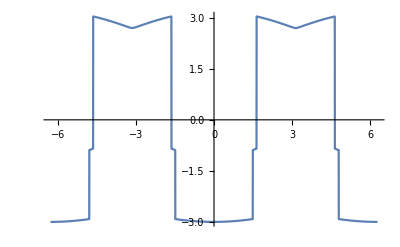

```mathematica
With[{t1=1,t2=0.8,δ=1,k1=0},Plot[Evaluate[Re[ⅇ^(-ⅈ k1-ⅈ k2) Root[ⅇ^(8 ⅈ k1+6 ⅈ k2) t1^4 t2^4+2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^4 t2^4+2 ⅇ^(9 ⅈ k1+7 ⅈ k2) t1^4 t2^4+ⅇ^(6 ⅈ k1+8 ⅈ k2) t1^4 t2^4+3 ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^4 t2^4+ⅇ^(10 ⅈ k1+8 ⅈ k2) t1^4 t2^4+ⅇ^(7 ⅈ k1+9 ⅈ k2) t1^4 t2^4+ⅇ^(9 ⅈ k1+9 ⅈ k2) t1^4 t2^4-2 ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^2 t2^6-2 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^6-2 ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^2 t2^6-ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^2 t2^6+ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^8-ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^4 t2^2 δ^2-ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ^2-ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ^2-ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^4 t2^2 δ^2+4 ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^2 t2^4 δ^2+4 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ^2+ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ^2+4 ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ^2+2 ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^2 t2^4 δ^2-4 ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^6 δ^2-2 ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^2 t2^2 δ^4-2 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^4-2 ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^4-2 ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^4-ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^2 t2^2 δ^4+6 ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^4 δ^4+ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^2 δ^6-4 ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^2 δ^6+ⅇ^(8 ⅈ k1+8 ⅈ k2) δ^8+(-2 ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^4 t2^2 δ-4 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^4 t2^2 δ-2 ⅇ^(6 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ+2 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ-2 ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ+2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^2 t2^4 δ+4 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ-4 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^3-2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^2 δ^5) #1+(-4 ⅇ^(5 ⅈ k1+5 ⅈ k2) t1^4 t2^2-ⅇ^(6 ⅈ k1+5 ⅈ k2) t1^4 t2^2-4 ⅇ^(7 ⅈ k1+5 ⅈ k2) t1^4 t2^2+ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^4 t2^2-12 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^4 t2^2+ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^4 t2^2-2 ⅇ^(5 ⅈ k1+7 ⅈ k2) t1^4 t2^2-ⅇ^(6 ⅈ k1+7 ⅈ k2) t1^4 t2^2-2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^4 t2^2+4 ⅇ^(6 ⅈ k1+5 ⅈ k2) t1^2 t2^4+4 ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^2 t2^4-7 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^2 t2^4+4 ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^2 t2^4+2 ⅇ^(6 ⅈ k1+7 ⅈ k2) t1^2 t2^4-4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t2^6-4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^4 δ^2-12 ⅇ^(6 ⅈ k1+5 ⅈ k2) t1^2 t2^2 δ^2+4 ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ^2-12 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ^2+4 ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ^2-6 ⅇ^(6 ⅈ k1+7 ⅈ k2) t1^2 t2^2 δ^2+4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t2^4 δ^2-9 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^2 δ^4+4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t2^2 δ^4-4 ⅇ^(6 ⅈ k1+6 ⅈ k2) δ^6) #1^2+(8 ⅇ^(5 ⅈ k1+5 ⅈ k2) t1^4 δ-4 ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ+4 ⅇ^(5 ⅈ k1+5 ⅈ k2) t1^2 δ^3) #1^3+(12 ⅇ^(4 ⅈ k1+4 ⅈ k2) t1^4-2 ⅇ^(4 ⅈ k1+3 ⅈ k2) t1^2 t2^2-2 ⅇ^(3 ⅈ k1+4 ⅈ k2) t1^2 t2^2+14 ⅇ^(4 ⅈ k1+4 ⅈ k2) t1^2 t2^2-2 ⅇ^(5 ⅈ k1+4 ⅈ k2) t1^2 t2^2-ⅇ^(4 ⅈ k1+5 ⅈ k2) t1^2 t2^2+6 ⅇ^(4 ⅈ k1+4 ⅈ k2) t2^4+15 ⅇ^(4 ⅈ k1+4 ⅈ k2) t1^2 δ^2+4 ⅇ^(4 ⅈ k1+4 ⅈ k2) t2^2 δ^2+6 ⅇ^(4 ⅈ k1+4 ⅈ k2) δ^4) #1^4-2 ⅇ^(3 ⅈ k1+3 ⅈ k2) t1^2 δ #1^5+(-7 ⅇ^(2 ⅈ k1+2 ⅈ k2) t1^2-4 ⅇ^(2 ⅈ k1+2 ⅈ k2) t2^2-4 ⅇ^(2 ⅈ k1+2 ⅈ k2) δ^2) #1^6+#1^8&,1]]],{k2,-2π,2π}]]
```

```mathematica
h={{-δ,t1,0,0,0,0,0,t2},{t1,δ,t2,0,ⅇ^(ⅈ k2) t1,0,0,0},{0,t2,δ,t1,0,0,0,ⅇ^(ⅈ k1) t1},{0,0,t1,δ,t2,0,ⅇ^(ⅈ k1) t1,0},{0,ⅇ^(-ⅈ k2) t1,0,t2,δ,t1,0,0},{ⅇ^(-ⅈ k2) t1,0,0,0,t1,-δ,t2,0},{0,0,0,ⅇ^(-ⅈ k1) t1,0,t2,-δ,t1},{t2,0,ⅇ^(-ⅈ k1) t1,0,0,0,t1,-δ}}
```

{{-δ,t1,0,0,0,0,0,t2},{t1,δ,t2,0,ⅇ^(ⅈ k2) t1,0,0,0},{0,t2,δ,t1,0,0,0,ⅇ^(ⅈ k1) t1},{0,0,t1,δ,t2,0,ⅇ^(ⅈ k1) t1,0},{0,ⅇ^(-ⅈ k2) t1,0,t2,δ,t1,0,0},{ⅇ^(-ⅈ k2) t1,0,0,0,t1,-δ,t2,0},{0,0,0,ⅇ^(-ⅈ k1) t1,0,t2,-δ,t1},{t2,0,ⅇ^(-ⅈ k1) t1,0,0,0,t1,-δ}}

```mathematica
Eigenvalues[h]
```

{ⅇ^(-ⅈ k1-ⅈ k2) Root[ⅇ^(8 ⅈ k1+6 ⅈ k2) t1^4 t2^4+2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^4 t2^4+2 ⅇ^(9 ⅈ k1+7 ⅈ k2) t1^4 t2^4+ⅇ^(6 ⅈ k1+8 ⅈ k2) t1^4 t2^4+3 ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^4 t2^4+ⅇ^(10 ⅈ k1+8 ⅈ k2) t1^4 t2^4+ⅇ^(7 ⅈ k1+9 ⅈ k2) t1^4 t2^4+ⅇ^(9 ⅈ k1+9 ⅈ k2) t1^4 t2^4-2 ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^2 t2^6-2 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^6-2 ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^2 t2^6-ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^2 t2^6+ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^8-ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^4 t2^2 δ^2-ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ^2-ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ^2-ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^4 t2^2 δ^2+4 ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^2 t2^4 δ^2+4 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ^2+ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ^2+4 ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ^2+2 ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^2 t2^4 δ^2-4 ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^6 δ^2-2 ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^2 t2^2 δ^4-2 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^4-2 ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^4-2 ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^4-ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^2 t2^2 δ^4+6 ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^4 δ^4+ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^2 δ^6-4 ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^2 δ^6+ⅇ^(8 ⅈ k1+8 ⅈ k2) δ^8+(-2 ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^4 t2^2 δ-4 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^4 t2^2 δ-2 ⅇ^(6 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ+2 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ-2 ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ+2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^2 t2^4 δ+4 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ-4 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^3-2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^2 δ^5) #1+(-4 ⅇ^(5 ⅈ k1+5 ⅈ k2) t1^4 t2^2-ⅇ^(6 ⅈ k1+5 ⅈ k2) t1^4 t2^2-4 ⅇ^(7 ⅈ k1+5 ⅈ k2) t1^4 t2^2+ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^4 t2^2-12 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^4 t2^2+ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^4 t2^2-2 ⅇ^(5 ⅈ k1+7 ⅈ k2) t1^4 t2^2-ⅇ^(6 ⅈ k1+7 ⅈ k2) t1^4 t2^2-2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^4 t2^2+4 ⅇ^(6 ⅈ k1+5 ⅈ k2) t1^2 t2^4+4 ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^2 t2^4-7 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^2 t2^4+4 ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^2 t2^4+2 ⅇ^(6 ⅈ k1+7 ⅈ k2) t1^2 t2^4-4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t2^6-4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^4 δ^2-12 ⅇ^(6 ⅈ k1+5 ⅈ k2) t1^2 t2^2 δ^2+4 ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ^2-12 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ^2+4 ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ^2-6 ⅇ^(6 ⅈ k1+7 ⅈ k2) t1^2 t2^2 δ^2+4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t2^4 δ^2-9 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^2 δ^4+4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t2^2 δ^4-4 ⅇ^(6 ⅈ k1+6 ⅈ k2) δ^6) #1^2+(8 ⅇ^(5 ⅈ k1+5 ⅈ k2) t1^4 δ-4 ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ+4 ⅇ^(5 ⅈ k1+5 ⅈ k2) t1^2 δ^3) #1^3+(12 ⅇ^(4 ⅈ k1+4 ⅈ k2) t1^4-2 ⅇ^(4 ⅈ k1+3 ⅈ k2) t1^2 t2^2-2 ⅇ^(3 ⅈ k1+4 ⅈ k2) t1^2 t2^2+14 ⅇ^(4 ⅈ k1+4 ⅈ k2) t1^2 t2^2-2 ⅇ^(5 ⅈ k1+4 ⅈ k2) t1^2 t2^2-ⅇ^(4 ⅈ k1+5 ⅈ k2) t1^2 t2^2+6 ⅇ^(4 ⅈ k1+4 ⅈ k2) t2^4+15 ⅇ^(4 ⅈ k1+4 ⅈ k2) t1^2 δ^2+4 ⅇ^(4 ⅈ k1+4 ⅈ k2) t2^2 δ^2+6 ⅇ^(4 ⅈ k1+4 ⅈ k2) δ^4) #1^4-2 ⅇ^(3 ⅈ k1+3 ⅈ k2) t1^2 δ #1^5+(-7 ⅇ^(2 ⅈ k1+2 ⅈ k2) t1^2-4 ⅇ^(2 ⅈ k1+2 ⅈ k2) t2^2-4 ⅇ^(2 ⅈ k1+2 ⅈ k2) δ^2) #1^6+#1^8&,1],ⅇ^(-ⅈ k1-ⅈ k2) Root[ⅇ^(8 ⅈ k1+6 ⅈ k2) t1^4 t2^4+2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^4 t2^4+2 ⅇ^(9 ⅈ k1+7 ⅈ k2) t1^4 t2^4+ⅇ^(6 ⅈ k1+8 ⅈ k2) t1^4 t2^4+3 ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^4 t2^4+ⅇ^(10 ⅈ k1+8 ⅈ k2) t1^4 t2^4+ⅇ^(7 ⅈ k1+9 ⅈ k2) t1^4 t2^4+ⅇ^(9 ⅈ k1+9 ⅈ k2) t1^4 t2^4-2 ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^2 t2^6-2 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^6-2 ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^2 t2^6-ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^2 t2^6+ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^8-ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^4 t2^2 δ^2-ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ^2-ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ^2-ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^4 t2^2 δ^2+4 ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^2 t2^4 δ^2+4 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ^2+ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ^2+4 ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ^2+2 ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^2 t2^4 δ^2-4 ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^6 δ^2-2 ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^2 t2^2 δ^4-2 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^4-2 ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^4-2 ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^4-ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^2 t2^2 δ^4+6 ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^4 δ^4+ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^2 δ^6-4 ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^2 δ^6+ⅇ^(8 ⅈ k1+8 ⅈ k2) δ^8+(-2 ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^4 t2^2 δ-4 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^4 t2^2 δ-2 ⅇ^(6 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ+2 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ-2 ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ+2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^2 t2^4 δ+4 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ-4 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^3-2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^2 δ^5) #1+(-4 ⅇ^(5 ⅈ k1+5 ⅈ k2) t1^4 t2^2-ⅇ^(6 ⅈ k1+5 ⅈ k2) t1^4 t2^2-4 ⅇ^(7 ⅈ k1+5 ⅈ k2) t1^4 t2^2+ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^4 t2^2-12 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^4 t2^2+ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^4 t2^2-2 ⅇ^(5 ⅈ k1+7 ⅈ k2) t1^4 t2^2-ⅇ^(6 ⅈ k1+7 ⅈ k2) t1^4 t2^2-2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^4 t2^2+4 ⅇ^(6 ⅈ k1+5 ⅈ k2) t1^2 t2^4+4 ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^2 t2^4-7 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^2 t2^4+4 ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^2 t2^4+2 ⅇ^(6 ⅈ k1+7 ⅈ k2) t1^2 t2^4-4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t2^6-4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^4 δ^2-12 ⅇ^(6 ⅈ k1+5 ⅈ k2) t1^2 t2^2 δ^2+4 ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ^2-12 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ^2+4 ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ^2-6 ⅇ^(6 ⅈ k1+7 ⅈ k2) t1^2 t2^2 δ^2+4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t2^4 δ^2-9 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^2 δ^4+4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t2^2 δ^4-4 ⅇ^(6 ⅈ k1+6 ⅈ k2) δ^6) #1^2+(8 ⅇ^(5 ⅈ k1+5 ⅈ k2) t1^4 δ-4 ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ+4 ⅇ^(5 ⅈ k1+5 ⅈ k2) t1^2 δ^3) #1^3+(12 ⅇ^(4 ⅈ k1+4 ⅈ k2) t1^4-2 ⅇ^(4 ⅈ k1+3 ⅈ k2) t1^2 t2^2-2 ⅇ^(3 ⅈ k1+4 ⅈ k2) t1^2 t2^2+14 ⅇ^(4 ⅈ k1+4 ⅈ k2) t1^2 t2^2-2 ⅇ^(5 ⅈ k1+4 ⅈ k2) t1^2 t2^2-ⅇ^(4 ⅈ k1+5 ⅈ k2) t1^2 t2^2+6 ⅇ^(4 ⅈ k1+4 ⅈ k2) t2^4+15 ⅇ^(4 ⅈ k1+4 ⅈ k2) t1^2 δ^2+4 ⅇ^(4 ⅈ k1+4 ⅈ k2) t2^2 δ^2+6 ⅇ^(4 ⅈ k1+4 ⅈ k2) δ^4) #1^4-2 ⅇ^(3 ⅈ k1+3 ⅈ k2) t1^2 δ #1^5+(-7 ⅇ^(2 ⅈ k1+2 ⅈ k2) t1^2-4 ⅇ^(2 ⅈ k1+2 ⅈ k2) t2^2-4 ⅇ^(2 ⅈ k1+2 ⅈ k2) δ^2) #1^6+#1^8&,2],ⅇ^(-ⅈ k1-ⅈ k2) Root[ⅇ^(8 ⅈ k1+6 ⅈ k2) t1^4 t2^4+2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^4 t2^4+2 ⅇ^(9 ⅈ k1+7 ⅈ k2) t1^4 t2^4+ⅇ^(6 ⅈ k1+8 ⅈ k2) t1^4 t2^4+3 ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^4 t2^4+ⅇ^(10 ⅈ k1+8 ⅈ k2) t1^4 t2^4+ⅇ^(7 ⅈ k1+9 ⅈ k2) t1^4 t2^4+ⅇ^(9 ⅈ k1+9 ⅈ k2) t1^4 t2^4-2 ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^2 t2^6-2 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^6-2 ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^2 t2^6-ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^2 t2^6+ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^8-ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^4 t2^2 δ^2-ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ^2-ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ^2-ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^4 t2^2 δ^2+4 ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^2 t2^4 δ^2+4 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ^2+ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ^2+4 ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ^2+2 ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^2 t2^4 δ^2-4 ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^6 δ^2-2 ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^2 t2^2 δ^4-2 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^4-2 ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^4-2 ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^4-ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^2 t2^2 δ^4+6 ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^4 δ^4+ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^2 δ^6-4 ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^2 δ^6+ⅇ^(8 ⅈ k1+8 ⅈ k2) δ^8+(-2 ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^4 t2^2 δ-4 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^4 t2^2 δ-2 ⅇ^(6 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ+2 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ-2 ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ+2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^2 t2^4 δ+4 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ-4 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^3-2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^2 δ^5) #1+(-4 ⅇ^(5 ⅈ k1+5 ⅈ k2) t1^4 t2^2-ⅇ^(6 ⅈ k1+5 ⅈ k2) t1^4 t2^2-4 ⅇ^(7 ⅈ k1+5 ⅈ k2) t1^4 t2^2+ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^4 t2^2-12 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^4 t2^2+ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^4 t2^2-2 ⅇ^(5 ⅈ k1+7 ⅈ k2) t1^4 t2^2-ⅇ^(6 ⅈ k1+7 ⅈ k2) t1^4 t2^2-2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^4 t2^2+4 ⅇ^(6 ⅈ k1+5 ⅈ k2) t1^2 t2^4+4 ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^2 t2^4-7 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^2 t2^4+4 ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^2 t2^4+2 ⅇ^(6 ⅈ k1+7 ⅈ k2) t1^2 t2^4-4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t2^6-4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^4 δ^2-12 ⅇ^(6 ⅈ k1+5 ⅈ k2) t1^2 t2^2 δ^2+4 ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ^2-12 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ^2+4 ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ^2-6 ⅇ^(6 ⅈ k1+7 ⅈ k2) t1^2 t2^2 δ^2+4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t2^4 δ^2-9 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^2 δ^4+4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t2^2 δ^4-4 ⅇ^(6 ⅈ k1+6 ⅈ k2) δ^6) #1^2+(8 ⅇ^(5 ⅈ k1+5 ⅈ k2) t1^4 δ-4 ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ+4 ⅇ^(5 ⅈ k1+5 ⅈ k2) t1^2 δ^3) #1^3+(12 ⅇ^(4 ⅈ k1+4 ⅈ k2) t1^4-2 ⅇ^(4 ⅈ k1+3 ⅈ k2) t1^2 t2^2-2 ⅇ^(3 ⅈ k1+4 ⅈ k2) t1^2 t2^2+14 ⅇ^(4 ⅈ k1+4 ⅈ k2) t1^2 t2^2-2 ⅇ^(5 ⅈ k1+4 ⅈ k2) t1^2 t2^2-ⅇ^(4 ⅈ k1+5 ⅈ k2) t1^2 t2^2+6 ⅇ^(4 ⅈ k1+4 ⅈ k2) t2^4+15 ⅇ^(4 ⅈ k1+4 ⅈ k2) t1^2 δ^2+4 ⅇ^(4 ⅈ k1+4 ⅈ k2) t2^2 δ^2+6 ⅇ^(4 ⅈ k1+4 ⅈ k2) δ^4) #1^4-2 ⅇ^(3 ⅈ k1+3 ⅈ k2) t1^2 δ #1^5+(-7 ⅇ^(2 ⅈ k1+2 ⅈ k2) t1^2-4 ⅇ^(2 ⅈ k1+2 ⅈ k2) t2^2-4 ⅇ^(2 ⅈ k1+2 ⅈ k2) δ^2) #1^6+#1^8&,3],ⅇ^(-ⅈ k1-ⅈ k2) Root[ⅇ^(8 ⅈ k1+6 ⅈ k2) t1^4 t2^4+2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^4 t2^4+2 ⅇ^(9 ⅈ k1+7 ⅈ k2) t1^4 t2^4+ⅇ^(6 ⅈ k1+8 ⅈ k2) t1^4 t2^4+3 ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^4 t2^4+ⅇ^(10 ⅈ k1+8 ⅈ k2) t1^4 t2^4+ⅇ^(7 ⅈ k1+9 ⅈ k2) t1^4 t2^4+ⅇ^(9 ⅈ k1+9 ⅈ k2) t1^4 t2^4-2 ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^2 t2^6-2 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^6-2 ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^2 t2^6-ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^2 t2^6+ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^8-ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^4 t2^2 δ^2-ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ^2-ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ^2-ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^4 t2^2 δ^2+4 ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^2 t2^4 δ^2+4 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ^2+ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ^2+4 ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ^2+2 ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^2 t2^4 δ^2-4 ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^6 δ^2-2 ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^2 t2^2 δ^4-2 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^4-2 ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^4-2 ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^4-ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^2 t2^2 δ^4+6 ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^4 δ^4+ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^2 δ^6-4 ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^2 δ^6+ⅇ^(8 ⅈ k1+8 ⅈ k2) δ^8+(-2 ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^4 t2^2 δ-4 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^4 t2^2 δ-2 ⅇ^(6 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ+2 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ-2 ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ+2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^2 t2^4 δ+4 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ-4 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^3-2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^2 δ^5) #1+(-4 ⅇ^(5 ⅈ k1+5 ⅈ k2) t1^4 t2^2-ⅇ^(6 ⅈ k1+5 ⅈ k2) t1^4 t2^2-4 ⅇ^(7 ⅈ k1+5 ⅈ k2) t1^4 t2^2+ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^4 t2^2-12 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^4 t2^2+ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^4 t2^2-2 ⅇ^(5 ⅈ k1+7 ⅈ k2) t1^4 t2^2-ⅇ^(6 ⅈ k1+7 ⅈ k2) t1^4 t2^2-2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^4 t2^2+4 ⅇ^(6 ⅈ k1+5 ⅈ k2) t1^2 t2^4+4 ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^2 t2^4-7 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^2 t2^4+4 ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^2 t2^4+2 ⅇ^(6 ⅈ k1+7 ⅈ k2) t1^2 t2^4-4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t2^6-4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^4 δ^2-12 ⅇ^(6 ⅈ k1+5 ⅈ k2) t1^2 t2^2 δ^2+4 ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ^2-12 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ^2+4 ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ^2-6 ⅇ^(6 ⅈ k1+7 ⅈ k2) t1^2 t2^2 δ^2+4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t2^4 δ^2-9 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^2 δ^4+4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t2^2 δ^4-4 ⅇ^(6 ⅈ k1+6 ⅈ k2) δ^6) #1^2+(8 ⅇ^(5 ⅈ k1+5 ⅈ k2) t1^4 δ-4 ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ+4 ⅇ^(5 ⅈ k1+5 ⅈ k2) t1^2 δ^3) #1^3+(12 ⅇ^(4 ⅈ k1+4 ⅈ k2) t1^4-2 ⅇ^(4 ⅈ k1+3 ⅈ k2) t1^2 t2^2-2 ⅇ^(3 ⅈ k1+4 ⅈ k2) t1^2 t2^2+14 ⅇ^(4 ⅈ k1+4 ⅈ k2) t1^2 t2^2-2 ⅇ^(5 ⅈ k1+4 ⅈ k2) t1^2 t2^2-ⅇ^(4 ⅈ k1+5 ⅈ k2) t1^2 t2^2+6 ⅇ^(4 ⅈ k1+4 ⅈ k2) t2^4+15 ⅇ^(4 ⅈ k1+4 ⅈ k2) t1^2 δ^2+4 ⅇ^(4 ⅈ k1+4 ⅈ k2) t2^2 δ^2+6 ⅇ^(4 ⅈ k1+4 ⅈ k2) δ^4) #1^4-2 ⅇ^(3 ⅈ k1+3 ⅈ k2) t1^2 δ #1^5+(-7 ⅇ^(2 ⅈ k1+2 ⅈ k2) t1^2-4 ⅇ^(2 ⅈ k1+2 ⅈ k2) t2^2-4 ⅇ^(2 ⅈ k1+2 ⅈ k2) δ^2) #1^6+#1^8&,4],ⅇ^(-ⅈ k1-ⅈ k2) Root[ⅇ^(8 ⅈ k1+6 ⅈ k2) t1^4 t2^4+2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^4 t2^4+2 ⅇ^(9 ⅈ k1+7 ⅈ k2) t1^4 t2^4+ⅇ^(6 ⅈ k1+8 ⅈ k2) t1^4 t2^4+3 ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^4 t2^4+ⅇ^(10 ⅈ k1+8 ⅈ k2) t1^4 t2^4+ⅇ^(7 ⅈ k1+9 ⅈ k2) t1^4 t2^4+ⅇ^(9 ⅈ k1+9 ⅈ k2) t1^4 t2^4-2 ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^2 t2^6-2 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^6-2 ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^2 t2^6-ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^2 t2^6+ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^8-ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^4 t2^2 δ^2-ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ^2-ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ^2-ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^4 t2^2 δ^2+4 ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^2 t2^4 δ^2+4 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ^2+ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ^2+4 ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ^2+2 ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^2 t2^4 δ^2-4 ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^6 δ^2-2 ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^2 t2^2 δ^4-2 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^4-2 ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^4-2 ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^4-ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^2 t2^2 δ^4+6 ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^4 δ^4+ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^2 δ^6-4 ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^2 δ^6+ⅇ^(8 ⅈ k1+8 ⅈ k2) δ^8+(-2 ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^4 t2^2 δ-4 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^4 t2^2 δ-2 ⅇ^(6 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ+2 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ-2 ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ+2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^2 t2^4 δ+4 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ-4 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^3-2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^2 δ^5) #1+(-4 ⅇ^(5 ⅈ k1+5 ⅈ k2) t1^4 t2^2-ⅇ^(6 ⅈ k1+5 ⅈ k2) t1^4 t2^2-4 ⅇ^(7 ⅈ k1+5 ⅈ k2) t1^4 t2^2+ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^4 t2^2-12 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^4 t2^2+ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^4 t2^2-2 ⅇ^(5 ⅈ k1+7 ⅈ k2) t1^4 t2^2-ⅇ^(6 ⅈ k1+7 ⅈ k2) t1^4 t2^2-2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^4 t2^2+4 ⅇ^(6 ⅈ k1+5 ⅈ k2) t1^2 t2^4+4 ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^2 t2^4-7 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^2 t2^4+4 ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^2 t2^4+2 ⅇ^(6 ⅈ k1+7 ⅈ k2) t1^2 t2^4-4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t2^6-4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^4 δ^2-12 ⅇ^(6 ⅈ k1+5 ⅈ k2) t1^2 t2^2 δ^2+4 ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ^2-12 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ^2+4 ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ^2-6 ⅇ^(6 ⅈ k1+7 ⅈ k2) t1^2 t2^2 δ^2+4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t2^4 δ^2-9 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^2 δ^4+4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t2^2 δ^4-4 ⅇ^(6 ⅈ k1+6 ⅈ k2) δ^6) #1^2+(8 ⅇ^(5 ⅈ k1+5 ⅈ k2) t1^4 δ-4 ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ+4 ⅇ^(5 ⅈ k1+5 ⅈ k2) t1^2 δ^3) #1^3+(12 ⅇ^(4 ⅈ k1+4 ⅈ k2) t1^4-2 ⅇ^(4 ⅈ k1+3 ⅈ k2) t1^2 t2^2-2 ⅇ^(3 ⅈ k1+4 ⅈ k2) t1^2 t2^2+14 ⅇ^(4 ⅈ k1+4 ⅈ k2) t1^2 t2^2-2 ⅇ^(5 ⅈ k1+4 ⅈ k2) t1^2 t2^2-ⅇ^(4 ⅈ k1+5 ⅈ k2) t1^2 t2^2+6 ⅇ^(4 ⅈ k1+4 ⅈ k2) t2^4+15 ⅇ^(4 ⅈ k1+4 ⅈ k2) t1^2 δ^2+4 ⅇ^(4 ⅈ k1+4 ⅈ k2) t2^2 δ^2+6 ⅇ^(4 ⅈ k1+4 ⅈ k2) δ^4) #1^4-2 ⅇ^(3 ⅈ k1+3 ⅈ k2) t1^2 δ #1^5+(-7 ⅇ^(2 ⅈ k1+2 ⅈ k2) t1^2-4 ⅇ^(2 ⅈ k1+2 ⅈ k2) t2^2-4 ⅇ^(2 ⅈ k1+2 ⅈ k2) δ^2) #1^6+#1^8&,5],ⅇ^(-ⅈ k1-ⅈ k2) Root[ⅇ^(8 ⅈ k1+6 ⅈ k2) t1^4 t2^4+2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^4 t2^4+2 ⅇ^(9 ⅈ k1+7 ⅈ k2) t1^4 t2^4+ⅇ^(6 ⅈ k1+8 ⅈ k2) t1^4 t2^4+3 ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^4 t2^4+ⅇ^(10 ⅈ k1+8 ⅈ k2) t1^4 t2^4+ⅇ^(7 ⅈ k1+9 ⅈ k2) t1^4 t2^4+ⅇ^(9 ⅈ k1+9 ⅈ k2) t1^4 t2^4-2 ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^2 t2^6-2 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^6-2 ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^2 t2^6-ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^2 t2^6+ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^8-ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^4 t2^2 δ^2-ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ^2-ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ^2-ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^4 t2^2 δ^2+4 ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^2 t2^4 δ^2+4 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ^2+ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ^2+4 ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ^2+2 ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^2 t2^4 δ^2-4 ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^6 δ^2-2 ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^2 t2^2 δ^4-2 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^4-2 ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^4-2 ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^4-ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^2 t2^2 δ^4+6 ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^4 δ^4+ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^2 δ^6-4 ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^2 δ^6+ⅇ^(8 ⅈ k1+8 ⅈ k2) δ^8+(-2 ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^4 t2^2 δ-4 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^4 t2^2 δ-2 ⅇ^(6 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ+2 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ-2 ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ+2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^2 t2^4 δ+4 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ-4 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^3-2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^2 δ^5) #1+(-4 ⅇ^(5 ⅈ k1+5 ⅈ k2) t1^4 t2^2-ⅇ^(6 ⅈ k1+5 ⅈ k2) t1^4 t2^2-4 ⅇ^(7 ⅈ k1+5 ⅈ k2) t1^4 t2^2+ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^4 t2^2-12 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^4 t2^2+ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^4 t2^2-2 ⅇ^(5 ⅈ k1+7 ⅈ k2) t1^4 t2^2-ⅇ^(6 ⅈ k1+7 ⅈ k2) t1^4 t2^2-2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^4 t2^2+4 ⅇ^(6 ⅈ k1+5 ⅈ k2) t1^2 t2^4+4 ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^2 t2^4-7 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^2 t2^4+4 ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^2 t2^4+2 ⅇ^(6 ⅈ k1+7 ⅈ k2) t1^2 t2^4-4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t2^6-4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^4 δ^2-12 ⅇ^(6 ⅈ k1+5 ⅈ k2) t1^2 t2^2 δ^2+4 ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ^2-12 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ^2+4 ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ^2-6 ⅇ^(6 ⅈ k1+7 ⅈ k2) t1^2 t2^2 δ^2+4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t2^4 δ^2-9 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^2 δ^4+4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t2^2 δ^4-4 ⅇ^(6 ⅈ k1+6 ⅈ k2) δ^6) #1^2+(8 ⅇ^(5 ⅈ k1+5 ⅈ k2) t1^4 δ-4 ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ+4 ⅇ^(5 ⅈ k1+5 ⅈ k2) t1^2 δ^3) #1^3+(12 ⅇ^(4 ⅈ k1+4 ⅈ k2) t1^4-2 ⅇ^(4 ⅈ k1+3 ⅈ k2) t1^2 t2^2-2 ⅇ^(3 ⅈ k1+4 ⅈ k2) t1^2 t2^2+14 ⅇ^(4 ⅈ k1+4 ⅈ k2) t1^2 t2^2-2 ⅇ^(5 ⅈ k1+4 ⅈ k2) t1^2 t2^2-ⅇ^(4 ⅈ k1+5 ⅈ k2) t1^2 t2^2+6 ⅇ^(4 ⅈ k1+4 ⅈ k2) t2^4+15 ⅇ^(4 ⅈ k1+4 ⅈ k2) t1^2 δ^2+4 ⅇ^(4 ⅈ k1+4 ⅈ k2) t2^2 δ^2+6 ⅇ^(4 ⅈ k1+4 ⅈ k2) δ^4) #1^4-2 ⅇ^(3 ⅈ k1+3 ⅈ k2) t1^2 δ #1^5+(-7 ⅇ^(2 ⅈ k1+2 ⅈ k2) t1^2-4 ⅇ^(2 ⅈ k1+2 ⅈ k2) t2^2-4 ⅇ^(2 ⅈ k1+2 ⅈ k2) δ^2) #1^6+#1^8&,6],ⅇ^(-ⅈ k1-ⅈ k2) Root[ⅇ^(8 ⅈ k1+6 ⅈ k2) t1^4 t2^4+2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^4 t2^4+2 ⅇ^(9 ⅈ k1+7 ⅈ k2) t1^4 t2^4+ⅇ^(6 ⅈ k1+8 ⅈ k2) t1^4 t2^4+3 ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^4 t2^4+ⅇ^(10 ⅈ k1+8 ⅈ k2) t1^4 t2^4+ⅇ^(7 ⅈ k1+9 ⅈ k2) t1^4 t2^4+ⅇ^(9 ⅈ k1+9 ⅈ k2) t1^4 t2^4-2 ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^2 t2^6-2 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^6-2 ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^2 t2^6-ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^2 t2^6+ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^8-ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^4 t2^2 δ^2-ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ^2-ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ^2-ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^4 t2^2 δ^2+4 ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^2 t2^4 δ^2+4 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ^2+ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ^2+4 ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ^2+2 ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^2 t2^4 δ^2-4 ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^6 δ^2-2 ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^2 t2^2 δ^4-2 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^4-2 ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^4-2 ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^4-ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^2 t2^2 δ^4+6 ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^4 δ^4+ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^2 δ^6-4 ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^2 δ^6+ⅇ^(8 ⅈ k1+8 ⅈ k2) δ^8+(-2 ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^4 t2^2 δ-4 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^4 t2^2 δ-2 ⅇ^(6 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ+2 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ-2 ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ+2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^2 t2^4 δ+4 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ-4 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^3-2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^2 δ^5) #1+(-4 ⅇ^(5 ⅈ k1+5 ⅈ k2) t1^4 t2^2-ⅇ^(6 ⅈ k1+5 ⅈ k2) t1^4 t2^2-4 ⅇ^(7 ⅈ k1+5 ⅈ k2) t1^4 t2^2+ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^4 t2^2-12 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^4 t2^2+ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^4 t2^2-2 ⅇ^(5 ⅈ k1+7 ⅈ k2) t1^4 t2^2-ⅇ^(6 ⅈ k1+7 ⅈ k2) t1^4 t2^2-2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^4 t2^2+4 ⅇ^(6 ⅈ k1+5 ⅈ k2) t1^2 t2^4+4 ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^2 t2^4-7 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^2 t2^4+4 ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^2 t2^4+2 ⅇ^(6 ⅈ k1+7 ⅈ k2) t1^2 t2^4-4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t2^6-4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^4 δ^2-12 ⅇ^(6 ⅈ k1+5 ⅈ k2) t1^2 t2^2 δ^2+4 ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ^2-12 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ^2+4 ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ^2-6 ⅇ^(6 ⅈ k1+7 ⅈ k2) t1^2 t2^2 δ^2+4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t2^4 δ^2-9 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^2 δ^4+4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t2^2 δ^4-4 ⅇ^(6 ⅈ k1+6 ⅈ k2) δ^6) #1^2+(8 ⅇ^(5 ⅈ k1+5 ⅈ k2) t1^4 δ-4 ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ+4 ⅇ^(5 ⅈ k1+5 ⅈ k2) t1^2 δ^3) #1^3+(12 ⅇ^(4 ⅈ k1+4 ⅈ k2) t1^4-2 ⅇ^(4 ⅈ k1+3 ⅈ k2) t1^2 t2^2-2 ⅇ^(3 ⅈ k1+4 ⅈ k2) t1^2 t2^2+14 ⅇ^(4 ⅈ k1+4 ⅈ k2) t1^2 t2^2-2 ⅇ^(5 ⅈ k1+4 ⅈ k2) t1^2 t2^2-ⅇ^(4 ⅈ k1+5 ⅈ k2) t1^2 t2^2+6 ⅇ^(4 ⅈ k1+4 ⅈ k2) t2^4+15 ⅇ^(4 ⅈ k1+4 ⅈ k2) t1^2 δ^2+4 ⅇ^(4 ⅈ k1+4 ⅈ k2) t2^2 δ^2+6 ⅇ^(4 ⅈ k1+4 ⅈ k2) δ^4) #1^4-2 ⅇ^(3 ⅈ k1+3 ⅈ k2) t1^2 δ #1^5+(-7 ⅇ^(2 ⅈ k1+2 ⅈ k2) t1^2-4 ⅇ^(2 ⅈ k1+2 ⅈ k2) t2^2-4 ⅇ^(2 ⅈ k1+2 ⅈ k2) δ^2) #1^6+#1^8&,7],ⅇ^(-ⅈ k1-ⅈ k2) Root[ⅇ^(8 ⅈ k1+6 ⅈ k2) t1^4 t2^4+2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^4 t2^4+2 ⅇ^(9 ⅈ k1+7 ⅈ k2) t1^4 t2^4+ⅇ^(6 ⅈ k1+8 ⅈ k2) t1^4 t2^4+3 ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^4 t2^4+ⅇ^(10 ⅈ k1+8 ⅈ k2) t1^4 t2^4+ⅇ^(7 ⅈ k1+9 ⅈ k2) t1^4 t2^4+ⅇ^(9 ⅈ k1+9 ⅈ k2) t1^4 t2^4-2 ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^2 t2^6-2 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^6-2 ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^2 t2^6-ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^2 t2^6+ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^8-ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^4 t2^2 δ^2-ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ^2-ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ^2-ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^4 t2^2 δ^2+4 ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^2 t2^4 δ^2+4 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ^2+ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ^2+4 ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ^2+2 ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^2 t2^4 δ^2-4 ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^6 δ^2-2 ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^2 t2^2 δ^4-2 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^4-2 ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^4-2 ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^4-ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^2 t2^2 δ^4+6 ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^4 δ^4+ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^2 δ^6-4 ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^2 δ^6+ⅇ^(8 ⅈ k1+8 ⅈ k2) δ^8+(-2 ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^4 t2^2 δ-4 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^4 t2^2 δ-2 ⅇ^(6 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ+2 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ-2 ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ+2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^2 t2^4 δ+4 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ-4 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^3-2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^2 δ^5) #1+(-4 ⅇ^(5 ⅈ k1+5 ⅈ k2) t1^4 t2^2-ⅇ^(6 ⅈ k1+5 ⅈ k2) t1^4 t2^2-4 ⅇ^(7 ⅈ k1+5 ⅈ k2) t1^4 t2^2+ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^4 t2^2-12 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^4 t2^2+ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^4 t2^2-2 ⅇ^(5 ⅈ k1+7 ⅈ k2) t1^4 t2^2-ⅇ^(6 ⅈ k1+7 ⅈ k2) t1^4 t2^2-2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^4 t2^2+4 ⅇ^(6 ⅈ k1+5 ⅈ k2) t1^2 t2^4+4 ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^2 t2^4-7 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^2 t2^4+4 ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^2 t2^4+2 ⅇ^(6 ⅈ k1+7 ⅈ k2) t1^2 t2^4-4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t2^6-4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^4 δ^2-12 ⅇ^(6 ⅈ k1+5 ⅈ k2) t1^2 t2^2 δ^2+4 ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ^2-12 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ^2+4 ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ^2-6 ⅇ^(6 ⅈ k1+7 ⅈ k2) t1^2 t2^2 δ^2+4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t2^4 δ^2-9 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^2 δ^4+4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t2^2 δ^4-4 ⅇ^(6 ⅈ k1+6 ⅈ k2) δ^6) #1^2+(8 ⅇ^(5 ⅈ k1+5 ⅈ k2) t1^4 δ-4 ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ+4 ⅇ^(5 ⅈ k1+5 ⅈ k2) t1^2 δ^3) #1^3+(12 ⅇ^(4 ⅈ k1+4 ⅈ k2) t1^4-2 ⅇ^(4 ⅈ k1+3 ⅈ k2) t1^2 t2^2-2 ⅇ^(3 ⅈ k1+4 ⅈ k2) t1^2 t2^2+14 ⅇ^(4 ⅈ k1+4 ⅈ k2) t1^2 t2^2-2 ⅇ^(5 ⅈ k1+4 ⅈ k2) t1^2 t2^2-ⅇ^(4 ⅈ k1+5 ⅈ k2) t1^2 t2^2+6 ⅇ^(4 ⅈ k1+4 ⅈ k2) t2^4+15 ⅇ^(4 ⅈ k1+4 ⅈ k2) t1^2 δ^2+4 ⅇ^(4 ⅈ k1+4 ⅈ k2) t2^2 δ^2+6 ⅇ^(4 ⅈ k1+4 ⅈ k2) δ^4) #1^4-2 ⅇ^(3 ⅈ k1+3 ⅈ k2) t1^2 δ #1^5+(-7 ⅇ^(2 ⅈ k1+2 ⅈ k2) t1^2-4 ⅇ^(2 ⅈ k1+2 ⅈ k2) t2^2-4 ⅇ^(2 ⅈ k1+2 ⅈ k2) δ^2) #1^6+#1^8&,8]}

```mathematica
With[{t1=1,t2=0.8,δ=1},Plot3D[ⅇ^(-ⅈ k1-ⅈ k2) Root[ⅇ^(8 ⅈ k1+6 ⅈ k2) t1^4 t2^4+2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^4 t2^4+2 ⅇ^(9 ⅈ k1+7 ⅈ k2) t1^4 t2^4+ⅇ^(6 ⅈ k1+8 ⅈ k2) t1^4 t2^4+3 ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^4 t2^4+ⅇ^(10 ⅈ k1+8 ⅈ k2) t1^4 t2^4+ⅇ^(7 ⅈ k1+9 ⅈ k2) t1^4 t2^4+ⅇ^(9 ⅈ k1+9 ⅈ k2) t1^4 t2^4-2 ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^2 t2^6-2 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^6-2 ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^2 t2^6-ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^2 t2^6+ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^8-ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^4 t2^2 δ^2-ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ^2-ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ^2-ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^4 t2^2 δ^2+4 ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^2 t2^4 δ^2+4 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ^2+ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ^2+4 ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ^2+2 ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^2 t2^4 δ^2-4 ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^6 δ^2-2 ⅇ^(8 ⅈ k1+7 ⅈ k2) t1^2 t2^2 δ^4-2 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^4-2 ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^4-2 ⅇ^(9 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^4-ⅇ^(8 ⅈ k1+9 ⅈ k2) t1^2 t2^2 δ^4+6 ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^4 δ^4+ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^2 δ^6-4 ⅇ^(8 ⅈ k1+8 ⅈ k2) t2^2 δ^6+ⅇ^(8 ⅈ k1+8 ⅈ k2) δ^8+(-2 ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^4 t2^2 δ-4 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^4 t2^2 δ-2 ⅇ^(6 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ+2 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ-2 ⅇ^(8 ⅈ k1+8 ⅈ k2) t1^4 t2^2 δ+2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^2 t2^4 δ+4 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^4 δ-4 ⅇ^(7 ⅈ k1+8 ⅈ k2) t1^2 t2^2 δ^3-2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^2 δ^5) #1+(-4 ⅇ^(5 ⅈ k1+5 ⅈ k2) t1^4 t2^2-ⅇ^(6 ⅈ k1+5 ⅈ k2) t1^4 t2^2-4 ⅇ^(7 ⅈ k1+5 ⅈ k2) t1^4 t2^2+ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^4 t2^2-12 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^4 t2^2+ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^4 t2^2-2 ⅇ^(5 ⅈ k1+7 ⅈ k2) t1^4 t2^2-ⅇ^(6 ⅈ k1+7 ⅈ k2) t1^4 t2^2-2 ⅇ^(7 ⅈ k1+7 ⅈ k2) t1^4 t2^2+4 ⅇ^(6 ⅈ k1+5 ⅈ k2) t1^2 t2^4+4 ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^2 t2^4-7 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^2 t2^4+4 ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^2 t2^4+2 ⅇ^(6 ⅈ k1+7 ⅈ k2) t1^2 t2^4-4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t2^6-4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^4 δ^2-12 ⅇ^(6 ⅈ k1+5 ⅈ k2) t1^2 t2^2 δ^2+4 ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ^2-12 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ^2+4 ⅇ^(7 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ^2-6 ⅇ^(6 ⅈ k1+7 ⅈ k2) t1^2 t2^2 δ^2+4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t2^4 δ^2-9 ⅇ^(6 ⅈ k1+6 ⅈ k2) t1^2 δ^4+4 ⅇ^(6 ⅈ k1+6 ⅈ k2) t2^2 δ^4-4 ⅇ^(6 ⅈ k1+6 ⅈ k2) δ^6) #1^2+(8 ⅇ^(5 ⅈ k1+5 ⅈ k2) t1^4 δ-4 ⅇ^(5 ⅈ k1+6 ⅈ k2) t1^2 t2^2 δ+4 ⅇ^(5 ⅈ k1+5 ⅈ k2) t1^2 δ^3) #1^3+(12 ⅇ^(4 ⅈ k1+4 ⅈ k2) t1^4-2 ⅇ^(4 ⅈ k1+3 ⅈ k2) t1^2 t2^2-2 ⅇ^(3 ⅈ k1+4 ⅈ k2) t1^2 t2^2+14 ⅇ^(4 ⅈ k1+4 ⅈ k2) t1^2 t2^2-2 ⅇ^(5 ⅈ k1+4 ⅈ k2) t1^2 t2^2-ⅇ^(4 ⅈ k1+5 ⅈ k2) t1^2 t2^2+6 ⅇ^(4 ⅈ k1+4 ⅈ k2) t2^4+15 ⅇ^(4 ⅈ k1+4 ⅈ k2) t1^2 δ^2+4 ⅇ^(4 ⅈ k1+4 ⅈ k2) t2^2 δ^2+6 ⅇ^(4 ⅈ k1+4 ⅈ k2) δ^4) #1^4-2 ⅇ^(3 ⅈ k1+3 ⅈ k2) t1^2 δ #1^5+(-7 ⅇ^(2 ⅈ k1+2 ⅈ k2) t1^2-4 ⅇ^(2 ⅈ k1+2 ⅈ k2) t2^2-4 ⅇ^(2 ⅈ k1+2 ⅈ k2) δ^2) #1^6+#1^8&,1],{k1,-2π,2π},{k2,-2π,2π}]]
```

-Graphics3D-

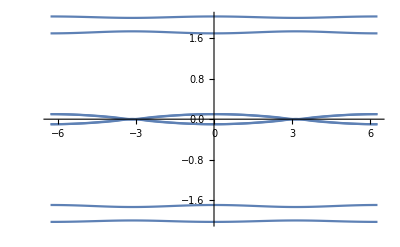

```mathematica
With[{t1=1,t2=0.1,δ=0,k1=0},Plot[Sort[Re[Eigenvalues[N[{{-δ,t1,0,0,0,0,0,t2},{t1,δ,t2,0,ⅇ^(ⅈ k2) t1,0,0,0},{0,t2,δ,t1,0,0,0,ⅇ^(ⅈ k1) t1},{0,0,t1,δ,t2,0,ⅇ^(ⅈ k1) t1,0},{0,ⅇ^(-ⅈ k2) t1,0,t2,δ,t1,0,0},{ⅇ^(-ⅈ k2) t1,0,0,0,t1,-δ,t2,0},{0,0,0,ⅇ^(-ⅈ k1) t1,0,t2,-δ,t1},{t2,0,ⅇ^(-ⅈ k1) t1,0,0,0,t1,-δ}}]]]],{k2,-2π,2π}]]
```

```mathematica
signconfig1 = {1,1,1,1,-1,-1,-1,-1}
```

{1,1,1,1,-1,-1,-1,-1}

```mathematica
DiagonalMatrix[δ signconfig1]+
```

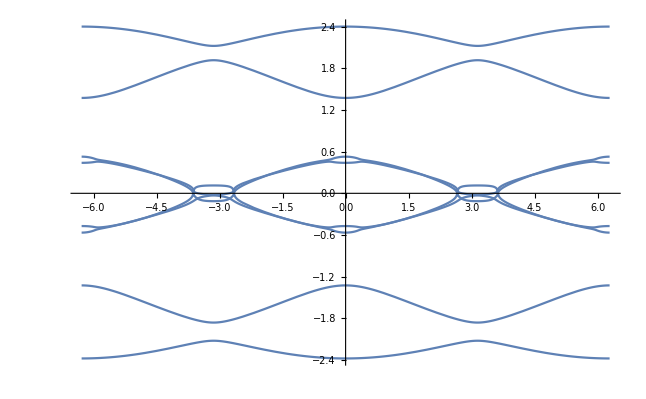

```mathematica
With[{t1=1,t2=0.5,δ=0.1,k1=0},Plot[Sort[Re[Eigenvalues[N[{{-δ,t1,0,0,0,0,0,t2},{t1,δ,t2,0,ⅇ^(ⅈ k2) t1,0,0,0},{0,t2,δ,t1,0,0,0,ⅇ^(ⅈ k1) t1},{0,0,t1,δ,t2,0,ⅇ^(ⅈ k1) t1,0},{0,ⅇ^(-ⅈ k2) t1,0,t2,δ,t1,0,0},{ⅇ^(-ⅈ k2) t1,0,0,0,t1,-δ,t2,0},{0,0,0,ⅇ^(-ⅈ k1) t1,0,t2,-δ,t1},{t2,0,ⅇ^(-ⅈ k1) t1,0,0,0,t1,-δ}}]]]],{k2,-2π,2π}]]
```

```mathematica
With[{t1=1,t2=0.5,δ=0.1},Plot3D[Sort[Re[Eigenvalues[N[{{-δ,t1,0,0,0,0,0,t2},{t1,δ,t2,0,ⅇ^(ⅈ k2) t1,0,0,0},{0,t2,δ,t1,0,0,0,ⅇ^(ⅈ k1) t1},{0,0,t1,δ,t2,0,ⅇ^(ⅈ k1) t1,0},{0,ⅇ^(-ⅈ k2) t1,0,t2,δ,t1,0,0},{ⅇ^(-ⅈ k2) t1,0,0,0,t1,-δ,t2,0},{0,0,0,ⅇ^(-ⅈ k1) t1,0,t2,-δ,t1},{t2,0,ⅇ^(-ⅈ k1) t1,0,0,0,t1,-δ}}]]]],{k1,-2π,2π},{k2,-2π,2π}]]
```

-Graphics3D-